Part::partw: Part 14 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

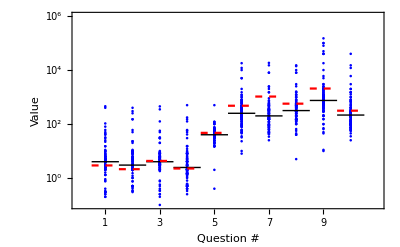

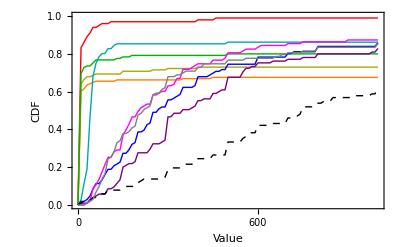

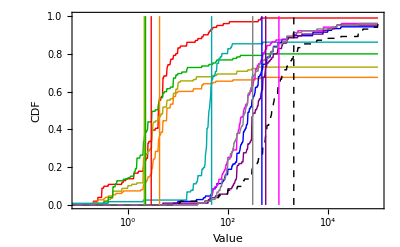

{{{0.5,Log[4]/Log[10]},{1.5,Log[4]/Log[10]}},{{1.5,Log[3]/Log[10]},{2.5,Log[3]/Log[10]}},{{2.5,Log[4]/Log[10]},{3.5,Log[4]/Log[10]}},{{3.5,0.389166},{4.5,0.389166}},{{4.5,Log[40]/Log[10]},{5.5,Log[40]/Log[10]}},{{5.5,Log[250]/Log[10]},{6.5,Log[250]/Log[10]}},{{6.5,Log[200]/Log[10]},{7.5,Log[200]/Log[10]}},{{7.5,Log[315]/Log[10]},{8.5,Log[315]/Log[10]}},{{8.5,Log[1495/2]/Log[10]},{9.5,Log[1495/2]/Log[10]}},{{9.5,Log[215]/Log[10]},{10.5,Log[215]/Log[10]}}}

```mathematica
(*MTurk Guesses*)
directory="~/Desktop/ExpFiles/";
batchfiles={"Batch_3351317_batch_results.csv","Batch_3385763_batch_results.csv"};
datafiles={"TurkerGuess08-25-2018.csv","TurkerGuess09-29-2018.csv"};
rawdata=Flatten[Table[Import[directory<>datafile][[2;;]],{datafile,datafiles}],1];
BatchData=Flatten[Table[Import[directory<>batchfile][[2;;]],{batchfile,batchfiles}],1];
WorkerIDsSurveyCodes=BatchData[[;;,{16,-1}]];
UniqueWorkerIDs=DeleteDuplicates[WorkerIDsSurveyCodes[[;;,1]]];
UniqueWorkerIDSurveyCodes=Table[
(*Record first time we see worker ID*)
Select[WorkerIDsSurveyCodes,#[[1]]==uw&][[1]]
,{uw,UniqueWorkerIDs}];
QuestionGuesses=Table[Select[rawdata,#[[14]]==sc&][[3;;12,{-2,-1}]],{sc,UniqueWorkerIDSurveyCodes[[;;,2]]}];
SortedQuestionGuesses=Table[Select[Flatten[QuestionGuesses,1],#[[1]]==q&][[;;,2]],{q,10}];
(*
"Perimeter1.png":2.91393123655
"Line1.png":2.11605429697
"Area1.png": 4.27852
"Area2.png": 2.24069551
"Text1.png" (r's): 47
"CountProb-fig-6.png": 476
"CountProb-fig-7.png" (blue): 1043
"CountProb-fig-8.png": 568
"CountProb-fig-9.png": 2069
"CountProb-fig-10.png" (pink): 312
*)
CorrectValues={2.91393123655,2.11605429697,4.27852,2.24069551,47,476,1043,568,2069,312};

Needs["CustomTicks`"];
Print[Show[
ListPlot[Flatten[Table[{q,Log10[SortedQuestionGuesses[[q,i]]]},{q,Length[SortedQuestionGuesses]},{i,Length[SortedQuestionGuesses[[q]]]}],1],
PlotStyle->{Blue,Thick},
PlotRange->{{0,11},{-1,6}},
Frame->True,
Axes->False,
FrameLabel->{
Style["Question #",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Value",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LogTicks[-4,6,TickLabelStep->2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[-4,6,TickLabelStep->2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[1,10,1,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[1,10,1,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}
],
ListLinePlot[Table[{{q-0.5,Log10[Median[DeleteCases[SortedQuestionGuesses[[q]],""]]]},{q+0.5,Log10[Median[DeleteCases[SortedQuestionGuesses[[q]],""]]]}},{q,10}],PlotStyle->{{Black,Thick}}],
ListLinePlot[Table[{{q-0.5,Log10[CorrectValues[[q]]]},{q+0.5,Log10[CorrectValues[[q]]]}},{q,10}],PlotStyle->{{Red,Dashed}}]
]];

Print[ListLinePlot[Table[
totGuess=Length[SortedQuestionGuesses[[q]]];
p=Length[Select[SortedQuestionGuesses[[q]],#≤th&]]/totGuess;
{th,p}
,{q,10}
,{th,0,1000,10}],
PlotStyle->{{Red,Thick},{Darker[Yellow],Thick},{Orange,Thick},{RGBColor[0,0.7,0],Thick},{Darker[Cyan],Thick},{Blue,Thick},{Magenta,Thick},{Purple,Thick},{Black,Thick,Dashed},{Gray,Thick}},
PlotRange->{{0,1000},{0,1}},
Frame->True,
Axes->False,
FrameLabel->{
Style["Value",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["CDF",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[0,2000,200,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2000,200,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}

]];

Print[
Show[
ListLinePlot[Table[
totGuess=Length[SortedQuestionGuesses[[q]]];
p=Length[Select[Log10[SortedQuestionGuesses[[q]]],#≤th&]]/totGuess;
{th,p}
,{q,10}
,{th,-4,5,0.01}],
PlotStyle->{{Red,Thick},{Darker[Yellow],Thick},{Orange,Thick},{RGBColor[0,0.7,0],Thick},{Darker[Cyan],Thick},{Blue,Thick},{Magenta,Thick},{Purple,Thick},{Black,Thick,Dashed},{Gray,Thick}},
PlotRange->{{-1,5},{0,1}},
Frame->True,
Axes->False,
FrameLabel->{
Style["Value",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["CDF",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LogTicks[-2,6,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[-2,6,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}],
ListLinePlot[Table[{{Log10[CorrectValues[[q]]],0},{Log10[CorrectValues[[q]]],1}},{q,10}],PlotStyle->{{Red,Thick},{Darker[Yellow],Thick},{Orange,Thick},{RGBColor[0,0.7,0],Thick},{Darker[Cyan],Thick},{Blue,Thick},{Magenta,Thick},{Purple,Thick},{Black,Thick,Dashed},{Gray,Thick}}]

]];
```

```mathematica
(*log-normal fits*)
dir="~/Desktop/ExpFiles/";
data=Import[dir<>"MartonOpenEndedResults.csv"];
Guesses=Table[Select[data,#[[2]]==Q&][[;;,3]],{Q,0,9}];
LogGuesses=Table[Log[g],{g,Guesses}];
μσGuesses=Table[{Mean[g],StandardDeviation[g]},{g,LogGuesses}];
count=0;
Do[
count++;
μ=μσ[[1]];
σ=μσ[[2]];
rand=RandomVariate[LogNormalDistribution[μ,σ],1000];
If[count≥5,
rand=Select[Round[rand],#<10**6&];
Print[Length[rand]/1000];
,
rand=Select[N[Round[rand,10**-1]],#>1&&#<100&];
];
Export[dir<>"Rand"<>ToString[count]<>".txt",rand];
,{μσ,μσGuesses}]
```

```mathematica
(*
2-choice behavior
*)
(*
"Perimeter1.png":2.91393123655
"Line1.png":2.11605429697
"Area1.png": 4.27852
"Area2.png": 2.24069551
"Text1.png" (r's): 47
"CountProb-fig-6.png": 476
"CountProb-fig-7.png" (blue): 1043
"CountProb-fig-8.png": 568
"CountProb-fig-9.png": 2069
"CountProb-fig-10.png" (pink): 312
*)

CorrectValues={2.91393123655,2.11605429697,4.27852,2.24069551,47,476,1043,568,2069,312};

directory="~/Desktop/ExpFiles/";
batchfiles={"Batch_3438695_batch_results.csv","Batch_3522925_batch_results.csv"};
datafiles={"MTurkQData_11-15-2018.csv","MTurkQData_02-05-2019.csv"};

rawdata=Flatten[Table[Import[directory<>datafile][[2;;]],{datafile,datafiles}],1];

BatchData=Flatten[Table[Import[directory<>batchfile][[2;;]],{batchfile,batchfiles}],1];
WorkerIDsSurveyCodes=BatchData[[;;,{16,-1}]];
UniqueWorkerIDs=DeleteDuplicates[WorkerIDsSurveyCodes[[;;,1]]];
UniqueWorkerIDSurveyCodes=Table[
(*Record first time we see worker ID*)
Select[WorkerIDsSurveyCodes,#[[1]]==uw&][[1]]
,{uw,UniqueWorkerIDs}];

header=Import[directory<>datafiles[[1]]][[1]];
dataPos=Table[
name=header[[pos]];
If[MemberQ[{"AnswerChosen","AnswerOrder","RandQ","Guess"},name],{name,pos}]
,{pos,Length[header]}];
dataPos=DeleteCases[dataPos,Null];

QuestionData=Flatten[
Table[
userdata=Table[
name=namepos[[1]];
pos=namepos[[2]];

list=DeleteCases[Select[rawdata,#[[15]]==sc&][[;;,pos]],""];
Which[name=="AnswerOrder"||name=="Guess",
list=ArrayReshape[list,{Length[list]/2,2}];,
name=="AnswerChosen"||name=="RandQ",
list=list[[;;;;2]];
];
{name,list}
,{namepos,dataPos}];
qunordered=Select[userdata,#[[1]]=="RandQ"&][[1,2]][[;;10]];
orderpos=Ordering[qunordered];
Guesses=Select[userdata,#[[1]]=="Guess"&][[1,2]][[orderpos]];
AnswerOrder=Select[userdata,#[[1]]=="AnswerOrder"&][[1,2]][[orderpos]];
AnswerChosen=Select[userdata,#[[1]]=="AnswerChosen"&][[1,2]][[orderpos]];
(*was top or bottom answer chosen?
compare answer chosen to answer order
*)
TopAnswerChosen=Table[
c=AnswerChosen[[i]];
o=AnswerOrder[[i]];
Pos=Position[o,c][[1,1]]-1
,{i,Length[qunordered]}];
(*guesses ordered most popular first*)
OrderedGuesses=Table[
g=Guesses[[i]];
o=AnswerOrder[[i]];
g[[o]],{i,Length[qunordered]}];
Table[
OG=OrderedGuesses[[i]];
tc=TopAnswerChosen[[i]];
true=CorrectValues[[i]];
Flatten[{sc,i-1,OG,tc,true}]
,{i,Length[qunordered]}]
,{sc,UniqueWorkerIDSurveyCodes[[;;,2]]}]
,1];

(*calculate:
sigma = stdev(log(x)) 
Qhigh = (log(x)-mu)/sigma
Qlow,
AbsQ Difference=|Qhigh|-|Qlow|

*)
(*
sigma=Table[
alldata=Log10[Flatten[Select[QuestionData,#[[2]]==q&][[;;,3;;4]]]];
N[StandardDeviation[alldata]]
,{q,0,9}];
mu=Table[
alldata=Log10[Flatten[Select[QuestionData,#[[2]]==q&][[;;,3;;4]]]];
N[Mean[alldata]]
,{q,0,9}];
*)
mu=Table[g=Log10[SortedQuestionGuesses[[q]]];
N[Mean[g]]
,{q,10}];
sigma=Table[g=Log10[SortedQuestionGuesses[[q]]];
N[StandardDeviation[g]]
,{q,10}];
Qhigh=Table[
q=QuestionData[[i,2]];
high=QuestionData[[i,3]];
true=QuestionData[[i,6]];
s=sigma[[q+1]];
m=mu[[q+1]];
N[(Log10[high]-m(*Log10[true]*))/s]
,{i,Length[QuestionData]}];

Qlow=Table[
q=QuestionData[[i,2]];
low=QuestionData[[i,4]];
true=QuestionData[[i,6]];
s=sigma[[q+1]];
m=mu[[q+1]];
N[(Log10[low]-m(*Log10[true]*))/s]
,{i,Length[QuestionData]}];
DeltaQ=Abs[Qhigh]-Abs[Qlow];

(*
w=OpenWrite["~/Desktop/ExpFiles/exp01-choice-results-KB3.csv"]
*)
header={"SurveyCode","Q","Opt_highrank","Opt_lowrank","Choice","TrueValue","Mean","sigma","Qhigh","Qlow","DeltaQ"};
(*Write[w,header];*)
output=Table[
q=QuestionData[[i,2]];
s=sigma[[q+1]];
m=mu[[q+1]];
newData={m,s,Qhigh[[i]],Qlow[[i]],DeltaQ[[i]]};
line=Flatten[{QuestionData[[i]],newData}];
line
,{i,Length[QuestionData]}];
Export["~/Desktop/ExpFiles/exp01-choice-results-KB.csv",Prepend[output,header]];
(*Close[w];
*)
(*
QuestionData=Table[
q=QuestionData[[i,2]];
s=sigma[[q+1]];
newData={s,Qhigh,Qlow,DeltaQ};
Flatten[{QuestionData[[i]],newData}]
,{i,Length[QuestionData]}]
output=Prepend[Sort[QuestionData],{"SurveyCode","Q","Opt_highrank","Opt_lowrank","Choice","TrueValue"}];
Export["~/Desktop/ExpFiles/exp01-choice-results-KB.csv",output]
*)
```

```mathematica
Needs["CustomTicks`"]
data=Import["~/Desktop/ExpFiles/exp01-choice-results-KB.csv"];
deltaQChoice=data[[2;;,{-1,5}]];
deltaQChoice[[;;,1]]=-deltaQChoice[[;;,1]];
deltaQChoice[[;;,2]]=1-deltaQChoice[[;;,2]];
glm=LogitModelFit[deltaQChoice,x,x];
step=2;
binned=DeleteCases[Table[
b2=b1+step;
ydat=Select[deltaQChoice,b1≤#[[1]]<b2&][[;;,2]];
If[Length[ydat]>0,
{(b2+b1)/2,Mean[ydat]}
]
,{b1,-10,10,step}],Null];
Show[
ListPlot[{deltaQChoice,binned},
PlotMarkers->{"▪",Style["□",FontSize->15]},
Frame->True,
Axes->False,
PlotRange->{{-7,7},{-0.1,1.1}},
FrameLabel->{
Style["ΔQ",FontFamily->"Arial",FontSize->15,FontColor->Black],Style["P(Top Answer Chosen)",FontFamily->"Arial",FontSize->15,FontColor->Black]},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,1,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[-10,10,2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[-10,10,2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
}
],
Plot[glm[x],{x,-10,10},PlotStyle->{Black,Thick}]
]
```

-Graphics-

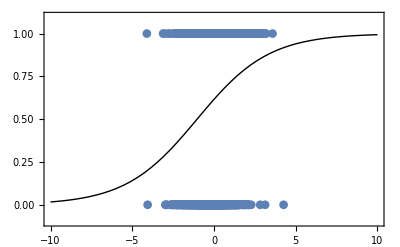

```mathematica
(*ln on x-axis*)
```

```mathematica
Needs["CustomTicks`"]
data=Import["~/Desktop/ExpFiles/exp01-choice-results-KB.csv"];
(*Show when Qhigh > 0*)
highdeltaQChoice=Select[data[[2;;]],#[[9]]>0&&#[[2]]>4&][[;;,{-1,5}]];
Length[highdeltaQChoice]
highdeltaQChoice[[;;,1]]=-highdeltaQChoice[[;;,1]];
highdeltaQChoice[[;;,2]]=1-highdeltaQChoice[[;;,2]];
highglm=LogitModelFit[highdeltaQChoice,x,x];
step=0.5;
highbinned=DeleteCases[Table[
b2=b1+step;
ydat=Select[highdeltaQChoice,b1≤#[[1]]<b2&][[;;,2]];
If[Length[ydat]>0,
{(b2+b1)/2,Mean[ydat]}
]
,{b1,-10,10,step}],Null];


lowdeltaQChoice=Select[data[[2;;]],#[[9]]<=0&&#[[2]]>4&][[;;,{-1,5}]];
Length[lowdeltaQChoice]
lowdeltaQChoice[[;;,1]]=-lowdeltaQChoice[[;;,1]];
lowdeltaQChoice[[;;,2]]=1-lowdeltaQChoice[[;;,2]];
lowglm=LogitModelFit[lowdeltaQChoice,x,x];
step=0.5;
lowbinned=DeleteCases[Table[
b2=b1+step;
ydat=Select[lowdeltaQChoice,b1≤#[[1]]<b2&][[;;,2]];
If[Length[ydat]>0,
{(b2+b1)/2,Mean[ydat]}
]
,{b1,-10,10,step}],Null];
Show[
ListPlot[{highdeltaQChoice,highbinned,lowdeltaQChoice,lowbinned},
PlotMarkers->{"▪",Style["□",FontSize->15],"∘",Style["○",FontSize->15]},
Frame->True,
Axes->False,
PlotRange->{{-2,2},{-0.1,1.1}},
FrameLabel->{
Style["ΔQ",FontFamily->"Arial",FontSize->15,FontColor->Black],Style["P(Top Answer Chosen)",FontFamily->"Arial",FontSize->15,FontColor->Black]},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,1,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[-10,10,2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[-10,10,2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
}
],
Plot[{highglm[x],lowglm[x]},{x,-10,10},PlotStyle->{{Blue,Thick},{Red,Dashed,Thick}}]
]
highglm["ParameterTable"]
lowglm["ParameterTable"]
```

394

606

-Graphics-

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.408945 | 0.105531 | 3.87512 | 0.000106571
x | 0.791777 | 0.198232 | 3.9942 | 0.0000649129

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.226709 | 0.0896226 | 2.52959 | 0.0114195
x | 1.624 | 0.18798 | 8.63924 | 5.65896×10^-18

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.583582 | 0.118466 | 4.92617 | 8.38561×10^-7
x | 0.837769 | 0.425284 | 1.96991 | 0.0488491

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.772756 | 0.0983551 | 7.8568 | 3.94074×10^-15
x | 0.705459 | 0.309213 | 2.28146 | 0.022521

```mathematica
(*no count: mean standard. Top>mean (blue) vs top < mean (red)*)
```

-Graphics-

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.625536 | 0.104996 | 5.95774 | 2.55752×10^-9
x | 0.257003 | 0.122819 | 2.09253 | 0.0363909

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.784104 | 0.109751 | 7.14438 | 9.04045×10^-13
x | 0.41743 | 0.151041 | 2.76369 | 0.00571518

```mathematica
(*count: mean standard. Top>mean (blue) vs top < mean (red)*)
```

-Graphics-

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.513334 | 0.0919922 | 5.58019 | 2.40249×10^-8
x | 0.50855 | 0.105956 | 4.79966 | 1.58937×10^-6

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0457378 | 0.102803 | 0.444907 | 0.656387
x | 1.26384 | 0.152885 | 8.26658 | 1.37853×10^-16

```mathematica
(*Average = standard for Q: top>mean, bottom > mean(blue) vs top<=mean, bottom≤mean (red): count*)
```

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.461541 | 0.132053 | 3.49513 | 0.00047383
x | 0.42626 | 0.148663 | 2.86729 | 0.00414007

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0178478 | 0.148709 | 0.120018 | 0.904469
x | 1.50918 | 0.234001 | 6.44947 | 1.12241×10^-10

```mathematica
(*Average = standard for Q: top>mean, bottom > mean (blue) vs top<=mean, bottom≤mean (red): no count*)
```

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.630975 | 0.149673 | 4.2157 | 0.0000249006
x | 0.103908 | 0.174876 | 0.594179 | 0.552393

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.05668 | 0.159916 | 6.6077 | 3.90332×10^-11
x | 0.300191 | 0.226211 | 1.32704 | 0.184495

```mathematica
(*Average = standard for Q: top>mean, bottom ≤mean (blue) vs top≤mean, bottom>mean (red): no count*)
```

-Graphics-

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.615865 | 0.147847 | 4.16557 | 0.0000310579
x | 0.402069 | 0.173162 | 2.32193 | 0.0202367

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.517876 | 0.154685 | 3.34795 | 0.000814116
x | 0.444592 | 0.205712 | 2.16123 | 0.0306777

```mathematica
(*Average = standard for Q: top>mean, bottom ≤ mean (blue) vs top≤mean, bottom>mean(red): count*)
```

-Graphics-

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.55918 | 0.128414 | 4.3545 | 0.0000133369
x | 0.588171 | 0.151463 | 3.88328 | 0.000103058

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0870054 | 0.142879 | 0.608945 | 0.542561
x | 1.04332 | 0.200375 | 5.20684 | 1.9208×10^-7

```mathematica
(*Average = standard for Q: top>true, bottom < true (blue) vs top<true, bottom>true (red)*)
```

-Graphics-

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.62546 | 0.094024 | 6.65213 | 2.88888×10^-11
x | 0.49861 | 0.109729 | 4.54403 | 5.5189×10^-6

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.2583 | 0.0965325 | 2.67578 | 0.0074555
x | 0.679502 | 0.127233 | 5.3406 | 9.26401×10^-8

```mathematica
(*True = standard for Q: top>true, bottom < true (blue) vs top<true, bottom>true (red)*)
```

-Graphics-

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.445243 | 0.104698 | 4.25262 | 0.0000211281
x | 0.252572 | 0.110811 | 2.27929 | 0.0226496

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.662597 | 0.11423 | 5.80057 | 6.60905×10^-9
x | 0.21694 | 0.119366 | 1.81743 | 0.0691506

```mathematica
(*Top > mean, bottom ≤ mean (blue, 178 points), vs top ≤ mean, bottom > mean (red, 144 points): count (Q5-10)*)
```

-Graphics-

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.000532572 | 0.171324 | 0.00310856 | 0.99752
x | 0.266154 | 0.162561 | 1.63725 | 0.101578

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.23756 | 0.242891 | 5.09513 | 3.485×10^-7
x | 0.626041 | 0.223583 | 2.80004 | 0.00510969

```mathematica
(*Top > mean, bottom ≤ mean (blue, 178 points), vs top ≤ mean, bottom > mean (red, 169 points): no count (Q1-3)*)
```

-Graphics-

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.02716 | 0.19072 | 5.38566 | 7.21797×10^-8
x | 0.730561 | 0.208342 | 3.50655 | 0.00045396

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.494099 | 0.17182 | 2.87568 | 0.00403163
x | 0.145362 | 0.179168 | 0.811317 | 0.417184

```mathematica
(*both > true (blue, 307 points) vs both < true (red, 155 points): no count (Q1-3)*)
```

-Graphics-

```mathematica
High: {{"", "Estimate", "Standard Error", "z-Statistic", "P-Value"}, {1, 0.6841340419311787, 0.12180649465907019, 5.616564566988262, 1.9479148100817676*^-8}, {x, 0.1802844819328913, 0.12538451550236548, 1.437852841800789, 0.15047581254439768}}
```

```mathematica
Low: {{"", "Estimate", "Standard Error", "z-Statistic", "P-Value"}, {1, 0.8329688730222823, 0.17740777910830113, 4.695221805994112, 2.6631758615199403*^-6}, {x, 0.36166365376076237, 0.24186361149886945, 1.4953206541466568, 0.13483077723947856}}
```

```mathematica
(*both > true (blue, 42 points) vs both < true (red, 636 points): count (Q5-10)*)
```

```mathematica
(*bottom answer > mean  vs bottom answer < mean *)
```

-Graphics-

```mathematica
(*top answer > mean and bottom answer < mean vs top answer < mean and bottom anwer > mean*)
```

-Graphics-

```mathematica
(*top answer > mean vs top answer < mean*)
```

-Graphics-

```mathematica
(*top and bottom are > mean (blue), vs. top and bottom < mean*)
```

-Graphics-

```mathematica
Needs["CustomTicks`"]
data=Import["~/Desktop/ExpFiles/exp01-choice-results-KB.csv"];
(*Show when Counting problems*)
countdeltaQChoice=Select[data[[2;;]],#[[2]]≥4&][[;;,{-1,5}]];
countdeltaQChoice[[;;,1]]=-countdeltaQChoice[[;;,1]];
countdeltaQChoice[[;;,2]]=1-countdeltaQChoice[[;;,2]];
countglm=LogitModelFit[countdeltaQChoice,x,x];
step=2;
countbinned=DeleteCases[Table[
b2=b1+step;
ydat=Select[countdeltaQChoice,b1≤#[[1]]<b2&][[;;,2]];
If[Length[ydat]>0,
{(b2+b1)/2,Mean[ydat]}
]
,{b1,-10,10,step}],Null];


nocountdeltaQChoice=Select[data[[2;;]],#[[2]]<4&][[;;,{-1,5}]];
nocountdeltaQChoice[[;;,1]]=-nocountdeltaQChoice[[;;,1]];
nocountdeltaQChoice[[;;,2]]=1-nocountdeltaQChoice[[;;,2]];
nocountglm=LogitModelFit[nocountdeltaQChoice,x,x];
step=2;
nocountbinned=DeleteCases[Table[
b2=b1+step;
ydat=Select[nocountdeltaQChoice,b1≤#[[1]]<b2&][[;;,2]];
If[Length[ydat]>0,
{(b2+b1)/2,Mean[ydat]}
]
,{b1,-10,10,step}],Null];
Show[
ListPlot[{countdeltaQChoice,countbinned,nocountdeltaQChoice,nocountbinned},
PlotMarkers->{"▪",Style["□",FontSize->15],"∘",Style["○",FontSize->15]},
Frame->True,
Axes->False,
PlotRange->{{-7,7},{-0.1,1.1}},
FrameLabel->{
Style["ΔQ",FontFamily->"Arial",FontSize->15,FontColor->Black],Style["P(Top Answer Chosen)",FontFamily->"Arial",FontSize->15,FontColor->Black]},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,1,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[-10,10,2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[-10,10,2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
}
],
Plot[{countglm[x],nocountglm[x]},{x,-10,10},PlotStyle->{{Blue,Thick},{Red,Dashed,Thick}}]
]
```

-Graphics-

```mathematica
Needs["CustomTicks`"]
data=Import["~/Desktop/ExpFiles/exp01-choice-results-KB.csv"];
(*Show when Counting problems*)
countQChoice=Select[data[[2;;]],#[[2]]≥4&][[;;,{8,5}]];
countQChoice[[;;,1]]=-countQChoice[[;;,1]];
countQChoice[[;;,2]]=1-countQChoice[[;;,2]];
countglm=LogitModelFit[countQChoice,x,x];
step=0.5;
countbinned=DeleteCases[Table[
b2=b1+step;
ydat=Select[countQChoice,b1≤#[[1]]<b2&][[;;,2]];
If[Length[ydat]>0,
{(b2+b1)/2,Mean[ydat]}
]
,{b1,-10,10,step}],Null];


nocountQChoice=Select[data[[2;;]],#[[2]]<4&][[;;,{8,5}]];
nocountQChoice[[;;,1]]=-nocountQChoice[[;;,1]];
nocountQChoice[[;;,2]]=1-nocountQChoice[[;;,2]];
nocountglm=LogitModelFit[nocountQChoice,x,x];
step=0.5;
nocountbinned=DeleteCases[Table[
b2=b1+step;
ydat=Select[nocountQChoice,b1≤#[[1]]<b2&][[;;,2]];
If[Length[ydat]>0,
{(b2+b1)/2,Mean[ydat]}
]
,{b1,-10,10,step}],Null];
Show[
ListPlot[{countQChoice,countbinned,nocountQChoice,nocountbinned},
PlotMarkers->{"▪",Style["□",FontSize->15],"∘",Style["○",FontSize->15]},
Frame->True,
Joined->{False,True,False,True},
Axes->False,
PlotRange->{{-7,7},{-0.1,1.1}},
FrameLabel->{
Style["Q",FontFamily->"Arial",FontSize->15,FontColor->Black],Style["P(Top Answer Chosen)",FontFamily->"Arial",FontSize->15,FontColor->Black]},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,1,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[-10,10,2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[-10,10,2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
}
]
]
```

```mathematica
(*counting dots/letters (squares) vs non-counting things (circles)*)
```

-Graphics-

```mathematica
Needs["CustomTicks`"]
data=Import["~/Desktop/ExpFiles/exp01-choice-results-KB.csv"];
(*Show when Qhigh < 0*)
deltaQChoice=Select[data[[2;;]],#[[8]]<0&][[;;,{-1,5}]];
deltaQChoice[[;;,1]]=-deltaQChoice[[;;,1]];
deltaQChoice[[;;,2]]=1-deltaQChoice[[;;,2]];
glm=LogitModelFit[deltaQChoice,x,x];
step=2;
binned=DeleteCases[Table[
b2=b1+step;
ydat=Select[deltaQChoice,b1≤#[[1]]<b2&][[;;,2]];
If[Length[ydat]>0,
{(b2+b1)/2,Mean[ydat]}
]
,{b1,-10,10,step}],Null];
Show[
ListPlot[{deltaQChoice,binned},
PlotMarkers->{"▪",Style["□",FontSize->15]},
Frame->True,
Axes->False,
PlotRange->{{-7,7},{-0.1,1.1}},
FrameLabel->{
Style["ΔQ",FontFamily->"Arial",FontSize->15,FontColor->Black],Style["P(Top Answer Chosen)",FontFamily->"Arial",FontSize->15,FontColor->Black]},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,1,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[-10,10,2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[-10,10,2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
}
],
Plot[glm[x],{x,-10,10},PlotStyle->{Black,Thick}]
]
```

-Graphics-

```mathematica
Do[
QChoice=data[[2;;,{If[rank=="Top",8,9],5}]];
If[rank=="Top",
QChoice[[;;,2]]=1-QChoice[[;;,2]];
];

glm=LogitModelFit[QChoice,x,x];
step=1;
binned=DeleteCases[Table[
b2=b1+step;
ydat=Select[QChoice,b1≤#[[1]]<b2&][[;;,2]];
If[Length[ydat]>0,
{(b2+b1)/2,Mean[ydat]}
]
,{b1,-10,10,step}],Null];
Print[Show[
ListPlot[{QChoice,binned},
PlotMarkers->{"▪",Style["□",FontSize->15]},
Frame->True,
Axes->False,
PlotRange->{{-7,7},{-0.1,1.1}},
FrameLabel->{
Style["Q",FontFamily->"Arial",FontSize->15,FontColor->Black],Style["P("<>rank<>" Answer Chosen)",FontFamily->"Arial",FontSize->15,FontColor->Black]},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,1,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[-10,10,2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[-10,10,2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
}
](*,
Plot[glm[x],{x,-10,10},PlotStyle->{Black,Thick}]*)
]];
,
{rank,{"Top","Bottom"}}
]
```

-Graphics-

-Graphics-

```mathematica
Integrate[2 PDF[NormalDistribution[0,1],xb] 2 PDF[NormalDistribution[0,1],xt],{xb,0,xt}]
```

```mathematica
(*New model:*)
Prank1[xt_,xb_,α_]:=1/(1+1/α Exp[(xt**2-xb**2)/2]);
Plot3D[Prank1[xt,xb,10],{xt,-10,10},{xb,-10,10}]

(*New model:*)
Prank2[xt_,xb_,α_]:=1/(1+Exp[-xb**2/2]/(α+Exp[-xt**2/2]));
Plot3D[Prank2[xt,xb,0.04],{xt,-10,10},{xb,-10,10},PlotRange->All]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*Raw data plot*)
(*functions*)
Needs["CustomTicks`"];
Needs["ErrorBarPlots`"];

PrankMult[xt_,xb_,α_]:=1/(1+1/α Exp[(xt**2-xb**2)/2]);
PrankMultDiff[SqDiff_,α_]:=1/(1+1/α Exp[(SqDiff)/2]);
PrankAdd[xt_,xb_,α_]:=1/(1+Exp[-xb**2/2]/(α+Exp[-xt**2/2]));

Shape[shape_,in_,size_: 15]:=
Which[shape=="Square",Graphics[{in,EdgeForm[{AbsoluteThickness[2],Black}],Rectangle[]},PlotRangePadding->0,ImageSize->size],
shape=="Circle",
Graphics[{in,EdgeForm[{AbsoluteThickness[2],Black}],Disk[]},PlotRangePadding->0,ImageSize->size],
shape=="Triangle",
Graphics[{in,EdgeForm[{AbsoluteThickness[2],Black}],Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]} ,PlotRangePadding->0,ImageSize->size],
shape=="Diamond",
Graphics[{in,EdgeForm[{AbsoluteThickness[2],Black}],Polygon[{{1,0},{0,1},{-1,0},{0,-1}}]} ,PlotRangePadding->0,ImageSize->size]
];

(*params*)
MultBest=1.55;
AddBest=0.3;
NullMultBest=1.1;
NullAddBest=0.035;
binwidtht=1.1;
binwidthb=0.5;
binwidth=1;

(*data*)
data=Import["~/Dropbox/ExpFiles/QChoiceData.csv"][[2;;,2;;4]];
Nulldata=Import["~/Dropbox/ExpFiles/NULL-DATA_QChoiceData.csv"][[2;;,2;;4]];
(*parseddata*)
BinnedQhighQlow=Table[
dat=Select[data,xt-binwidtht/2<#[[1]]<=xt+binwidtht/2&&xb-binwidthb/2<#[[2]]<=xb+binwidthb/2&];
If[Length[dat]>5,
b=BootstrapMean[dat[[;;,3]]];
m=b[[1]];
intervals=b[[2]]-m;
{xt,xb,m,intervals},
{xt,xb,Null,Null}
]
,{xt,-4,4,binwidtht}
,{xb,-3,3,binwidthb}];
NullBinnedQhighQlow=Table[
dat=Select[Nulldata,xt-binwidtht/2<#[[1]]<=xt+binwidtht/2&&xb-binwidthb/2<#[[2]]<=xb+binwidthb/2&];
If[Length[dat]>5,
b=BootstrapMean[dat[[;;,3]]];
m=b[[1]];
intervals=b[[2]]-m;
{xt,xb,m,intervals},
{xt,xb,Null,Null}
]
,{xt,-4,4,binwidtht}
,{xb,-3,3,binwidthb}];

BinnedDiffQhighQlow=Table[
dat=Select[data,diff≤#[[1]]**2-#[[2]]**2<diff+binwidth&];
If[Length[dat]>2,
b=BootstrapMean[dat[[;;,3]]];
m=b[[1]];
intervals=b[[2]]-m;
{{diff+binwidth/2,m},ErrorBar[intervals]}
]
,{diff,-7,7,binwidth}];


NullBinnedDiffQhighQlow=Table[
dat=Select[Nulldata,diff≤#[[1]]**2-#[[2]]**2<diff+binwidth&];
If[Length[dat]>2,
b=BootstrapMean[dat[[;;,3]]];
m=b[[1]];
intervals=b[[2]]-m;
{{diff+binwidth/2,m},ErrorBar[intervals]}
]
,{diff,-7,7,binwidth}];

(*plots*)
Labeled[Show[
ListPointPlot3D[Flatten[BinnedQhighQlow,1][[;;,;;3]],
PlotRange->{{-4,4},{-3.5,3}},PlotTheme->{Black},ImageSize->500,AxesStyle->Gray,TicksStyle->Directive["Label",Black,14]],
Plot3D[PrankMult[xt,xb,MultBest],{xt,-4,4},{xb,-4,4},PlotStyle->Opacity[0.5]]
],{Rotate[Style["P(Top)",15],90 Degree],Rotate[Style["Q_top",15],0 Degree],Rotate[Style["Q_bottom",15],60 Degree],BaselinePosition->Right},{Left,Bottom,Right}]


Labeled[Show[
ListPointPlot3D[Flatten[BinnedQhighQlow,1][[;;,;;3]],PlotRange->{{-4,4},{-3.5,3}},PlotTheme->{Black},ImageSize->500,AxesStyle->Gray,TicksStyle->Directive["Label",Black,14]],
Plot3D[PrankAdd[xt,xb,AddBest],{xt,-4,4},{xb,-4,4},PlotStyle->Opacity[0.5]]
],{Rotate[Style["P(Top)",15],90 Degree],Rotate[Style["Q_top",15],0 Degree],Rotate[Style["Q_bottom",15],60 Degree],BaselinePosition->Right},{Left,Bottom,Right}]


Labeled[Show[
ListPointPlot3D[Flatten[BinnedQhighQlow,1][[;;,;;3]],PlotRange->{{-4,4},{-3.5,3}},PlotTheme->{Black},ImageSize->500,AxesStyle->Gray,TicksStyle->Directive["Label",Black,14]],
Plot3D[PrankAdd[xt,xb,0],{xt,-4,4},{xb,-4,4},PlotStyle->Opacity[0.5]]
],{Rotate[Style["P(Top)",15],90 Degree],Rotate[Style["Q_top",15],0 Degree],Rotate[Style["Q_bottom",15],60 Degree],BaselinePosition->Right},{Left,Bottom,Right}]



Show[
Plot[PrankMultDiff[SqDiff,MultBest],{SqDiff,-7,7},
PlotStyle->{Red,Thick},

PlotRange->{{-7,7},{0,1}},
Frame->True,
Axes->False,
FrameLabel->{
Style["Q_top^2-Q_bottom^2",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["P(Top)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{

{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[-10,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-10,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}
],
Plot[PrankMultDiff[SqDiff,1],{SqDiff,-7,7},PlotStyle->{Gray,Thick,Dashed}],
ErrorListPlot[BinnedDiffQhighQlow,
Joined->False,
PlotStyle->{Black,Thick}
],
ListPlot[BinnedDiffQhighQlow[[;;,1]],
PlotMarkers->Shape["Circle",White,9],
PlotStyle->{Black,Thick}
]
]

Print["Null:"];
Labeled[Show[
ListPointPlot3D[Flatten[NullBinnedQhighQlow,1][[;;,;;3]],
PlotRange->{{-4,4},{-3.5,3}},PlotTheme->{Black},ImageSize->500,AxesStyle->Gray,TicksStyle->Directive["Label",Black,14]],
Plot3D[PrankMult[xt,xb,NullMultBest],{xt,-4,4},{xb,-4,4},PlotStyle->Opacity[0.5]]
],{Rotate[Style["P(Top)",15],90 Degree],Rotate[Style["Q_top",15],0 Degree],Rotate[Style["Q_bottom",15],60 Degree],BaselinePosition->Right},{Left,Bottom,Right}]


Labeled[Show[
ListPointPlot3D[Flatten[NullBinnedQhighQlow,1][[;;,;;3]],PlotRange->{{-4,4},{-3.5,3}},PlotTheme->{Black},ImageSize->500,AxesStyle->Gray,TicksStyle->Directive["Label",Black,14]],
Plot3D[PrankAdd[xt,xb,NullAddBest],{xt,-4,4},{xb,-4,4},PlotStyle->Opacity[0.5]]
],{Rotate[Style["P(Top)",15],90 Degree],Rotate[Style["Q_top",15],0 Degree],Rotate[Style["Q_bottom",15],60 Degree],BaselinePosition->Right},{Left,Bottom,Right}]


Labeled[Show[
ListPointPlot3D[Flatten[NullBinnedQhighQlow,1][[;;,;;3]],PlotRange->{{-4,4},{-3.5,3}},PlotTheme->{Black},ImageSize->500,AxesStyle->Gray,TicksStyle->Directive["Label",Black,14]],
Plot3D[PrankAdd[xt,xb,0],{xt,-4,4},{xb,-4,4},PlotStyle->Opacity[0.5]]
],{Rotate[Style["P(Top)",15],90 Degree],Rotate[Style["Q_top",15],0 Degree],Rotate[Style["Q_bottom",15],60 Degree],BaselinePosition->Right},{Left,Bottom,Right}]



Show[
Plot[PrankMultDiff[SqDiff,NullMultBest],{SqDiff,-7,7},
PlotStyle->{Red,Thick},

PlotRange->{{-7,7},{0,1}},
Frame->True,
Axes->False,
FrameLabel->{
Style["Q_top^2-Q_bottom^2",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["P(Top)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{

{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[-10,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-10,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}
],
Plot[PrankMultDiff[SqDiff,1],{SqDiff,-7,7},PlotStyle->{Gray,Thick,Dashed}],
ErrorListPlot[NullBinnedDiffQhighQlow,
Joined->False,
PlotStyle->{Black,Thick}
],
ListPlot[NullBinnedDiffQhighQlow[[;;,1]],
PlotMarkers->Shape["Square",Cyan,9],
PlotStyle->{Black,Thick}
]
]
```

-Graphics3D-P(Top)Q_topQ_bottomBaselinePosition→Right

-Graphics3D-P(Top)Q_topQ_bottomBaselinePosition→Right

-Graphics3D-P(Top)Q_topQ_bottomBaselinePosition→Right

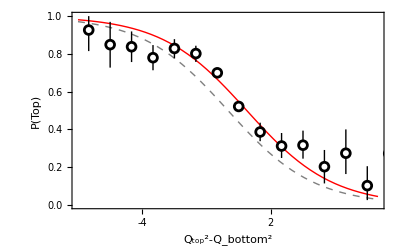

Null:

-Graphics3D-P(Top)Q_topQ_bottomBaselinePosition→Right

-Graphics3D-P(Top)Q_topQ_bottomBaselinePosition→Right

-Graphics3D-P(Top)Q_topQ_bottomBaselinePosition→Right

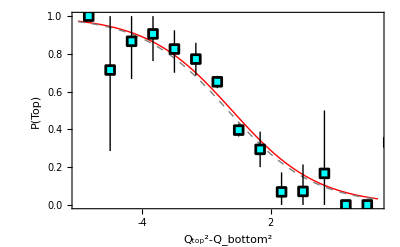

```mathematica
(*6/28/2019 all data (600 workers for ranked choice)*)
```

```mathematica
qdata=Import["~/Dropbox/ExpFiles/QChoiceData.csv"][[2;;]];
questionBinnedDiffQhighQlow=Table[
dat=Select[qdata,#[[1]]==q&&diff≤#[[2]]**2-#[[3]]**2<diff+binwidth&][[;;,2;;4]];
If[Length[dat]>2,
b=BootstrapMean[dat[[;;,3]]];
m=b[[1]];
intervals=b[[2]]-m;
{{diff+binwidth/2+RandomReal[{-0.2,0.2}],m},ErrorBar[intervals]}
]
,{q,10}
,{diff,-7,7,binwidth}];

Show[
Plot[PrankMultDiff[SqDiff,MultBest],{SqDiff,-7,7},
PlotStyle->{Red,Thick},

PlotRange->{{-7,7},{0,1}},
Frame->True,
Axes->False,
FrameLabel->{
Style["Q_top^2-Q_bottom^2",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["P(Top)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{

{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[-10,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-10,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}
],
Plot[PrankMultDiff[SqDiff,1],{SqDiff,-7,7},PlotStyle->{Gray,Thick,Dashed}],
ErrorListPlot[Table[DeleteCases[questionBinnedDiffQhighQlow[[q]],Null],{q,10}],
Joined->False
],
ListPlot[Table[DeleteCases[questionBinnedDiffQhighQlow[[q]],Null][[;;,1]],{q,10}],
PlotMarkers->Automatic,
Joined->True,
PlotLegends->Table[Style[ToString[q],FontSize->12,FontFamily->"Arial"],{q,10}](*,
LegendLabel->Style["Question",FontSize->15,FontFamily->"Arial"]*)
]
]
```

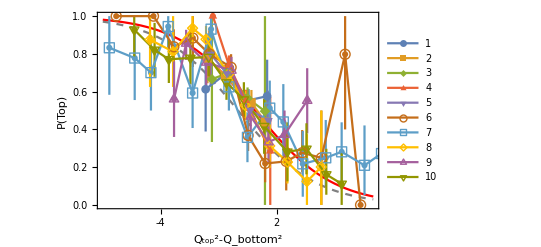

```mathematica
(*6/28/2019 newest data*)
```

```mathematica
xtBinnedDiffQhighQlow=
Table[
vals=DeleteCases[
Table[
dat=Select[data,xt-binwidtht/2≤#[[1]]<xt+binwidtht/2&&diff≤#[[1]]**2-#[[2]]**2<diff+binwidth&];
If[Length[dat]>2,
b=BootstrapMean[dat[[;;,3]]];
m=b[[1]];
intervals=b[[2]]-m;
{{diff+binwidth/2+RandomReal[{-0.2,0.2}],m},ErrorBar[intervals]}
]
,{diff,-7,7,binwidth}],Null];
If[Length[vals]>0,
vals,
Table[
{{diff+binwidth/2+RandomReal[{-0.2,0.2}],Null},ErrorBar[0]}
,{diff,-7,7,binwidth}]
]
,{xt,-4,4,2}];

Show[
Plot[PrankMultDiff[SqDiff,MultBest],{SqDiff,-7,7},
PlotStyle->{Red,Thick},

PlotRange->{{-7,7},{0,1}},
Frame->True,
Axes->False,
FrameLabel->{
Style["Q_top^2-Q_bottom^2",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["P(Top)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{

{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[-10,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-10,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}
],
Plot[PrankMultDiff[SqDiff,1],{SqDiff,-7,7},PlotStyle->{Gray,Thick,Dashed}],
ErrorListPlot[Table[xtBinnedDiffQhighQlow[[xt]],{xt,Length[xtBinnedDiffQhighQlow]}],
Joined->False
],
ListPlot[Table[xtBinnedDiffQhighQlow[[xt]][[;;,1]],{xt,Length[xtBinnedDiffQhighQlow]}],
PlotMarkers->Automatic,
PlotLegends->Table[Style[ToString[xt],FontFamily->"Arial",FontSize->12],{xt,-4,4,2}],
Joined->True
]
]
```

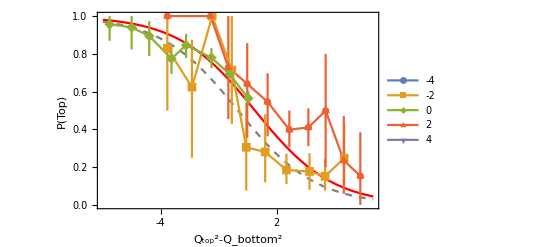

```mathematica
(*newest data 6/24/2019*)
```

```mathematica
CloserModel[Qt_,Qb_]:=If[Qt>Qb,1/2 Erfc[(Qt+Qb)/2],1/2 (1+Erf[(Qt+Qb)/2])];


Labeled[Show[
ListPointPlot3D[Flatten[BinnedQhighQlow,1][[;;,;;3]],
PlotRange->{{-4,4},{-3.5,3}},PlotTheme->{Black},ImageSize->500,AxesStyle->Gray,TicksStyle->Directive["Label",Black,14]],
Plot3D[CloserModel[Qt,Qb],{Qt,-4,4},{Qb,-4,4},PlotStyle->Opacity[0.5]]
],{Rotate[Style["P(Top)",15],90 Degree],Rotate[Style["Q_top",15],0 Degree],Rotate[Style["Q_bottom",15],60 Degree],BaselinePosition->Right},{Left,Bottom,Right}]


Labeled[Show[
ListPointPlot3D[Flatten[NullBinnedQhighQlow,1][[;;,;;3]],
PlotRange->{{-4,4},{-3.5,3}},PlotTheme->{Black},ImageSize->500,AxesStyle->Gray,TicksStyle->Directive["Label",Black,14]],
Plot3D[CloserModel[Qt,Qb],{Qt,-4,4},{Qb,-4,4},PlotStyle->Opacity[0.5]]
],{Rotate[Style["P(Top)",15],90 Degree],Rotate[Style["Q_top",15],0 Degree],Rotate[Style["Q_bottom",15],60 Degree],BaselinePosition->Right},{Left,Bottom,Right}]
```

-Graphics3D-P(Top)Q_topQ_bottomBaselinePosition→Right

-Graphics3D-P(Top)Q_topQ_bottomBaselinePosition→Right

```mathematica
CloserModel[Qt_,Qb_]:=If[Qt>Qb,1/2 Erfc[(Qt+Qb)/2],1/2 (1+Erf[(Qt+Qb)/2])];
CloserModelRank[Qt_,Qb_,a_]:=If[Qt>Qb,1/2 Erfc[(Qt+Qb)/2-a],1/2 (1+Erf[(Qt+Qb)/2+a])];
CloserModelRank2[Qt_,Qb_,a_]:=If[Qt>Qb,1/2 Erfc[(Qt+Qb)/2/a],1/2 (1+Erf[(Qt+Qb)/2*a])];
(*bias data*)
lnpCloser=Table[
qt=line[[1]];
qb=line[[2]];
i=line[[3]];
i Log[CloserModel[qt,qb]]+(1-i) Log[1-CloserModel[qt,qb]]
,{line,data}];
lnpNull=Table[
qt=line[[1]];
qb=line[[2]];
i=line[[3]];
i Log[PrankMult[qt,qb,1]]+(1-i) Log[1-PrankMult[qt,qb,1]]
,{line,data}];
Var=Variance[lnpCloser-lnpNull];
n=Length[lnpCloser];
r=Total[lnpCloser-lnpNull];
rnorm=r/Sqrt[2 n Var]
Erfc[Abs[rnorm]]

closerA=0
lnpRankCloser=Table[
qt=line[[1]];
qb=line[[2]];
i=line[[3]];
i Log[CloserModelRank[qt,qb,closerA]]+(1-i) Log[1-CloserModelRank[qt,qb,closerA]]
,{line,data}];
Table[
lnpRankCloser2=Table[
qt=line[[1]];
qb=line[[2]];
i=line[[3]];
i Log[CloserModelRank2[qt,qb,closerA2]]+(1-i) Log[1-CloserModelRank2[qt,qb,closerA2]]
,{line,data}];

lnpFit=Table[
qt=line[[1]];
qb=line[[2]];
i=line[[3]];
i Log[PrankMult[qt,qb,MultBest]]+(1-i) Log[1-PrankMult[qt,qb,MultBest]]
,{line,data}];
(*
Var=Variance[lnpRankCloser-lnpFit];
n=Length[lnpRankCloser];
r=Total[lnpRankCloser-lnpFit];
rnorm=r/Sqrt[2 n Var]
Erfc[Abs[rnorm]]
*)
Var=Variance[lnpRankCloser2-lnpFit];
n=Length[lnpRankCloser2];
r=Total[lnpRankCloser2-lnpFit];
rnorm=r/Sqrt[2 n Var];
Print[rnorm];
Erfc[Abs[rnorm]]
,{closerA2,0.7,2.0,0.1}]
```

-3.5054

7.14485×10^-7

0

-6.70775

-5.98528

-5.51262

-5.28781

-5.26583

-5.38287

-5.58

-5.81416

-6.05802

-6.29593

Indeterminate

Indeterminate

Indeterminate

«1 more identical outputs»

{2.39631×10^-21,2.57341×10^-17,6.3887×10^-15,7.54111×10^-14,9.54756×10^-14,2.68796×10^-14,2.99013×10^-15,1.99361×10^-16,1.05906×10^-17,5.39747×10^-19,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

```mathematica
(*null data*)
lnp=Table[
qt=line[[1]];
qb=line[[2]];
i=line[[3]];
i Log[CloserModel[qt,qb]]+(1-i) Log[1-CloserModel[qt,qb]]
,{line,Nulldata}];
Total[lnp]
lnpNull=Table[
qt=line[[1]];
qb=line[[2]];
i=line[[3]];
i Log[PrankMult[qt,qb,1]]+(1-i) Log[1-PrankMult[qt,qb,1]]
,{line,Nulldata}];
Total[lnpNull]
Var=Variance[lnp-lnpNull];
n=Length[lnp];
r=Total[lnp-lnpNull];
rnorm=r/Sqrt[2 n Var]
Erfc[Abs[rnorm]]
```

-1190.15

-1233.38

1.89666

0.00731232

0.5

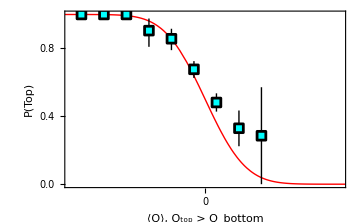

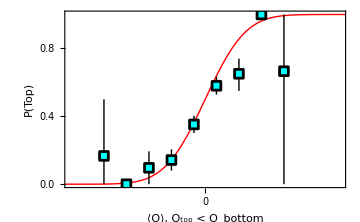

```mathematica
CloserModelQtOverQb[Av]:=1/2 Erfc[Av];
CloserModelQbOverQt[Av]:=1/2 (1+Erf[Av]);
binwidth=0.5
NullBinnedAvQhighQlowQtOverQb=DeleteCases[Table[
dat=Select[Nulldata,diff≤(#[[1]]+#[[2]])/2<diff+binwidth&&#[[1]]>#[[2]]&];
If[Length[dat]>2,
b=BootstrapMean[dat[[;;,3]]];
m=b[[1]];
intervals=b[[2]]-m;
{{diff+binwidth/2,m},ErrorBar[intervals]}
]
,{diff,-7,7,binwidth}],Null];

NullBinnedAvQhighQlowQbOverQt=DeleteCases[Table[
dat=Select[Nulldata,diff≤(#[[1]]+#[[2]])/2<diff+binwidth&&#[[1]]<#[[2]]&];
If[Length[dat]>2,
b=BootstrapMean[dat[[;;,3]]];
m=b[[1]];
intervals=b[[2]]-m;
{{diff+binwidth/2,m},ErrorBar[intervals]}
]
,{diff,-7,7,binwidth}],Null];

Show[
Plot[CloserModelQtOverQb[Av],{Av,-7,7},
PlotStyle->{Red,Thick},
PlotRange->{{-3,3},{0,1}},
Frame->True,
Axes->False,
FrameLabel->{
Style["⟨Q⟩, Q_top > Q_bottom",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["P(Top)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{

{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[-10,10,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-10,10,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}
],
ErrorListPlot[NullBinnedAvQhighQlowQtOverQb,
Joined->False,
PlotStyle->{Black,Thick}
],
ListPlot[NullBinnedAvQhighQlowQtOverQb[[;;,1]],
PlotMarkers->Shape["Square",Cyan,9],
PlotStyle->{Black,Thick}
]
]


Show[
Plot[CloserModelQbOverQt[Av],{Av,-7,7},
PlotStyle->{Red,Thick},

PlotRange->{{-3,3},{0,1}},
Frame->True,
Axes->False,
FrameLabel->{
Style["⟨Q⟩, Q_top < Q_bottom",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["P(Top)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{

{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[-10,10,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-10,10,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}
],
ErrorListPlot[NullBinnedAvQhighQlowQbOverQt,
Joined->False,
PlotStyle->{Black,Thick}
],
ListPlot[NullBinnedAvQhighQlowQbOverQt[[;;,1]],
PlotMarkers->Shape["Square",Cyan,9],
PlotStyle->{Black,Thick}
]
]
```

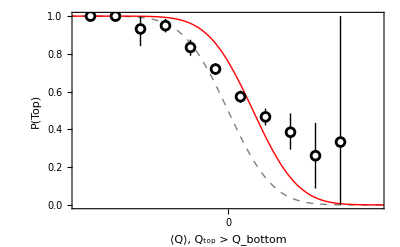

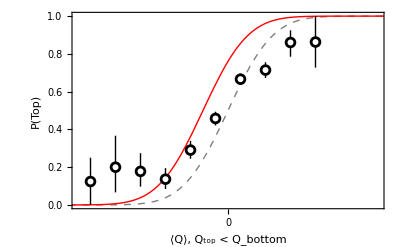

```mathematica
CloserModelQtOverQb[Av_,a_]:=1/2 Erfc[Av-a];
CloserModelQbOverQt[Av_,a_]:=1/2 (1+Erf[Av+a]);

a=0.5;
binwidth=0.5;

BinnedAvQhighQlowQtOverQb=DeleteCases[Table[
dat=Select[data,diff≤(#[[1]]+#[[2]])/2<diff+binwidth&&#[[1]]>#[[2]]&];
If[Length[dat]>2,
b=BootstrapMean[dat[[;;,3]]];
m=b[[1]];
intervals=b[[2]]-m;
{{diff+binwidth/2,m},ErrorBar[intervals]}
]
,{diff,-7,7,binwidth}],Null];

BinnedAvQhighQlowQbOverQt=DeleteCases[Table[
dat=Select[data,diff≤(#[[1]]+#[[2]])/2<diff+binwidth&&#[[1]]<#[[2]]&];
If[Length[dat]>2,
b=BootstrapMean[dat[[;;,3]]];
m=b[[1]];
intervals=b[[2]]-m;
{{diff+binwidth/2,m},ErrorBar[intervals]}
]
,{diff,-7,7,binwidth}],Null];

Show[
Plot[{CloserModelQtOverQb[Av,0],CloserModelQtOverQb[Av,a]},{Av,-7,7},
PlotStyle->{{Gray,Dashed,Thick},{Red,Thick}},
PlotRange->{{-3,3},{0,1}},
Frame->True,
Axes->False,
FrameLabel->{
Style["⟨Q⟩, Q_top > Q_bottom",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["P(Top)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{

{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[-10,10,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-10,10,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}
],
ErrorListPlot[BinnedAvQhighQlowQtOverQb,
Joined->False,
PlotStyle->{Black,Thick}
],
ListPlot[BinnedAvQhighQlowQtOverQb[[;;,1]],
PlotMarkers->Shape["Circle",White,9],
PlotStyle->{Black,Thick}
]
]


Show[
Plot[{CloserModelQbOverQt[Av,0],CloserModelQbOverQt[Av,a]},{Av,-7,7},
PlotStyle->{{Gray,Dashed,Thick},{Red,Thick}},
PlotRange->{{-3,3},{0,1}},
Frame->True,
Axes->False,
FrameLabel->{
Style["⟨Q⟩, Q_top < Q_bottom",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["P(Top)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{

{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[-10,10,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-10,10,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}
],
ErrorListPlot[BinnedAvQhighQlowQbOverQt,
Joined->False,
PlotStyle->{Black,Thick}
],
ListPlot[BinnedAvQhighQlowQbOverQt[[;;,1]],
PlotMarkers->Shape["Circle",White,9],
PlotStyle->{Black,Thick}
]
]
```

{{1.3684,1.44166},{1.26041,1.34679},{1.36906,1.42836},{1.02818,1.44849},{3.57541,1.12771},{5.57277,1.3225},{5.43065,1.21764},{5.90051,1.34876},{6.80343,1.41139},{5.54641,1.16199}}

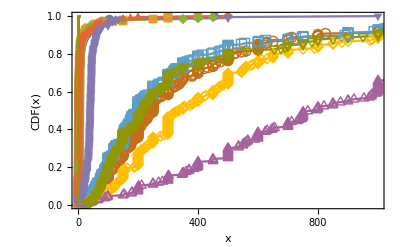

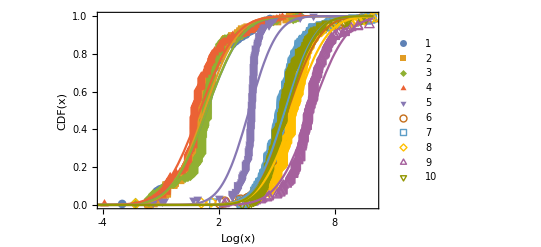

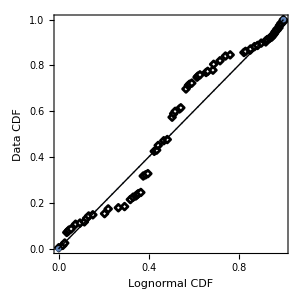

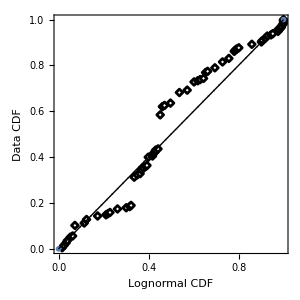

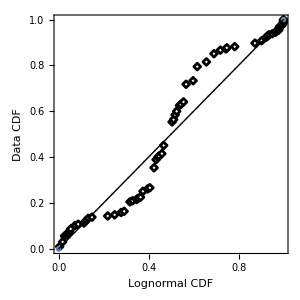

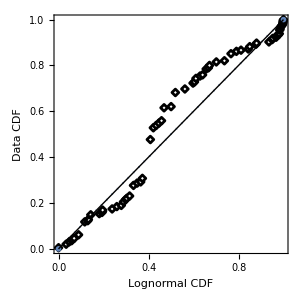

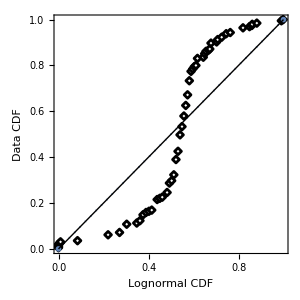

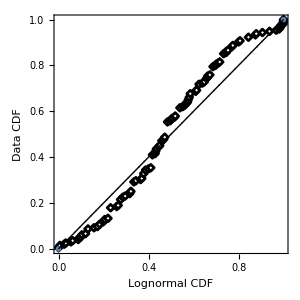

```mathematica
GuessData = Import["~/Dropbox/ExpFiles/GuessesPerQuestion.csv"][[2;;]];
QuestionGuessData=Table[Log[Select[GuessData,#[[1]]==q&][[;;,2]]],{q,10}];
FitQuestionGuessData=Table[Select[QuestionGuessData[[q]],#<Log[10**5]&&#>-10&],{q,10}];

BestFitParams=Table[{Mean[QuestionGuessData[[q]]],StandardDeviation[QuestionGuessData[[q]]]},{q,10}]
cdfQ=Table[{Exp[QuestionGuessData[[q,i]]],Length[QuestionGuessData[[q,;;i]]]/Length[QuestionGuessData[[q]]]},{q,10},{i,Length[QuestionGuessData[[q]]]}];
Show[
ListPlot[cdfQ,
PlotRange->{{0,10**3},{0,1}},
Frame->True,
PlotMarkers->Automatic,
Joined->True,
Axes->False,
FrameLabel->{
Style["x",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["CDF(x)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{

{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[0,10**3,2 10**2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,10**3,2 10**2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}
]
,
Plot[{1/2 Erfc[0.4904822852579593 (1.3683991145499899-Exp[x])],1/2 Erfc[0.5250325638088078 (1.2604088984096555-Exp[x])],1/2 Erfc[0.4950497077980193 (1.369058580648723-Exp[x])],1/2 Erfc[0.4881673746391038 (1.0281823874506923-Exp[x])],1/2 Erfc[0.627027736813686 (3.575413041493743-Exp[x])],1/2 Erfc[0.5346744566166018 (5.572765358503029-Exp[x])],1/2 Erfc[0.5807175860283783 (5.4306502608698-Exp[x])],1/2 Erfc[0.5242649534136216 (5.900512341032161-Exp[x])],1/2 Erfc[0.5010000631272049 (6.80342507377036-Exp[x])],1/2 Erfc[0.6085306548555457 (5.546405658098232-Exp[x])]},{x,-5,10}]
]

cdfQ=Table[{QuestionGuessData[[q,i]],Length[QuestionGuessData[[q,;;i]]]/Length[QuestionGuessData[[q]]]},{q,10},{i,Length[QuestionGuessData[[q]]]}];
Show[
ListPlot[cdfQ,
PlotRange->{{-4,10},{0,1}},
PlotMarkers->Automatic,
Frame->True,
Axes->False,
FrameLabel->{
Style["Log(x)",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["CDF(x)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{

{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[-10,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-10,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
PlotLegends->Table[Style[ToString[q],FontSize->12,FontFamily->"Arial"],{q,10}]
]
,
Plot[{1/2 Erfc[0.4904822852579593 (1.3683991145499899-x)],1/2 Erfc[0.5250325638088078 (1.2604088984096555-x)],1/2 Erfc[0.4950497077980193 (1.369058580648723-x)],1/2 Erfc[0.4881673746391038 (1.0281823874506923-x)],1/2 Erfc[0.627027736813686 (3.575413041493743-x)],1/2 Erfc[0.5346744566166018 (5.572765358503029-x)],1/2 Erfc[0.5807175860283783 (5.4306502608698-x)],1/2 Erfc[0.5242649534136216 (5.900512341032161-x)],1/2 Erfc[0.5010000631272049 (6.80342507377036-x)],1/2 Erfc[0.6085306548555457 (5.546405658098232-x)]},{x,-5,10}]
]

Do[
Print[ProbabilityPlot[FitQuestionGuessData[[q]],
PlotMarkers->Shape["Diamond",White,7],
AspectRatio->1,
Frame->True,
Axes->False,
FrameLabel->{
Style["Lognormal CDF",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Data CDF",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
ImageSize->300
]]
,{q,10}]
```

```mathematica
Table[CDF[NormalDistribution[BestFitParams[[q,1]],BestFitParams[[q,2]]],x],{q,10}]
```

{1/2 Erfc[0.490482 (1.3684-x)],1/2 Erfc[0.525033 (1.26041-x)],1/2 Erfc[0.49505 (1.36906-x)],1/2 Erfc[0.488167 (1.02818-x)],1/2 Erfc[0.627028 (3.57541-x)],1/2 Erfc[0.534674 (5.57277-x)],1/2 Erfc[0.580718 (5.43065-x)],1/2 Erfc[0.524265 (5.90051-x)],1/2 Erfc[0.501 (6.80343-x)],1/2 Erfc[0.608531 (5.54641-x)]}

```mathematica
PrankMultDiff[SqDiff_,α_]:=1/(1+1/α Exp[(SqDiff)/2]);
Solve[PrankMultDiff[x,1.55]==0.5,x]

b=0;
Solve[t**2-b**2==0.8765098618623106,t]
Exp[b]
t=0.9362210539516351;
Exp[t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.87651}}

{{t→-0.936221},{t→0.936221}}

1

2.55033

```mathematica
BootstrapMean[data_]:=Module[
{ResampledList,ResampledMeanDist},
(*Non-resampled bootstrap*)
n=10^4;
ResampledList=ArrayReshape[RandomChoice[data,Length[data] n],{n,Length[data]}];
ResampledMeanDist=Table[Mean[ResampledList[[i]]],{i,Length[ResampledList]}];
Return[N[{Mean[ResampledMeanDist],Quantile[ResampledMeanDist,{0.05,0.95}]}]];
];
Shape[shape_,in_,size_: 15]:=
Which[shape=="Square",Graphics[{in,EdgeForm[{AbsoluteThickness[2],Black}],Rectangle[]},PlotRangePadding->0,ImageSize->size],
shape=="Circle",
Graphics[{in,EdgeForm[{AbsoluteThickness[2],Black}],Disk[]},PlotRangePadding->0,ImageSize->size],
shape=="Triangle",
Graphics[{in,EdgeForm[{AbsoluteThickness[2],Black}],Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]} ,PlotRangePadding->0,ImageSize->size],
shape=="Diamond",
Graphics[{in,EdgeForm[{AbsoluteThickness[2],Black}],Polygon[{{1,0},{0,1},{-1,0},{0,-1}}]} ,PlotRangePadding->0,ImageSize->size]
];
Needs["ErrorBarPlots`"]
Needs["CustomTicks`"]
data=Import["~/Dropbox/ExpFiles/NormGuessesPerQuestion.csv"][[2;;]];
SurveyCodes =DeleteDuplicates[data[[;;,3]]];
OrderedGuesses=Table[Select[data,#[[3]]==sc&][[;;,2]],{sc,SurveyCodes}];
GuessMeans=Table[(*{m,q}=BootstrapMean[g];*)
id=Position[OrderedGuesses,g][[1,1]];
(*{{id,m},ErrorBar[q-m]}*)
{id,Mean[g]}
,{g,OrderedGuesses}];
GuessStd=Table[
id=Position[OrderedGuesses,g][[1,1]];
{id,StandardDeviation[g]}
,{g,OrderedGuesses}];
(*
ErrorListPlot[
GuessMeans
]*)
```

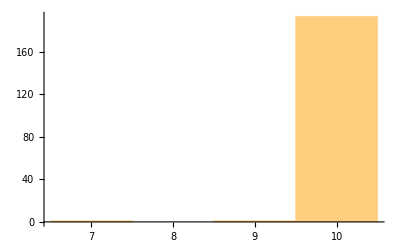

```mathematica
Histogram[Table[Length[g],{g,OrderedGuesses}]]
```

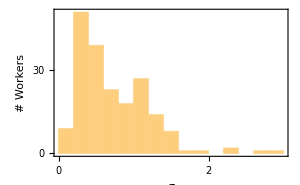

{0.726463,{0.671274,0.783197}}

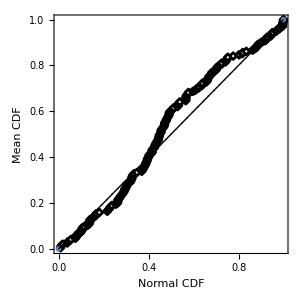

1.00051

0.673989

0.820968

0.326357

0.571277

```mathematica
Histogram[GuessStd[[;;,2]],{0.2},
Frame->True,
Axes->False,
FrameLabel->{
Style["σ",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["# Workers",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,100,10,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,100,10,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[0,5,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,5,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
ImageSize->300
]
(*ListPlot[Sort[GuessMeans[[;;,1,2]]]]
Histogram[GuessVar[[;;,2]],{0.2}]*)
BootstrapMean[GuessStd[[;;,2]]]

(*Histogram[GuessMeans[[;;,1,2]],{0.2}]
BootstrapMean[GuessMeans[[;;,1,2]]]*)
ProbabilityPlot[GuessMeans[[;;,2]],
PlotMarkers->Shape["Diamond",White,7],
AspectRatio->1,
Frame->True,
Axes->False,
FrameLabel->{
Style["Normal CDF",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Mean CDF",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
ImageSize->300
]

TotalVar=N[Variance[Flatten[OrderedGuesses]]]
RandomEffectVar=N[Variance[Flatten[OrderedGuesses-GuessMeans[[;;,2]]]]]
Sqrt[RandomEffectVar]
R2=1-RandomEffectVar/TotalVar
r=Sqrt[R2]
```

True

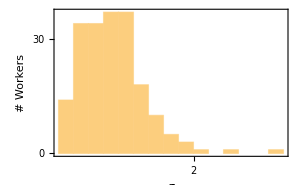

{0.915874,{0.869562,0.964452}}

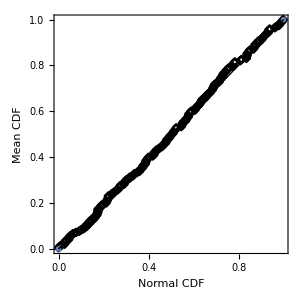

1.00051

0.906635

0.952174

0.0938304

0.306318

```mathematica
RandGuesses=RandomSample[Flatten[OrderedGuesses]];

ReshapedGuesses=Table[
If[i==1,start=1;,
start=Length[Flatten[OrderedGuesses[[;;i-1]]]]+1;
];
end=Length[Flatten[OrderedGuesses[[;;i]]]];
RandGuesses[[start;;end]]
,{i,Length[OrderedGuesses]}];
Table[Length[g],{g,ReshapedGuesses}]==Table[Length[g],{g,OrderedGuesses}]

RandStd=Table[StandardDeviation[g],{g,ReshapedGuesses}];
RandMeans=Table[Mean[g],{g,ReshapedGuesses}];
Histogram[RandStd,{0.2},
Frame->True,
Axes->False,
FrameLabel->{
Style["σ",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["# Workers",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,100,10,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,100,10,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[0,5,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,5,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
ImageSize->300
]
(*ListPlot[Sort[GuessMeans[[;;,1,2]]]]
Histogram[GuessVar[[;;,2]],{0.2}]*)
BootstrapMean[RandStd]

(*Histogram[GuessMeans[[;;,1,2]],{0.2}]
BootstrapMean[GuessMeans[[;;,1,2]]]*)
ProbabilityPlot[RandMeans,
PlotMarkers->Shape["Diamond",White,7],
AspectRatio->1,
Frame->True,
Axes->False,
FrameLabel->{
Style["Normal CDF",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Mean CDF",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
ImageSize->300
]



TotalVar=N[Variance[Flatten[ReshapedGuesses]]]
RandomEffectVar=N[Variance[Flatten[ReshapedGuesses-RandMeans]]]
Sqrt[RandomEffectVar]
R2=1-RandomEffectVar/TotalVar
r=Sqrt[R2]
```

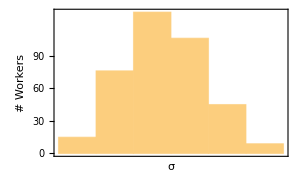

{0.962462,{0.944311,0.98098}}

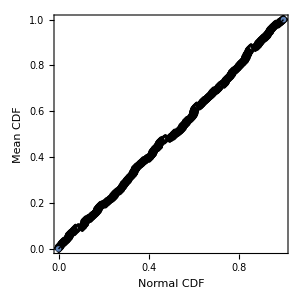

```mathematica
(*if we assume normality, uncorrelated*)
SimGuesses=Table[RandomVariate[NormalDistribution[],10],{Length[data]/10}];

SimStd=Table[StandardDeviation[g],{g,SimGuesses}];
SimMeans=Table[Mean[g],{g,SimGuesses}];


Histogram[SimStd,{0.2},
Frame->True,
Axes->False,
FrameLabel->{
Style["σ",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["# Workers",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,100,10,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,100,10,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[0,5,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,5,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
ImageSize->300
]
(*ListPlot[Sort[GuessMeans[[;;,1,2]]]]
Histogram[GuessVar[[;;,2]],{0.2}]*)
BootstrapMean[SimStd]

(*Histogram[GuessMeans[[;;,1,2]],{0.2}]
BootstrapMean[GuessMeans[[;;,1,2]]]*)
ProbabilityPlot[SimMeans,
PlotMarkers->Shape["Diamond",White,7],
AspectRatio->1,
Frame->True,
Axes->False,
FrameLabel->{
Style["Normal CDF",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Mean CDF",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
ImageSize->300
]
```

```mathematica
(*(*simulations*)
dir="~/Dropbox/ExpFiles/sim_data/"
SetDirectory[dir]
Do[
Print[DQ2];
data=Table[
file="vote_sim_delta_qsquared="<>ToString[DQ2]<>".0_num_recent_votes="<>ToString[NumVotes]<>"_bias="<>ToString[bias]<>"_trial="<>ToString[trial]<>".csv";
Import[file]
,{trial,0,9}];

(*which answer high quality*)
Qs=data[[;;,2;;3,5]];
topQ=Table[Position[Qs[[i]],Max[Qs]][[1,1]]-1,{i,Length[data]}];
(*is top Q on top*)
TopAnswer=data[[;;,2;;,1]];
TopAnswer=Table[DeleteCases[t,""],{t,TopAnswer}];
TopQOnTop=Table[Table[If[t==topQ[[i]],1,0],{t,TopAnswer[[i]]}],{i,Length[data]}];

ProbTopQOnTop=Table[
Table[
p=Total[TopQOnTop[[trial,1+(i-1) 100;;(i) 100]]]/100.0;
{i 100-50,p}
,{i,Round[Length[TopQOnTop[[trial]]]/100]}]
,{trial,10}];
(*position*)
(*Pos=DeleteCases[data[[2;;,1]],""];*)
Print[ListLinePlot[ProbTopQOnTop]];
(*,{file,FileNames[]}]*)

,{DQ2,-7,7}
,{NumVotes,{1000}(*{1,10,50,100,1000}*)}
,{bias,{0.1}(*{0.1,0.5,0.7}*)}]
*)
Needs["CustomTicks`"]
PBestChosen=Table[
(*
bias: probability to choose answer 1
If DQ2 > 0, top answer is answer 0 and not answer 1
We therefore redefine bias to be probability best answer chosen
*)
If[DQ2>0,bias=1-bias];
data=Table[

file="vote_sim_delta_qsquared="<>ToString[DQ2]<>".0_num_recent_votes="<>ToString[NumVotes]<>"_bias="<>ToString[bias]<>"_trial="<>ToString[trial]<>".csv";
Import[file]
,{trial,0,9}];
(*which answer high quality*)
Qs=data[[;;,2;;3,5]];
BestAnswerQ=Table[Min[Abs[q]],{q,Qs}];
BestAnswer=Table[Position[Qs[[i]],BestAnswerQ[[i]]][[1,1]]-1,{i,Length[data]}];
(*is top answer on top*)
WhichAnswerOnTop=data[[;;,2;;,1]];
WhichAnswerOnTop=Table[DeleteCases[t,""],{t,WhichAnswerOnTop}];
BestAnswerOnTop=Table[Table[If[t==BestAnswer[[i]],1,0],{t,WhichAnswerOnTop[[i]]}],{i,Length[data]}];
ProbBestAnswerOnTop=Table[
p=Total[BestAnswerOnTop[[trial,-100;;]]]/100.0;
p
(*,{i,Round[Length[TopQOnTop[[trial]]]/100]}]*)
,{trial,10}];
ProbBestAnswerOnTop
,{DQ2,-7,7}
,{NumVotes,{1,10,50,100,1000}}
,{bias,{0.1,0.5,0.9}(*{0.1,0.5,0.7}*)}];
```

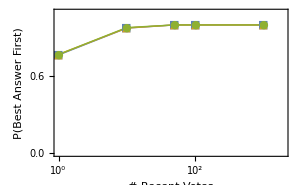

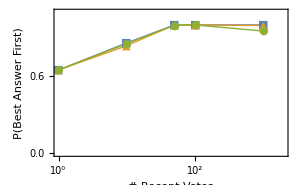

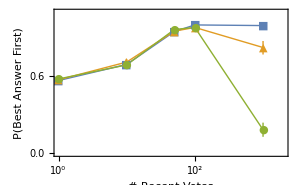

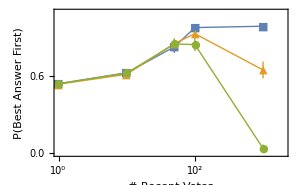

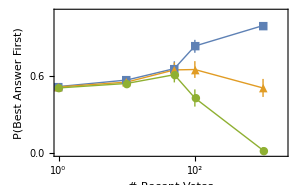

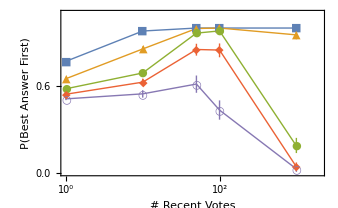

```mathematica
(*
PBestChosen=Table[
(*
bias: probability to choose answer 1 (worse answer)
*)
Print[{DQ2,NumVotes}];
If[DQ2==Round[DQ2],
strDQ2=ToString[DQ2]<>".0";
,
strDQ2=ToString[DQ2];
];
data=Table[

file="vote_sim_delta_qsquared="<>strDQ2<>"_num_recent_votes="<>ToString[NumVotes]<>"_bias="<>ToString[bias]<>"_trial="<>ToString[trial]<>".csv";
Import[file]
,{trial,0,99}];
(*which answer high quality*)
Qs=data[[;;,2;;3,5]];
BestAnswerQ=Table[Min[Abs[q]],{q,Qs}];
BestAnswer=Table[Position[Qs[[i]],BestAnswerQ[[i]]][[1,1]]-1,{i,Length[data]}];
(*is top answer on top*)
WhichAnswerOnTop=data[[;;,2;;,1]];
WhichAnswerOnTop=Table[DeleteCases[t,""],{t,WhichAnswerOnTop}];
BestAnswerOnTop=Table[Table[If[t==BestAnswer[[i]],1,0],{t,WhichAnswerOnTop[[i]]}],{i,Length[data]}];
ProbBestAnswerOnTop=Table[
p=Total[BestAnswerOnTop[[trial,-100;;]]]/100.0;
p
(*,{i,Round[Length[TopQOnTop[[trial]]]/100]}]*)
,{trial,Length[BestAnswerOnTop]}];
ProbBestAnswerOnTop
,{DQ2,{-2,-1,-0.5,-0.3,-0.1,0.1,0.3,0.5,1,2}}
,{NumVotes,{1,10,50,100,1000}}
,{bias,{0.1,0.5,0.9}(*{0.1,0.5,0.7}*)}];
*)
BootstrapMean[data_]:=Module[
{ResampledList,ResampledMeanDist},
(*Non-resampled bootstrap*)
n=10**4;
ResampledList=ArrayReshape[RandomChoice[data,Length[data] n],{Length[data],n}];
ResampledMeanDist=Total[ResampledList]/Length[data];(*Table[Mean[ResampledList[[i]]],{i,Length[ResampledList]}];*)
Return[N[{Mean[ResampledMeanDist],Quantile[ResampledMeanDist,{0.025,0.975}]}]];
];
Needs["CustomTicks`"]
Needs["ErrorBarPlots`"]
Do[
Print[ErrorListPlot[
Table[Table[
dat=Flatten[PBestChosen[[{q,Length[PBestChosen]-q+1},nv,bias,;;]]];
b=BootstrapMean[dat];
m=b[[1]];
err=b[[2]]-m;
{{Log10[{1,10,50,100,1000}[[nv]]],m},ErrorBar[err]}
,{nv,5}],{bias,3}],
Joined->True,
PlotStyle->Thick,
Frame->True,
PlotRange->{{0,3.3},{0,1.1}},
PlotMarkers->{"■","▲","●"},
FrameLabel->{
Style["# Recent Votes",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["P(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
ImageSize->300
]
];
,{q,5}]


Print[
ErrorListPlot[
Table[Table[
dat=Flatten[PBestChosen[[{q,Length[PBestChosen]-q+1},nv,3,;;]]];
b=BootstrapMean[dat];
m=b[[1]];
err=b[[2]]-m;
{{Log10[{1,10,50,100,1000}[[nv]]],m},ErrorBar[err]}
,{nv,5}],{q,5}],
Joined->True,
PlotStyle->Thick,
Frame->True,
PlotRange->{{0,3.3},{0,1.1}},
PlotMarkers->{"■","▲","●","◆","○"},
FrameLabel->{
Style["# Recent Votes",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["P(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
ImageSize->300
]
];

Print[
ListPlot[
Table[Table[
dat=Flatten[PBestChosen[[{q,Length[PBestChosen]-q+1},nv,3,;;]]];
m=Mean[dat];
{Log10[{1,10,50,100,1000}[[nv]]],m}
,{nv,5}],{q,5,1,-1}],
Joined->True,
PlotStyle->Thick,
Frame->True,
PlotRange->{{0,3.3},{0,1.1}},
PlotMarkers->{"■","▲","●","◆","○"},
FrameLabel->{
Style["# Recent Votes",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["P(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
ImageSize->300,
PlotLegends->LineLegend[ColorData[97,"ColorList"][[;;5]],Table[Style[ToString[dq],FontSize->12,FontFamily->"Arial"],{dq,{0.1,0.3,0.5,1,2}}],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],LabelStyle->Directive[Bold,FontFamily->"Arial",FontSize->12,Frame->True]
]
];
```

```mathematica
(*look at full popularity implies better answers visible at top
however, we can show that full popularity also implies that sometimes answers are stuck: better answers at bottom
Qt**2-Qb**2 = 0.5
*)
```

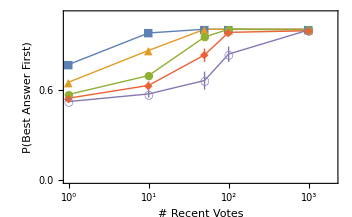

```mathematica
Print[
ErrorListPlot[
Table[Table[
dat=Flatten[PBestChosen[[{q,Length[PBestChosen]-q+1},nv,1,;;]]];
b=BootstrapMean[dat];
m=b[[1]];
err=b[[2]]-m;
{{Log10[{1,10,50,100,1000}[[nv]]],m},ErrorBar[err]}
,{nv,5}],{q,5}],
Joined->True,
PlotStyle->Thick,
Frame->True,
PlotRange->{{0,3.3},{0,1.1}},
PlotMarkers->{"■","▲","●","◆","○"},
FrameLabel->{
Style["# Recent Votes",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["P(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
ImageSize->300
]
];
```

~/Dropbox/ExpFiles/sim_data/

/Users/keithburghardt/Dropbox/ExpFiles/sim_data

20

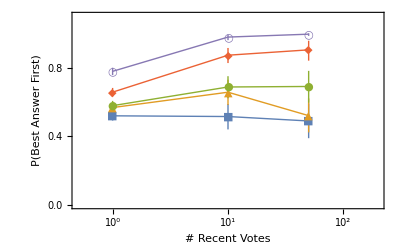

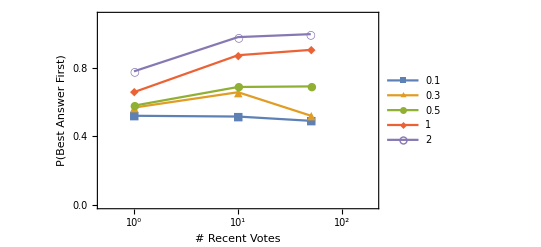

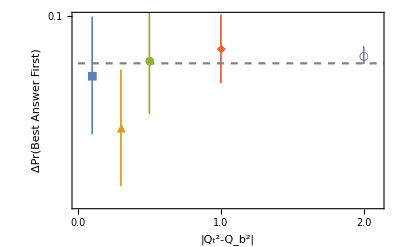

10

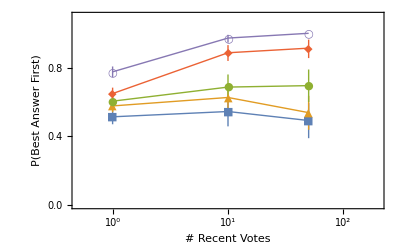

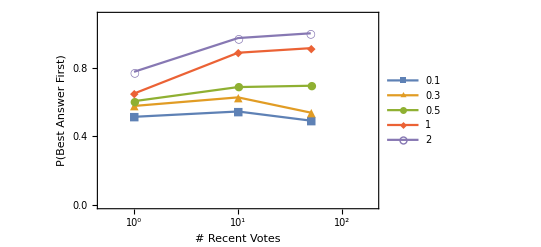

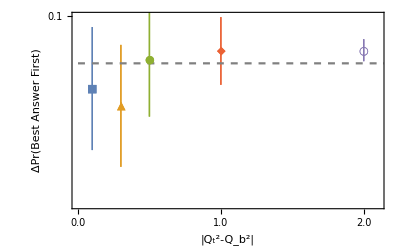

5

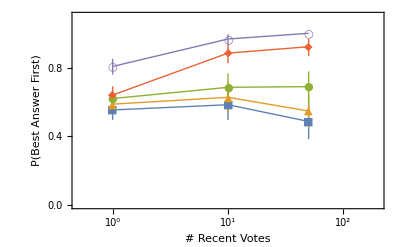

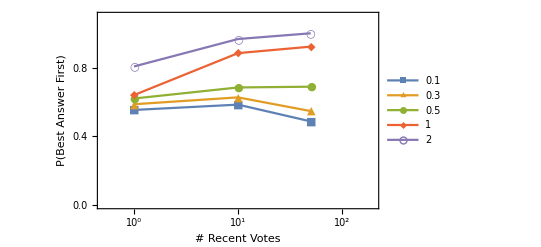

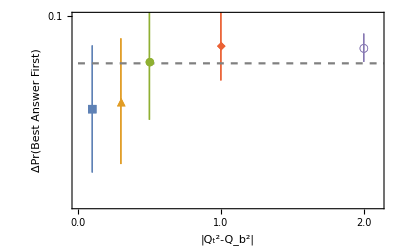

10

Part::partw: Part 2 of {{3/5,2/5,3/5,4/5,2/5,0,1,4/5,1,2/5,2/5,1,2/5,1/5,0,3/5,2/5,3/5,1,1/5,1/5,2/5,3/5,2/5,3/5,2/5,2/5,2/5,4/5,3/5,0,1,2/5,1/5,1,2/5,4/5,3/5,4/5,1,1,3/5,3/5,1/5,1,3/5,2/5,2/5,3/5,1/5,«40»}} does not exist.

4

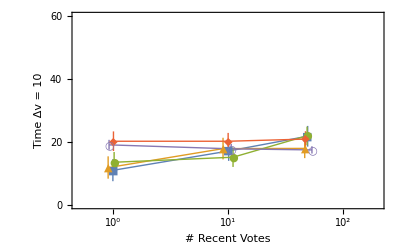

20

Part::partw: Part 2 of {{3/5,2/5,3/5,4/5,2/5,0,1,4/5,1,2/5,2/5,1,2/5,1/5,0,3/5,2/5,3/5,1,1/5,1/5,2/5,3/5,2/5,3/5,2/5,2/5,2/5,4/5,3/5,0,1,2/5,1/5,1,2/5,4/5,3/5,4/5,1,1,3/5,3/5,1/5,1,3/5,2/5,2/5,3/5,1/5,«40»}} does not exist.

4

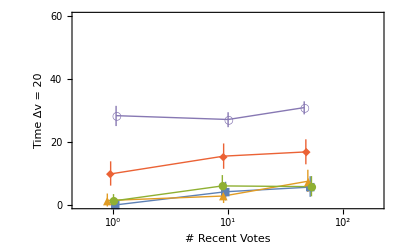

30

Part::partw: Part 2 of {{3/5,2/5,3/5,4/5,2/5,0,1,4/5,1,2/5,2/5,1,2/5,1/5,0,3/5,2/5,3/5,1,1/5,1/5,2/5,3/5,2/5,3/5,2/5,2/5,2/5,4/5,3/5,0,1,2/5,1/5,1,2/5,4/5,3/5,4/5,1,1,3/5,3/5,1/5,1,3/5,2/5,2/5,3/5,1/5,«40»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

4

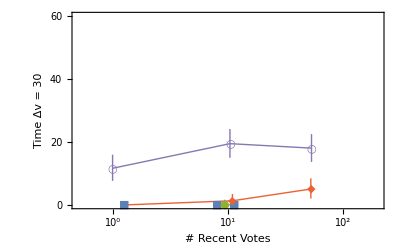

```mathematica
dir="~/Dropbox/ExpFiles/sim_data/"
SetDirectory[dir]
numtrials=90;
BootstrapMean[data_]:=Module[
{ResampledList,ResampledMeanDist},
(*Non-resampled bootstrap*)
n=10**4;
ResampledList=ArrayReshape[RandomChoice[data,Length[data] n],{Length[data],n}];
ResampledMeanDist=Total[ResampledList]/Length[data];(*Table[Mean[ResampledList[[i]]],{i,Length[ResampledList]}];*)
Return[N[{Mean[ResampledMeanDist],Quantile[ResampledMeanDist,{0.025,0.975}(*{0.159,0.841}*)]}]];
];
Needs["CustomTicks`"];
Needs["ErrorBarPlots`"];
(*dt=10;*)
Do[

PBestChosen=Table[
(*
bias: probability to choose answer 1 (worse answer)
*)
(*Print[{DQ2,NumVotes}];*)
(*If[DQ2==Round[DQ2],
strDQ2=ToString[DQ2]<>".0";
,*)

(*];*)
If[NumVotes==1&&bias==0.1,Print[DQ2];];
data=Table[

strDQ2=ToString[DQ2];
file="vote_sim_delta_qsquared="<>strDQ2<>"_num_recent_votes="<>ToString[NumVotes]<>"_bias="<>ToString[bias]<>"_threshold="<>"10"<>"_trial="<>ToString[trial]<>".csv";
Import[file]
,{trial,0,numtrials-1}];

(*which answer high quality*)
Qs=data[[;;,2;;3,5]];
BestAnswerQ=Table[Min[Abs[q]],{q,Qs}];
BestAnswer=Table[Position[Qs[[i]],BestAnswerQ[[i]]][[1,1]]-1,{i,Length[data]}];
(*is top answer on top*)
WhichAnswerOnTop=data[[;;,2;;,1]];
WhichAnswerOnTop=Table[DeleteCases[t,""],{t,WhichAnswerOnTop}];
BestAnswerOnTop=Table[Table[If[t==BestAnswer[[i]],1,0],{t,WhichAnswerOnTop[[i]]}],{i,Length[data]}];
ProbBestAnswerOnTop=Table[
p=Total[BestAnswerOnTop[[trial,-dt;;]]]/dt;
p
,{trial,Length[BestAnswerOnTop]}];
ProbBestAnswerOnTop

,{DQ2,{0.1,0.3,0.5,1,2}}
,{NumVotes,{1,10,50}}
,{bias,{0.5}(*{0.1,0.5,0.9}*)}];


Print[dt];

Print[
ErrorListPlot[
Table[Table[
dat=Flatten[PBestChosen[[q,nv,;;,;;numtrials]]];
b=BootstrapMean[dat];
m=b[[1]];
err=b[[2]]-m;
{{Log10[{1,10,50,100}[[nv]]],m},ErrorBar[err]}
,{nv,3}],{q,5}],
Joined->True,
Axes->False,
PlotStyle->Thick,
Frame->True,
PlotRange->{{-0.3,2.3},{0,1.1}},
PlotMarkers->{"■","▲","●","◆","○"},
FrameLabel->{
Style["# Recent Votes",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["P(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
ImageSize->400
]
];

Print[
ListPlot[
Table[Table[
dat=Flatten[PBestChosen[[q,nv,;;,;;numtrials]]];
m=Mean[dat];
{Log10[{1,10,50,100}[[nv]]],m}
,{nv,3}],{q,5}],
Joined->True,
Axes->False,
PlotStyle->Thick,
Frame->True,
PlotRange->{{-0.3,2.3},{0,1.1}},
PlotMarkers->{"■","▲","●","◆","○"},
FrameLabel->{
Style["# Recent Votes",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["P(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
ImageSize->400,
PlotLegends->LineLegend[ColorData[97,"ColorList"][[;;5]],Table[Style[ToString[dq],FontSize->12,FontFamily->"Arial"],{dq,{0.1,0.3,0.5,1,2}}],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],LabelStyle->Directive[FontFamily->"Arial",FontSize->12,Frame->True]
]
];
diff=Table[
dat50=Flatten[PBestChosen[[q,2,;;,;;numtrials]]];
dat100=Flatten[PBestChosen[[q,3,;;,;;numtrials]]];
b1=BootstrapMean[dat50];
b2=BootstrapMean[dat100];

m=b2[[1]]-b1[[1]];
(*err: 1/2 of 95% confidence range*)
err1=(b1[[2,1]]-b1[[2,2]])/2;
err2=(b2[[2,1]]-b2[[2,2]])/2;
err=Sqrt[err1**2+err2**2];
{{{{0.1,0.3,0.5,1,2}[[q]],m},ErrorBar[err]}}
,{q,5}];
Print[Show[
ErrorListPlot[diff,
Joined->True,
PlotRange->{{0,2.1},{-0.3,0.10001}},
Axes->False,
PlotStyle->Thick,
Frame->True,
PlotMarkers->{"■","▲","●","◆","○"},
FrameLabel->{
Style["|Q_t^2-Q_b^2|",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["ΔPr(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[-2,2,0.1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-2,2,0.1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[0,3,0.5,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,3,0.5,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
ImageSize->400
],
Plot[0,{x,0,3},PlotStyle->{Gray,Dashed}]
]];
,{dt,{20,10,5}}]

Do[
Print[threshold];
TimeToDiff=Table[
data=Table[
strDQ2=ToString[DQ2];
file="vote_sim_delta_qsquared="<>strDQ2<>"_num_recent_votes="<>ToString[NumVotes]<>"_bias="<>ToString[bias]<>"_threshold="<>threshold<>"_trial="<>ToString[trial]<>".csv";
Import[file]
,{trial,0,numtrials-1}];

(*which answer high quality*)
time=Flatten[data[[;;,2,6]]](*;
b=BootstrapMean[time];
m=b[[1]];
std=b[[2]]-m;
{m,std}*)
,{DQ2,{0.1,0.3,0.5,1,2}}
,{NumVotes,{1,10,50}}
,{bias,{0.5}}];


(*numtrials=300;*)
Print[Length[PBestChosen[[1,1,2]]]];
Print[
ErrorListPlot[
Table[Table[
dat=Flatten[TimeToDiff[[q,nv,(*{1,3}*);;,;;numtrials]]];
b=BootstrapMean[dat];
m=b[[1]];
err=b[[2]]-m;
{{Log10[{1,10,50,100}[[nv]]]+RandomReal[{-0.05,0.05}],m},ErrorBar[err]}
,{nv,3}],{q,5}],
Joined->True,
Axes->False,
PlotStyle->Thick,
Frame->True,
PlotRange->{{-0.3,2.3},{0,60}},
PlotMarkers->{"■","▲","●","◆","○"},
FrameLabel->{
Style["# Recent Votes",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Time Δv = "<>threshold,FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,100,20,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,100,20,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
ImageSize->400
]
];
,{threshold,{"10","20","30"}}]
```

0.1

0.3

0.5

1

2

20

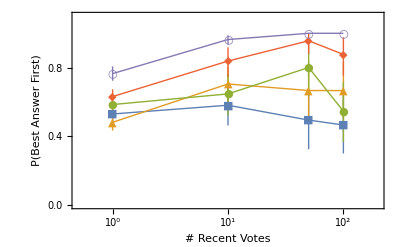

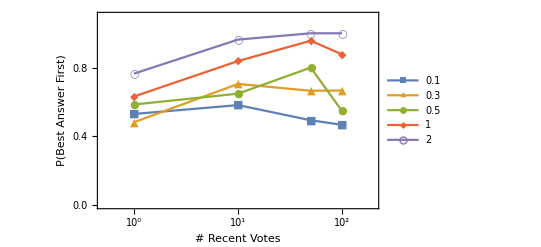

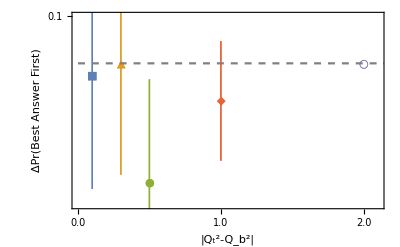

0.1

0.3

0.5

1

2

10

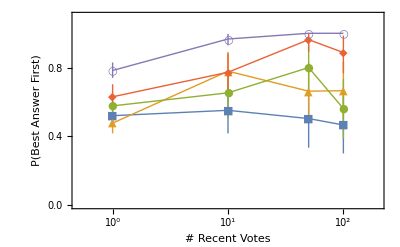

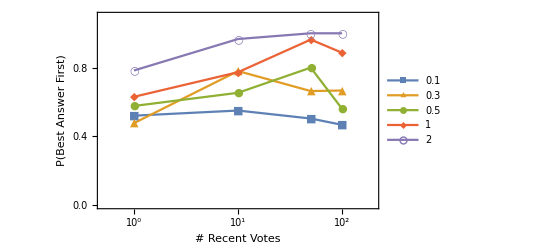

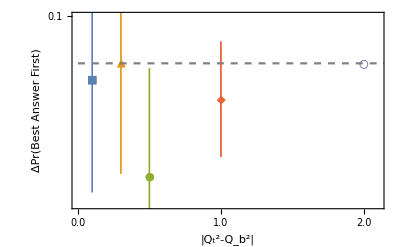

0.1

0.3

0.5

1

2

5

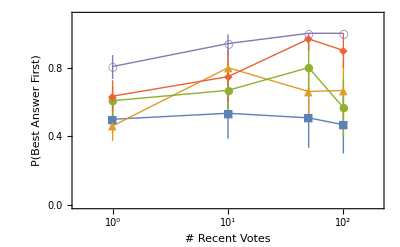

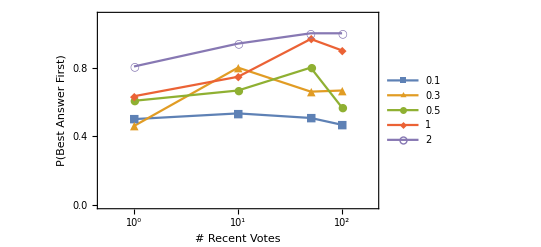

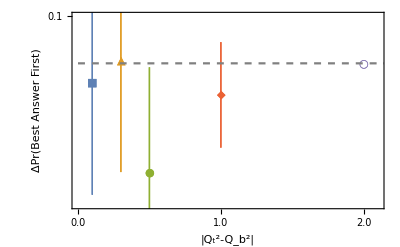

10

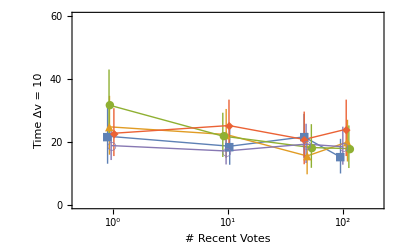

20

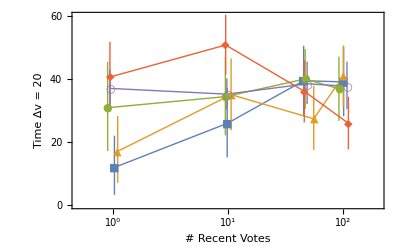

30

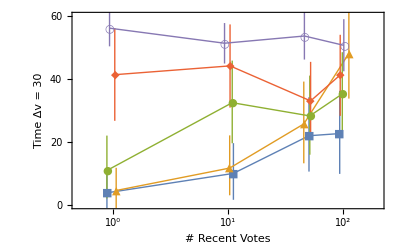

```mathematica
(*30 trials: 1 * 10 questions * 3 initial conditions = 3 conditions, (realistic)*)
```

/Users/keithburghardt/Dropbox/ExpFiles/sim_data

0.1

0.3

0.5

1

2

20

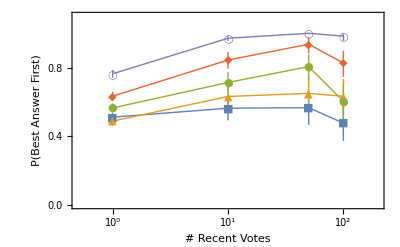

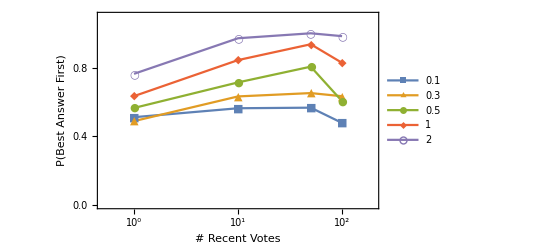

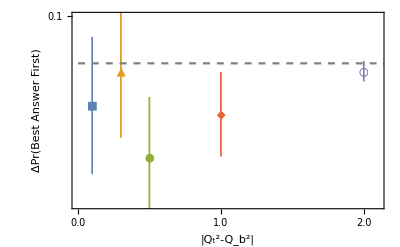

0.1

0.3

0.5

1

2

10

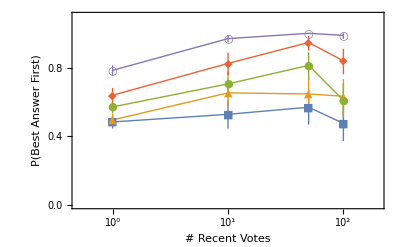

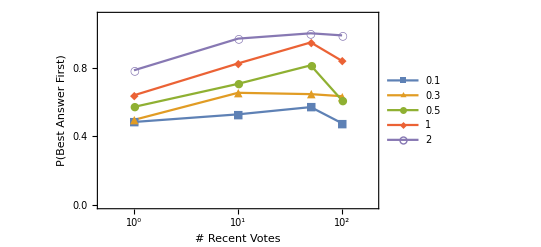

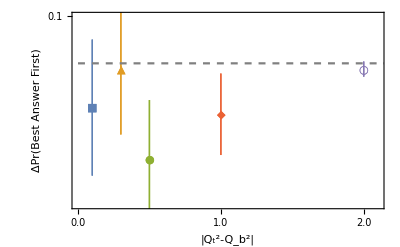

0.1

0.3

0.5

1

2

5

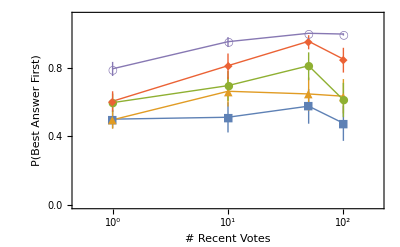

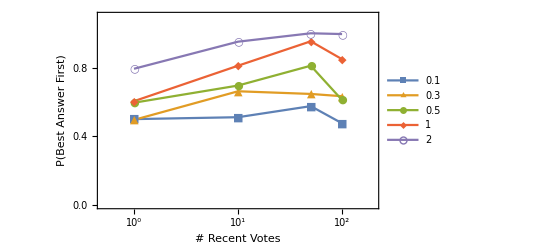

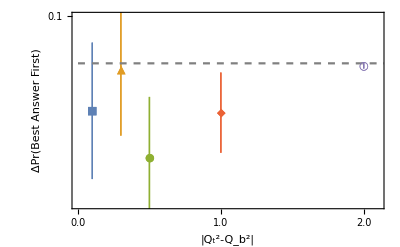

10

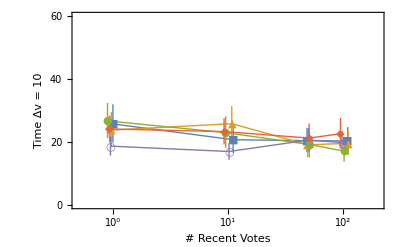

20

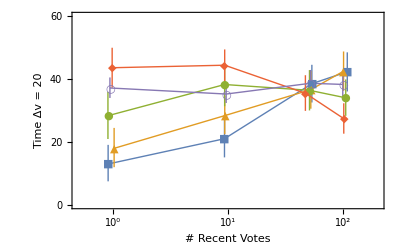

30

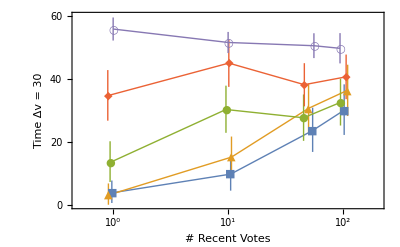

```mathematica
(*30 trials: 3 * 10 questions * 3 initial conditions = 9 conditions, *)
```

```mathematica
(*time vs delta vote *)
```

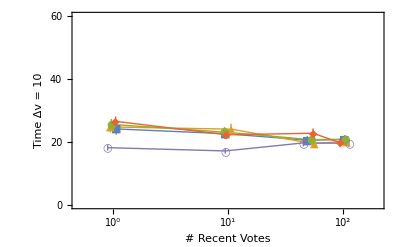

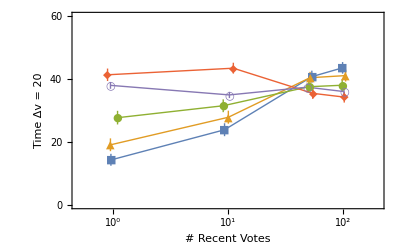

30

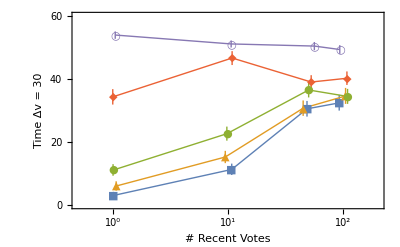

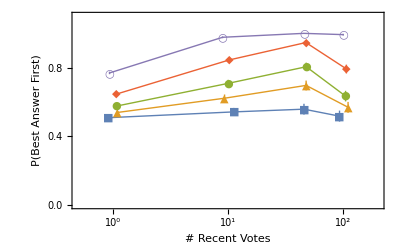

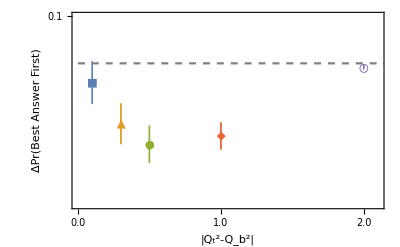

2

10(*last 10 votes*)

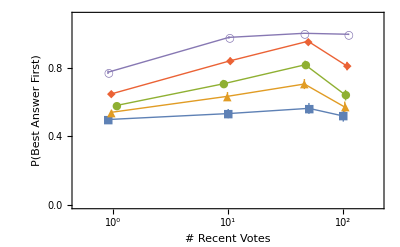

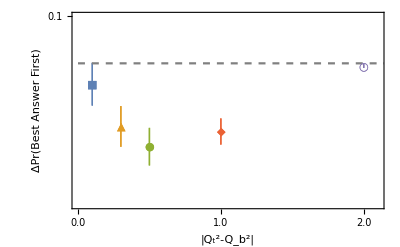

0.1

0.1

0.3

0.5

1

```mathematica
(*last 20 votes*)
```

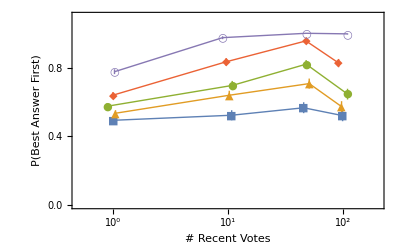

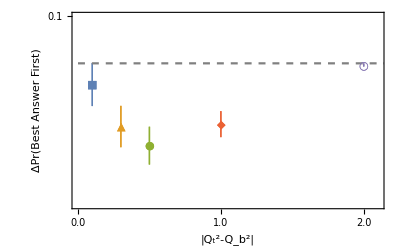

```mathematica
(*last 5 votes*)
```

```mathematica
(*time for difference to be 10 votes*)
```

10

{{0.1,0.56},{0.3,0.641},{0.5,0.705},{0.7,0.691},{0.9,0.568}}

{{0.1,1.2},{0.3,1.3},{0.5,1.4},{0.7,1.4},{0.9,1.4}}

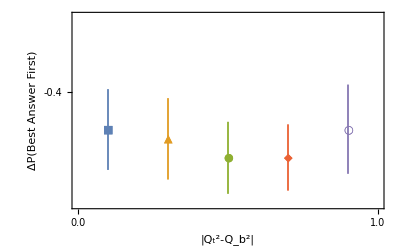

0.537

0.528

0.584

0.622

0.626

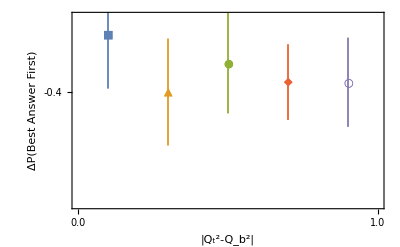

-Graphics-

```mathematica
BootstrapMean[data_]:=Module[
{ResampledList,ResampledMeanDist},
(*Non-resampled bootstrap*)
n=10**4;
ResampledList=ArrayReshape[RandomChoice[data,Length[data] n],{Length[data],n}];
ResampledMeanDist=Total[ResampledList]/Length[data];(*Table[Mean[ResampledList[[i]]],{i,Length[ResampledList]}];*)
Return[N[{Mean[ResampledMeanDist],Quantile[ResampledMeanDist,{0.025,0.975}(*{0.159,0.841}*)]}]];
];
Needs["CustomTicks`"];
Needs["ErrorBarPlots`"];
threshold=30;
bias=0.9;
numtrials=10*2;

plotdata=Table[
numrecentvotes=Floor[10**numrecentvotes];
file="~/Downloads/sim_data_last/vote_sim_"<>"delta_qsquared="<>deltaqsquared<>"_num_recent_votes="<>ToString[numrecentvotes]<>"_bias="<>ToString[bias]<>"_threshold="<>ToString[threshold]<>".csv";
data=Import[file];
topanswer=DeleteCases[data[[2;;,1]],""];

{Log10[numrecentvotes] ,1-Mean[topanswer]}

,{deltaqsquared ,{"0.1","0.30000000000000004","0.5000000000000001","0.7000000000000001","0.9000000000000001"}}
,{numrecentvotes,0,2.11,0.1}];

(*max differences*)
Table[{Table[dq,{dq,0.1,0.9,0.2}][[i]],Max[plotdata[[i,;;,2]]]-Min[plotdata[[i,;;,2]]]},{i,5}]
(*position of max*)
Table[
pos=Position[plotdata[[i,;;,2]],Max[plotdata[[i,;;,2]]]][[1,1]];
{Table[dq,{dq,0.1,0.9,0.2}][[i]],Table[nvotes,{nvotes,0,2.11,0.1}][[pos]]},{i,5}]
(*bootstrap differences*)

FindNumRecentVotes[meandata_,value_]:=Module[{pos,numrecentvotes},
pos=Position[meandata,value][[1,1]];
numrecentvotes=Table[nvotes,{nvotes,0,2.11,0.1}][[pos]];
numrecentvotes=Floor[10**numrecentvotes];
Return[numrecentvotes];
];

FindPBest[plotdata_,deltaqsquaredpos_,value_,numtrials_]:=Module[{numrecentvotes,deltaqsquared,file,data,topanswer,meandata},
meandata=plotdata[[deltaqsquaredpos,;;,2]];
numrecentvotes=FindNumRecentVotes[meandata,value];
deltaqsquared={"0.1","0.30000000000000004","0.5000000000000001","0.7000000000000001","0.9000000000000001"}[[deltaqsquaredpos]];
file="~/Downloads/sim_data_last/vote_sim_"<>"delta_qsquared="<>deltaqsquared<>"_num_recent_votes="<>ToString[numrecentvotes]<>"_bias="<>ToString[bias]<>"_threshold="<>ToString[threshold]<>".csv";
data=Import[file];
topanswer=DeleteCases[data[[2;;,1]],""][[;;numtrials]];
Return[topanswer];
];
FindDiff[data1_,data2_]:=Module[{b1,b2,diff,rng1,rng2,err},
b1=BootstrapMean[data1];
b2=BootstrapMean[data2];
(*mean difference*)
diff=b2[[1]]-b1[[1]];
(*1/2 95% confidence interval*)
rng1=(b1[[2,2]]-b1[[2,1]])/2;
rng2=(b2[[2,2]]-b2[[2,1]])/2;
(*total error*)
err=Sqrt[rng1**2+rng2**2];
Return[{diff,err}]
];
meanchange=Table[
max=Max[plotdata[[i,;;,2]]];
Maxtopanswer=FindPBest[plotdata,i,max,numtrials];
min=Min[plotdata[[i,;;,2]]];
Mintopanswer=FindPBest[plotdata,i,min,numtrials];
b=FindDiff[Mintopanswer,Maxtopanswer];
{{{Table[dq,{dq,0.1,0.9,0.2}][[i]],b[[1]]},ErrorBar[b[[2]]]}}
,{i,5}];
ErrorListPlot[meanchange,
PlotRange->{{0,1},{-1,0}},
PlotMarkers->{"■","▲","●","◆","○"},
Joined->True,
Axes->False,
PlotStyle->Thick,
Frame->True,
FrameLabel->{
Style["|Q_t^2-Q_b^2|",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["ΔP(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[-2,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-2,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[-2,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-2,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
ImageSize->400
]

meanchange=Table[
max=Max[plotdata[[i,;;,2]]];
Maxtopanswer=FindPBest[plotdata,i,max,numtrials];
first=plotdata[[i,1,2]];
Print[first];
firsttopanswer=FindPBest[plotdata,i,first,numtrials];
b=FindDiff[firsttopanswer,Maxtopanswer];
{{{Table[dq,{dq,0.1,0.9,0.2}][[i]],b[[1]]},ErrorBar[b[[2]]]}}
,{i,5}];

ErrorListPlot[meanchange,
PlotRange->{{0,1},{-1,0}},
PlotMarkers->{"■","▲","●","◆","○"},
Joined->True,
Axes->False,
PlotStyle->Thick,
Frame->True,
FrameLabel->{
Style["|Q_t^2-Q_b^2|",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["ΔP(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[-2,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-2,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[-2,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-2,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
ImageSize->400
]


(*p top vs past votes*)
ListLinePlot[plotdata,
Joined->True,
Axes->False,
PlotStyle->Thick,
Frame->True,
PlotRange->{{0,2.3},{0,1}},
PlotMarkers->{"■","▲","●","◆","○"},
FrameLabel->{
Style["# Recent Votes",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["P(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LogTicks[0,3,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[0,3,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
ImageSize->400,
PlotLegends->LineLegend[ColorData[97,"ColorList"][[;;5]],Table[Style[ToString[dq],FontSize->12,FontFamily->"Arial"],{dq,0.1,0.9,0.2}],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],LabelStyle->Directive[FontFamily->"Arial",FontSize->12,Frame->True]
]
```

```mathematica
Range[Table[i,{i,10}]]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10}}

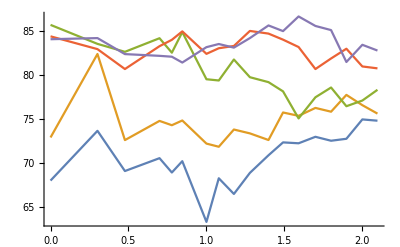

-Graphics-

```mathematica
plotdata=Table[DeleteCases[Table[
numrecentvotes=Floor[10**numrecentvotes];
file="~/Downloads/sim_data_last/vote_sim_"<>"delta_qsquared="<>deltaqsquared<>"_num_recent_votes="<>ToString[numrecentvotes]<>"_bias="<>ToString[bias]<>"_threshold="<>ToString[threshold]<>".csv";
data=Import[file];
timetowinner=DeleteCases[DeleteCases[data[[2;;,-1]],""],-1.];
If[Length[timetowinner]>0,
{Log10[numrecentvotes] ,Mean[timetowinner]}
]
,{numrecentvotes,0,2.11,0.1}],Null]
,{deltaqsquared ,{"0.1","0.30000000000000004","0.5000000000000001","0.7000000000000001","0.9000000000000001"}}];
ListLinePlot[plotdata]
numtrials=10*3;
plotdata=Table[DeleteCases[Table[
numrecentvotes=Floor[10**numrecentvotes];
file="~/Downloads/sim_data_last/vote_sim_"<>"delta_qsquared="<>deltaqsquared<>"_num_recent_votes="<>ToString[numrecentvotes]<>"_bias="<>ToString[bias]<>"_threshold="<>ToString[threshold]<>".csv";
data=Import[file];
timetowinner=DeleteCases[DeleteCases[data[[2;;,-1]],""][[;;numtrials]]/.-1.->110,-1.];
If[Length[timetowinner]>0,
{Log10[numrecentvotes] ,Mean[timetowinner]}
]
,{numrecentvotes,0,2.11,0.1}],Null]
,{deltaqsquared ,{"0.1","0.30000000000000004","0.5000000000000001","0.7000000000000001","0.9000000000000001"}}];
ListLinePlot[plotdata,
Joined->True,
Axes->False,
PlotStyle->Thick,
Frame->True,
PlotRange->{{-0.3,2.3},{0,120}},
PlotMarkers->{"■","▲","●","◆","○"},
FrameLabel->{
Style["# Recent Votes",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Time Δv = 30",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,100,20,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,100,20,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
},
ImageSize->400
]
```

```mathematica
D[Exp[x],x]
```

ⅇ^x

```mathematica
Clear[n,p]
(*p(if top)*)
pt=1/(1+ⅇ^dQ /theta);
(*p(if bottom)*)
pb=1/(1+ⅇ^dQ theta);
(*log likelihood: log(choose if top) + log(not choose if top)
 + log(choose if bottom) + log(not choose if bottom)*)
logℒ=nt Log[pt]+(totT-nt) Log[1-pt]+nb Log[pb]+(totB-nb) Log[1-pb];
(*d(logℒ)/d(dQ)*)
FullSimplify[D[logℒ,dQ]]
(*optimal dQ when logℒ is max*)
FullSimplify[Solve[FullSimplify[D[logℒ,dQ]]==0,dQ]]
(*dQopt=Log[(-n theta+theta tot)/n];*)
(*fisher information*)
FullSimplify[D[FullSimplify[D[logℒ,dQ]],dQ]]
dQopt=Log[1/(2 (nb+nt) theta)(-nb (1+theta^2)-nt (1+theta^2)+totB+theta^2 totT+√(((nb+nt) (-1+theta^2)+totB)^2+2 theta^2 (nb+nt-(nb+nt) theta^2+totB) totT+theta^4 totT^2))];
(*Fisher=FullSimplify[ⅇ^dQopt theta (-totB/((1+ⅇ^dQopt theta)^2)-totT/((ⅇ^dQopt+theta)^2))];
Fisher*)
```

-nb-nt+totB/(1+ⅇ^dQ theta)+(theta totT)/(ⅇ^dQ+theta)

{{dQ→ConditionalExpression[2 ⅈ π C[1]+Log[1/(2 (nb+nt) theta)(-nb (1+theta^2)-nt (1+theta^2)+totB+theta^2 totT+√(((nb+nt) (-1+theta^2)+totB)^2+2 theta^2 (nb+nt-(nb+nt) theta^2+totB) totT+theta^4 totT^2))],C[1]∈ℤ]},{dQ→ConditionalExpression[2 ⅈ π C[1]+Log[-1/(2 (nb+nt) theta)(nt+nb (1+theta^2)-totB+theta^2 (nt-totT)+√(((nb+nt) (-1+theta^2)+totB)^2+2 theta^2 (nb+nt-(nb+nt) theta^2+totB) totT+theta^4 totT^2))],C[1]∈ℤ]}}

ⅇ^dQ theta (-totB/((1+ⅇ^dQ theta)^2)-totT/((ⅇ^dQ+theta)^2))

2 (nb+nt) (-nb (1+theta^2)-nt (1+theta^2)+totB+theta^2 totT+√(((nb+nt) (-1+theta^2)+totB)^2+2 theta^2 (nb+nt-(nb+nt) theta^2+totB) totT+theta^4 totT^2)) (-(totB/(nb+nt-nb theta^2+totB+theta^2 (-nt+totT)+√(((nb+nt) (-1+theta^2)+totB)^2+2 theta^2 (nb+nt-(nb+nt) theta^2+totB) totT+theta^4 totT^2))^2)-(theta^2 totT)/(-nt+nb (-1+theta^2)+totB+theta^2 (nt+totT)+√(((nb+nt) (-1+theta^2)+totB)^2+2 theta^2 (nb+nt-(nb+nt) theta^2+totB) totT+theta^4 totT^2))^2)

```mathematica
FullSimplify[Log[1/(2 (nb+nt) theta)(-nb (1+theta^2)-nt (1+theta^2)+totB+theta^2 totT+√(((nb+nt) (-1+theta^2)+totB)^2+2 theta^2 (nb+nt-(nb+nt) theta^2+totB) totT+theta^4 totT^2))]]
```

Log[1/(2 (nb+nt) theta)(-nb (1+theta^2)-nt (1+theta^2)+totB+theta^2 totT+√(((nb+nt) (-1+theta^2)+totB)^2+2 theta^2 (nb+nt-(nb+nt) theta^2+totB) totT+theta^4 totT^2))]

```mathematica
pt=1/(1+ⅇ^dQ /theta);
FullSimplify[1-pt]
```

ⅇ^dQ/(ⅇ^dQ+theta)

```mathematica
logℒ=-nt Log[1+1/θ Exp[dQ/2]]+(Nt-nt)Log[1/θ Exp[dQ/2]]-(Nt-nt)Log[1+1/θ Exp[dQ/2]]+nb Log[1/θ Exp[-dQ/2]]-nb Log[1+1/θ Exp[-dQ/2]]-(Nb-nb )Log[1+1/θ Exp[-dQ/2]];

{s1,s2}=Solve[FullSimplify[D[logℒ,dQ]]==0,dQ];
FullSimplify[s1]
FullSimplify[s1]
```

1.55

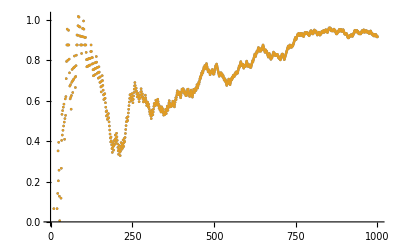

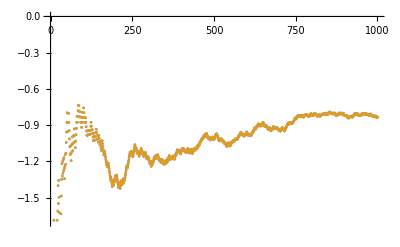

```mathematica
θ=1.55
S1[nt_,Nt_,nb_,Nb_]:=2 (Log[(Nb-nt-nt θ^2+Nt θ^2-nb (1+θ^2)+√(-4 (nb+nt) (nb-Nb+nt-Nt) θ^2+(nb-Nb+nt+(nb+nt-Nt) θ^2)^2))/(2 (nb+nt) θ)]);
S2[nt_,Nt_,nb_,Nb_]:=2 (Log[(Nb-nt-nt θ^2+Nt θ^2-nb (1+θ^2)+√(-4 (nb+nt) (nb-Nb+nt-Nt) θ^2+(nb-Nb+nt+(nb+nt-Nt) θ^2)^2))/(2 (nb+nt) θ)]);

votest=RandomInteger[{0,1},1000];
votesb=RandomInteger[{0,1},500];

ListPlot[(*Table[S1[Total[votes[[;;n]]],n,0,0],{n,Length[votes]}],*){Table[S1[Total[votest[[;;n]]],n,0,0],{n,Length[votest]}],Table[S2[Total[votest[[;;n]]],n,0,0],{n,Length[votest]}]}]
ListPlot[(*Table[S1[Total[votes[[;;n]]],n,0,0],{n,Length[votes]}],*){Table[S1[0,0,Total[votest[[;;n]]],n],{n,Length[votest]}],Table[S2[0,0,Total[votest[[;;n]]],n],{n,Length[votest]}]}]
```

```mathematica
2*(log((Nb-nt-nt*theta*theta+Nt*theta*theta-nb*(1+theta*theta)+sqrt(-4*(nb+nt)*(nb-Nb+nt-Nt)*theta*theta+(nb-Nb+nt+(nb+nt-Nt)*theta*theta)**2))/(2*(nb+nt)*theta)))
```

```mathematica
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
BootstrapMean[data_]:=Module[
{ResampledList,ResampledMeanDist},
(*Non-resampled bootstrap*)
n=10^4;
ResampledList=ArrayReshape[RandomChoice[data,Length[data] n],{Length[data],n}];
ResampledMeanDist=Total[ResampledList]/Length[data];(*Table[Mean[ResampledList[[i]]],{i,Length[ResampledList]}];*)
Return[N[{Mean[ResampledMeanDist],Quantile[ResampledMeanDist,{0.025,0.975}(*{0.159,0.841}*)]}]];
];
Needs["CustomTicks`"];
Needs["ErrorBarPlots`"];

dir="~/Dropbox/ExpFiles/new_sim_data/";
Clear[deltaQ,bias,threshold];
PopRankStatistics=Table[
file="popularity_rank_vote_sim_delta_qsquared="<>deltaQ<>"_num_recent_votes=all_bias="<>bias<>"_threshold="<>threshold<>".csv";

data=Import[dir<>file];
If[FileExistsQ[dir<>file],
Print[file];
MeanTopAnswer=BootstrapMean[data[[2;;;;2,1]]];
MeanTimeToThreshold=BootstrapMean[DeleteCases[data[[2;;;;2,-1]],-1]];
{MeanTopAnswer,MeanTimeToThreshold}
,
{Null,Null}
]
,{deltaQ,{"0.1","0.30000000000000004","0.5000000000000001","0.7000000000000001","0.9000000000000001"}}
,{bias,{"0.1","0.5","0.9"}}
,{threshold,{"15","20","30"}}];

QualityRankStatistics=Table[
file="quality_rank_vote_sim_delta_qsquared="<>deltaQ<>"_num_recent_votes=all_bias="<>bias<>"_threshold="<>threshold<>".csv";

If[FileExistsQ[dir<>file],
Print[file];
data=Import[dir<>file];
MeanTopAnswer=BootstrapMean[data[[2;;;;2,1]]];
MeanTimeToThreshold=BootstrapMean[DeleteCases[data[[2;;;;2,-1]],-1]];
{MeanTopAnswer,MeanTimeToThreshold}
,
{Null,Null}
]
,{deltaQ,{"0.1","0.30000000000000004","0.5000000000000001","0.7000000000000001","0.9000000000000001"}}
,{bias,{"0.1","0.5","0.9"}}
,{threshold,{"15","20","30"}}];
```

popularity_rank_vote_sim_delta_qsquared=0.1_num_recent_votes=all_bias=0.1_threshold=15.csv

popularity_rank_vote_sim_delta_qsquared=0.1_num_recent_votes=all_bias=0.1_threshold=20.csv

popularity_rank_vote_sim_delta_qsquared=0.1_num_recent_votes=all_bias=0.1_threshold=30.csv

popularity_rank_vote_sim_delta_qsquared=0.1_num_recent_votes=all_bias=0.5_threshold=15.csv

popularity_rank_vote_sim_delta_qsquared=0.1_num_recent_votes=all_bias=0.5_threshold=20.csv

popularity_rank_vote_sim_delta_qsquared=0.1_num_recent_votes=all_bias=0.5_threshold=30.csv

popularity_rank_vote_sim_delta_qsquared=0.1_num_recent_votes=all_bias=0.9_threshold=15.csv

popularity_rank_vote_sim_delta_qsquared=0.1_num_recent_votes=all_bias=0.9_threshold=20.csv

popularity_rank_vote_sim_delta_qsquared=0.1_num_recent_votes=all_bias=0.9_threshold=30.csv

popularity_rank_vote_sim_delta_qsquared=0.30000000000000004_num_recent_votes=all_bias=0.1_threshold=15.csv

popularity_rank_vote_sim_delta_qsquared=0.30000000000000004_num_recent_votes=all_bias=0.1_threshold=20.csv

popularity_rank_vote_sim_delta_qsquared=0.30000000000000004_num_recent_votes=all_bias=0.1_threshold=30.csv

popularity_rank_vote_sim_delta_qsquared=0.30000000000000004_num_recent_votes=all_bias=0.5_threshold=15.csv

popularity_rank_vote_sim_delta_qsquared=0.30000000000000004_num_recent_votes=all_bias=0.5_threshold=20.csv

popularity_rank_vote_sim_delta_qsquared=0.30000000000000004_num_recent_votes=all_bias=0.5_threshold=30.csv

popularity_rank_vote_sim_delta_qsquared=0.30000000000000004_num_recent_votes=all_bias=0.9_threshold=15.csv

popularity_rank_vote_sim_delta_qsquared=0.30000000000000004_num_recent_votes=all_bias=0.9_threshold=20.csv

popularity_rank_vote_sim_delta_qsquared=0.30000000000000004_num_recent_votes=all_bias=0.9_threshold=30.csv

popularity_rank_vote_sim_delta_qsquared=0.5000000000000001_num_recent_votes=all_bias=0.1_threshold=15.csv

popularity_rank_vote_sim_delta_qsquared=0.5000000000000001_num_recent_votes=all_bias=0.1_threshold=20.csv

popularity_rank_vote_sim_delta_qsquared=0.5000000000000001_num_recent_votes=all_bias=0.1_threshold=30.csv

popularity_rank_vote_sim_delta_qsquared=0.5000000000000001_num_recent_votes=all_bias=0.5_threshold=15.csv

popularity_rank_vote_sim_delta_qsquared=0.5000000000000001_num_recent_votes=all_bias=0.5_threshold=20.csv

popularity_rank_vote_sim_delta_qsquared=0.5000000000000001_num_recent_votes=all_bias=0.5_threshold=30.csv

popularity_rank_vote_sim_delta_qsquared=0.5000000000000001_num_recent_votes=all_bias=0.9_threshold=15.csv

popularity_rank_vote_sim_delta_qsquared=0.5000000000000001_num_recent_votes=all_bias=0.9_threshold=20.csv

popularity_rank_vote_sim_delta_qsquared=0.5000000000000001_num_recent_votes=all_bias=0.9_threshold=30.csv

popularity_rank_vote_sim_delta_qsquared=0.7000000000000001_num_recent_votes=all_bias=0.1_threshold=15.csv

popularity_rank_vote_sim_delta_qsquared=0.7000000000000001_num_recent_votes=all_bias=0.1_threshold=20.csv

popularity_rank_vote_sim_delta_qsquared=0.7000000000000001_num_recent_votes=all_bias=0.1_threshold=30.csv

popularity_rank_vote_sim_delta_qsquared=0.7000000000000001_num_recent_votes=all_bias=0.5_threshold=15.csv

popularity_rank_vote_sim_delta_qsquared=0.7000000000000001_num_recent_votes=all_bias=0.5_threshold=20.csv

popularity_rank_vote_sim_delta_qsquared=0.7000000000000001_num_recent_votes=all_bias=0.5_threshold=30.csv

popularity_rank_vote_sim_delta_qsquared=0.7000000000000001_num_recent_votes=all_bias=0.9_threshold=15.csv

popularity_rank_vote_sim_delta_qsquared=0.7000000000000001_num_recent_votes=all_bias=0.9_threshold=20.csv

popularity_rank_vote_sim_delta_qsquared=0.7000000000000001_num_recent_votes=all_bias=0.9_threshold=30.csv

popularity_rank_vote_sim_delta_qsquared=0.9000000000000001_num_recent_votes=all_bias=0.1_threshold=15.csv

popularity_rank_vote_sim_delta_qsquared=0.9000000000000001_num_recent_votes=all_bias=0.1_threshold=20.csv

popularity_rank_vote_sim_delta_qsquared=0.9000000000000001_num_recent_votes=all_bias=0.1_threshold=30.csv

popularity_rank_vote_sim_delta_qsquared=0.9000000000000001_num_recent_votes=all_bias=0.5_threshold=15.csv

popularity_rank_vote_sim_delta_qsquared=0.9000000000000001_num_recent_votes=all_bias=0.5_threshold=20.csv

popularity_rank_vote_sim_delta_qsquared=0.9000000000000001_num_recent_votes=all_bias=0.5_threshold=30.csv

popularity_rank_vote_sim_delta_qsquared=0.9000000000000001_num_recent_votes=all_bias=0.9_threshold=15.csv

popularity_rank_vote_sim_delta_qsquared=0.9000000000000001_num_recent_votes=all_bias=0.9_threshold=20.csv

popularity_rank_vote_sim_delta_qsquared=0.9000000000000001_num_recent_votes=all_bias=0.9_threshold=30.csv

quality_rank_vote_sim_delta_qsquared=0.1_num_recent_votes=all_bias=0.1_threshold=15.csv

quality_rank_vote_sim_delta_qsquared=0.1_num_recent_votes=all_bias=0.1_threshold=20.csv

quality_rank_vote_sim_delta_qsquared=0.1_num_recent_votes=all_bias=0.1_threshold=30.csv

quality_rank_vote_sim_delta_qsquared=0.1_num_recent_votes=all_bias=0.5_threshold=15.csv

quality_rank_vote_sim_delta_qsquared=0.1_num_recent_votes=all_bias=0.5_threshold=20.csv

quality_rank_vote_sim_delta_qsquared=0.1_num_recent_votes=all_bias=0.5_threshold=30.csv

quality_rank_vote_sim_delta_qsquared=0.1_num_recent_votes=all_bias=0.9_threshold=15.csv

quality_rank_vote_sim_delta_qsquared=0.1_num_recent_votes=all_bias=0.9_threshold=20.csv

quality_rank_vote_sim_delta_qsquared=0.1_num_recent_votes=all_bias=0.9_threshold=30.csv

quality_rank_vote_sim_delta_qsquared=0.30000000000000004_num_recent_votes=all_bias=0.1_threshold=15.csv

quality_rank_vote_sim_delta_qsquared=0.30000000000000004_num_recent_votes=all_bias=0.1_threshold=20.csv

quality_rank_vote_sim_delta_qsquared=0.30000000000000004_num_recent_votes=all_bias=0.1_threshold=30.csv

quality_rank_vote_sim_delta_qsquared=0.30000000000000004_num_recent_votes=all_bias=0.5_threshold=15.csv

quality_rank_vote_sim_delta_qsquared=0.30000000000000004_num_recent_votes=all_bias=0.5_threshold=20.csv

quality_rank_vote_sim_delta_qsquared=0.30000000000000004_num_recent_votes=all_bias=0.5_threshold=30.csv

quality_rank_vote_sim_delta_qsquared=0.30000000000000004_num_recent_votes=all_bias=0.9_threshold=15.csv

quality_rank_vote_sim_delta_qsquared=0.30000000000000004_num_recent_votes=all_bias=0.9_threshold=20.csv

quality_rank_vote_sim_delta_qsquared=0.30000000000000004_num_recent_votes=all_bias=0.9_threshold=30.csv

quality_rank_vote_sim_delta_qsquared=0.5000000000000001_num_recent_votes=all_bias=0.1_threshold=15.csv

quality_rank_vote_sim_delta_qsquared=0.5000000000000001_num_recent_votes=all_bias=0.1_threshold=20.csv

quality_rank_vote_sim_delta_qsquared=0.5000000000000001_num_recent_votes=all_bias=0.1_threshold=30.csv

quality_rank_vote_sim_delta_qsquared=0.5000000000000001_num_recent_votes=all_bias=0.5_threshold=15.csv

quality_rank_vote_sim_delta_qsquared=0.5000000000000001_num_recent_votes=all_bias=0.5_threshold=20.csv

quality_rank_vote_sim_delta_qsquared=0.5000000000000001_num_recent_votes=all_bias=0.5_threshold=30.csv

quality_rank_vote_sim_delta_qsquared=0.5000000000000001_num_recent_votes=all_bias=0.9_threshold=15.csv

quality_rank_vote_sim_delta_qsquared=0.5000000000000001_num_recent_votes=all_bias=0.9_threshold=20.csv

quality_rank_vote_sim_delta_qsquared=0.5000000000000001_num_recent_votes=all_bias=0.9_threshold=30.csv

quality_rank_vote_sim_delta_qsquared=0.7000000000000001_num_recent_votes=all_bias=0.1_threshold=15.csv

quality_rank_vote_sim_delta_qsquared=0.7000000000000001_num_recent_votes=all_bias=0.1_threshold=20.csv

quality_rank_vote_sim_delta_qsquared=0.7000000000000001_num_recent_votes=all_bias=0.1_threshold=30.csv

quality_rank_vote_sim_delta_qsquared=0.7000000000000001_num_recent_votes=all_bias=0.5_threshold=15.csv

quality_rank_vote_sim_delta_qsquared=0.7000000000000001_num_recent_votes=all_bias=0.5_threshold=20.csv

quality_rank_vote_sim_delta_qsquared=0.7000000000000001_num_recent_votes=all_bias=0.5_threshold=30.csv

quality_rank_vote_sim_delta_qsquared=0.7000000000000001_num_recent_votes=all_bias=0.9_threshold=15.csv

quality_rank_vote_sim_delta_qsquared=0.7000000000000001_num_recent_votes=all_bias=0.9_threshold=20.csv

quality_rank_vote_sim_delta_qsquared=0.7000000000000001_num_recent_votes=all_bias=0.9_threshold=30.csv

quality_rank_vote_sim_delta_qsquared=0.9000000000000001_num_recent_votes=all_bias=0.1_threshold=15.csv

quality_rank_vote_sim_delta_qsquared=0.9000000000000001_num_recent_votes=all_bias=0.1_threshold=20.csv

quality_rank_vote_sim_delta_qsquared=0.9000000000000001_num_recent_votes=all_bias=0.1_threshold=30.csv

quality_rank_vote_sim_delta_qsquared=0.9000000000000001_num_recent_votes=all_bias=0.5_threshold=15.csv

quality_rank_vote_sim_delta_qsquared=0.9000000000000001_num_recent_votes=all_bias=0.5_threshold=20.csv

quality_rank_vote_sim_delta_qsquared=0.9000000000000001_num_recent_votes=all_bias=0.5_threshold=30.csv

quality_rank_vote_sim_delta_qsquared=0.9000000000000001_num_recent_votes=all_bias=0.9_threshold=15.csv

quality_rank_vote_sim_delta_qsquared=0.9000000000000001_num_recent_votes=all_bias=0.9_threshold=20.csv

quality_rank_vote_sim_delta_qsquared=0.9000000000000001_num_recent_votes=all_bias=0.9_threshold=30.csv

```mathematica
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
BootstrapMean[data_]:=Module[
{ResampledList,ResampledMeanDist},
(*Non-resampled bootstrap*)
n=10^4;
ResampledList=ArrayReshape[RandomChoice[data,Length[data] n],{Length[data],n}];
ResampledMeanDist=Total[ResampledList]/Length[data];(*Table[Mean[ResampledList[[i]]],{i,Length[ResampledList]}];*)
Return[N[{Mean[ResampledMeanDist],Quantile[ResampledMeanDist,{0.025,0.975}(*{0.159,0.841}*)]}]];
];
Needs["CustomTicks`"];
Needs["ErrorBarPlots`"];
NumTrials=100;
RunTime=10000;

dir="~/Dropbox/ExpFiles/new_sim_data/";
Clear[deltaQ,bias,threshold];
PopRankStatistics=Table[


file="popularity_rank_vote_sim_s="<>ToString[s]<>"_num_recent_votes=all_bias="<>bias<>"_threshold="<>threshold<>"_t="<>ToString[RunTime]<>".csv";
If[FileExistsQ[dir<>file],
data=Import[dir<>file];
MeanTopAnswer=BootstrapMean[data[[2;;NumTrials+1,1]]];
MeanTimeToThreshold=BootstrapMean[DeleteCases[data[[2;;NumTrials+1,-1]],-1]];

{MeanTopAnswer,MeanTimeToThreshold}
,
{Null,Null}
]
,{s,0.5,0.741,0.02}
,{bias,{"0.1","0.5","0.9"}}
,{threshold,{"15"(*,"20","30"*)}}];

QualityRankStatistics=Table[
file="quality_rank_vote_sim_s="<>ToString[s]<>"_num_recent_votes=all_bias="<>bias<>"_threshold="<>threshold<>"_t="<>ToString[RunTime]<>".csv";

If[FileExistsQ[dir<>file],
Print[file];
data=Import[dir<>file];
MeanTopAnswer=BootstrapMean[data[[2;;NumTrials+1,1]]];
MeanTimeToThreshold=BootstrapMean[DeleteCases[data[[2;;NumTrials+1,-1]],-1]];


{MeanTopAnswer,MeanTimeToThreshold}
,
{Null,Null}
]
,{s,0.5,0.741,0.02}
,{bias,{"0.1","0.5","0.9"}}
,{threshold,{"15"(*,"20","30"*)}}];



PopLineFit=Table[
file="popularity_rank_vote_sim_s="<>ToString[s]<>"_num_recent_votes=all_bias="<>bias<>"_threshold="<>threshold<>"_t="<>ToString[RunTime]<>".csv";

data=Import[dir<>file];
If[FileExistsQ[dir<>file],

TopAnswer=data[[2;;NumTrials+1,1]];
TimeToThreshold=DeleteCases[data[[2;;NumTrials+1,-1]],-1];
{TopAnswer,TimeToThreshold}
,
{Null,Null}
]
,{s,0.5,0.741,0.02}
,{bias,{"0.1","0.5","0.9"}}
,{threshold,{"15"(*,"20","30"*)}}];
QualityLineFit=Table[
file="quality_rank_vote_sim_s="<>ToString[s]<>"_num_recent_votes=all_bias="<>bias<>"_threshold="<>threshold<>"_t="<>ToString[RunTime]<>".csv";

If[FileExistsQ[dir<>file],

data=Import[dir<>file];
TopAnswer=data[[2;;NumTrials+1,1]];
TimeToThreshold=DeleteCases[data[[2;;NumTrials+1,-1]],-1];
{TopAnswer,TimeToThreshold}
,
{Null,Null}
]
,{s,0.5,0.741,0.02}
,{bias,{"0.1","0.5","0.9"}}
,{threshold,{"15"(*,"20","30"*)}}];
```

popularity_rank_vote_sim_s=0.5_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.5_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.5_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.52_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.52_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.52_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.54_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.54_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.54_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.56_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.56_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.56_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.58_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.58_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.58_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.6_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.6_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.6_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.62_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.62_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.62_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.64_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.64_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.64_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.66_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.66_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.66_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.68_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.68_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.68_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.7_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.7_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.7_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.72_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.72_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.72_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.74_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.74_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

popularity_rank_vote_sim_s=0.74_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.5_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.5_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.5_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.52_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.52_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.52_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.54_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.54_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.54_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.56_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.56_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.56_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.58_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.58_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.58_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.6_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.6_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.6_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.62_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.62_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.62_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.64_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.64_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.64_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.66_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.66_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.66_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.68_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.68_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.68_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.7_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.7_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.7_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.72_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.72_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.72_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.74_num_recent_votes=all_bias=0.1_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.74_num_recent_votes=all_bias=0.5_threshold=15_t=100.csv

quality_rank_vote_sim_s=0.74_num_recent_votes=all_bias=0.9_threshold=15_t=100.csv

```mathematica
(*accuracy with bad data*)

ds=0.02;
NumTrials=-1;
RunTime=20;
dir="~/Dropbox/ExpFiles/new_sim_data/";

PopRankStatistics=Table[
data=Flatten[DeleteCases[Table[
file="popularity_rank_vote_sim_guess_p=0.200969true_p="<>truep<>"s="<>ToString[s]<>"_num_recent_votes=all_bias="<>bias<>"_threshold=15_t="<>ToString[RunTime]<>"_init_votes=10.csv";
(*file="popularity_rank_vote_sim_s="<>ToString[s]<>"_num_recent_votes=all_bias=1.0_threshold="<>threshold<>"_t="<>ToString[RunTime]<>"_"<>"init_votes="<>ToString[numvotes]<>"_"<>ToString[trial]<>".csv";
*)
If[FileExistsQ[dir<>file],
Import[dir<>file][[2;;]]
]
,{trial,1}],Null],1];
If[Length[data]>0,
n=Length[data[[;;NumTrials,1]]];
nn=Total[data[[;;NumTrials,1]]];
np=n-nn;
meanp=N[np/n];

pmax=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.975][[1,1]]//Normal;
pmin=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.025][[1,1]]//Normal;

MeanTopAnswer={meanp,{pmin,pmax}};
MeanTimeToThreshold=Mean[DeleteCases[data[[;;NumTrials,-1]],-1]];
{MeanTopAnswer,MeanTimeToThreshold}
,
Table[{Null,{Null,Null}},{2}]
]
,{s,0.5,0.751,ds}
,{bias,{"0.0","0.5","1.0"}}
,{truep,{"0.1","0.200969","0.3"}}];


QualityRankStatistics=Table[
data=Flatten[DeleteCases[Table[
(*
file="quality_rank_vote_sim_s="<>ToString[s]<>"_num_recent_votes=all_bias="<>bias<>"_threshold="<>threshold<>"_t="<>ToString[RunTime]<>"_"<>"init_votes="<>ToString[numvotes]<>"_"<>ToString[trial]<>".csv";
*)
file="quality_rank_vote_sim_guess_p=0.200969true_p="<>truep<>"s="<>ToString[s]<>"_num_recent_votes=all_bias="<>bias<>"_threshold=15_t="<>ToString[RunTime]<>"_init_votes=10.csv";
If[FileExistsQ[dir<>file],
Import[dir<>file][[2;;]]
]
,{trial,1}],Null],1];
If[Length[data]>0,
n=Length[data[[;;NumTrials,1]]];
nn=Total[data[[;;NumTrials,1]]];
np=n-nn;
meanp=N[np/n];
pmax=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.975][[1,1]]//Normal;
pmin=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.025][[1,1]]//Normal;
MeanTopAnswer={meanp,{pmin,pmax}};
MeanTimeToThreshold=Mean[DeleteCases[data[[;;NumTrials,-1]],-1]];
{MeanTopAnswer,MeanTimeToThreshold}
,
Table[{Null,{Null,Null}},{2}]
]
,{s,0.5,0.751,ds}
,{bias,{"0.0","0.5","1.0"}}
,{truep,{"0.1","0.200969","0.3"}}];

qualplotdata=Table[meanerr=QualityRankStatistics[[s,bias,truep]][[1]];
{{0.5+(s-1) ds,meanerr[[1]]},{0.5+(s-1) ds,meanerr[[2,1]]},{0.5+(s-1) ds,meanerr[[2,2]]}}
,{s,Length[Table[s,{s,0.5,0.751,ds}]]}
,{bias,3}
,{truep,3}];

popplotdata=Table[meanerr=PopRankStatistics[[s,bias,truep]][[1]];

{{0.5+(s-1) ds,meanerr[[1]]},{0.5+(s-1) ds,meanerr[[2,1]]},{0.5+(s-1) ds,meanerr[[2,2]]}}
,{s,Length[Table[s,{s,0.5,0.751,ds}]]}
,{bias,3}
,{truep,3}];
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

```mathematica
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
Needs["CustomTicks`"];
Needs["ErrorBarPlots`"];

qualplotdata=Table[meanerr=QualityRankStatistics[[s,bias,truep]][[1]];
{{0.5+(s-1) ds,meanerr[[1]]},{0.5+(s-1) ds,meanerr[[2,1]]},{0.5+(s-1) ds,meanerr[[2,2]]}}
,{s,Length[Table[s,{s,0.5,0.751,ds}]]}
,{bias,3}
,{truep,3}];

popplotdata=Table[meanerr=PopRankStatistics[[s,bias,truep]][[1]];

{{0.5+(s-1) ds,meanerr[[1]]},{0.5+(s-1) ds,meanerr[[2,1]]},{0.5+(s-1) ds,meanerr[[2,2]]}}
,{s,Length[Table[s,{s,0.5,0.751,ds}]]}
,{bias,3}
,{truep,3}];


ListPlot[Flatten[{Table[qualplotdata[[;;,1,b]][[;;,i]],{b,3},{i,3}],Table[popplotdata[[;;,1,b]][[;;,i]],{b,3},{i,3}]},2],
Filling->{2->{3},5->{6},8->{9},11->{12},14->{15},17->{18},20->{21},23->{24},26->{27}},
Joined->True,
PlotStyle->{{RGBColor[0,0.7,0],Dashed},{RGBColor[0,0.7,0],Thin},{RGBColor[0,0.7,0],Thin},{Red,Dashed},{Red,Thin},{Red,Thin},{Blue,Dashed},{Blue,Thin},{Blue,Thin},{RGBColor[0,0.7,0],Thick},{RGBColor[0,0.7,0],Thin},{RGBColor[0,0.7,0],Thin},{Red,Thick},{Red,Thin},{Red,Thin},{Blue,Thick},{Blue,Thin},{Blue,Thin},{Black,Thick},{Black,Thin},{Black,Thin}},
Frame->True,
Axes->False,
Joined->True,
PlotRange->{{0.5,0.75001},{0,1.1}},
FrameLabel->{
Style["s",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Pr(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[0,20,0.05,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,20,0.05,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
},
AspectRatio->1
]

ListPlot[Flatten[{Table[qualplotdata[[;;,2,b]][[;;,i]],{b,3},{i,3}],Table[popplotdata[[;;,2,b]][[;;,i]],{b,3},{i,3}]},2],
Filling->{2->{3},5->{6},8->{9},11->{12},14->{15},17->{18},20->{21},23->{24},26->{27}},
Joined->True,
PlotStyle->{{RGBColor[0,0.7,0],Dashed},{RGBColor[0,0.7,0],Thin},{RGBColor[0,0.7,0],Thin},{Red,Dashed},{Red,Thin},{Red,Thin},{Blue,Dashed},{Blue,Thin},{Blue,Thin},{RGBColor[0,0.7,0],Thick},{RGBColor[0,0.7,0],Thin},{RGBColor[0,0.7,0],Thin},{Red,Thick},{Red,Thin},{Red,Thin},{Blue,Thick},{Blue,Thin},{Blue,Thin},{Black,Thick},{Black,Thin},{Black,Thin}},
Frame->True,
Axes->False,
Joined->True,
PlotRange->{{0.5,0.75001},{0,1.1}},
FrameLabel->{
Style["s",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Pr(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[0,20,0.05,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,20,0.05,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
},
AspectRatio->1
]


ListPlot[Flatten[{Table[qualplotdata[[;;,3,b]][[;;,i]],{b,3},{i,3}],Table[popplotdata[[;;,3,b]][[;;,i]],{b,3},{i,3}]},2],
Filling->{2->{3},5->{6},8->{9},11->{12},14->{15},17->{18},20->{21},23->{24},26->{27}},
Joined->True,
PlotStyle->{{RGBColor[0,0.7,0],Dashed},{RGBColor[0,0.7,0],Thin},{RGBColor[0,0.7,0],Thin},{Red,Dashed},{Red,Thin},{Red,Thin},{Blue,Dashed},{Blue,Thin},{Blue,Thin},{RGBColor[0,0.7,0],Thick},{RGBColor[0,0.7,0],Thin},{RGBColor[0,0.7,0],Thin},{Red,Thick},{Red,Thin},{Red,Thin},{Blue,Thick},{Blue,Thin},{Blue,Thin},{Black,Thick},{Black,Thin},{Black,Thin}},
Frame->True,
Axes->False,
Joined->True,
PlotRange->{{0.5,0.75001},{0,1.1}},
FrameLabel->{
Style["s",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Pr(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[0,20,0.05,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,20,0.05,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
},
AspectRatio->1
]
```

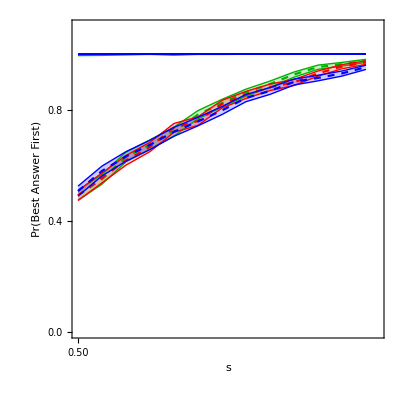

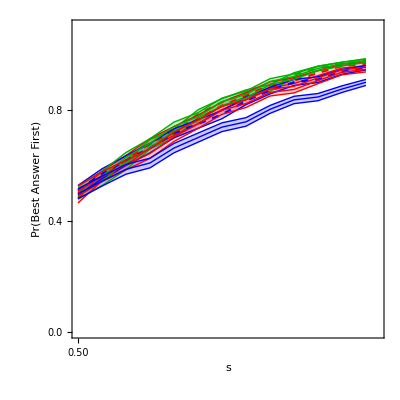

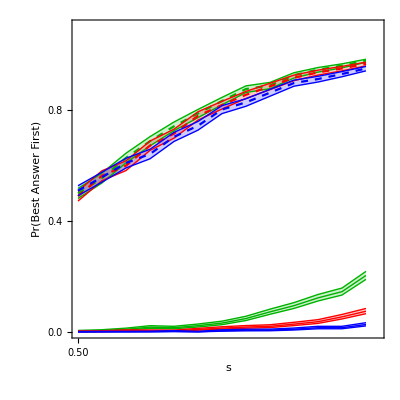

```mathematica
(*true p:green: 0.1, red: true (0.2), blue: 0.3*)
```

```mathematica
ListPlot[Flatten[{Table[qualplotdata[[;;,2,b]][[;;,i]],{b,3},{i,3}],Table[popplotdata[[;;,2,b]][[;;,i]],{b,3},{i,3}]},2],
Filling->{2->{3},5->{6},8->{9},11->{12},14->{15},17->{18},20->{21},23->{24},26->{27}},
Joined->True,
PlotStyle->{{RGBColor[0,0.7,0],Dashed},{RGBColor[0,0.7,0],Thin},{RGBColor[0,0.7,0],Thin},{Red,Dashed},{Red,Thin},{Red,Thin},{Blue,Dashed},{Blue,Thin},{Blue,Thin},{RGBColor[0,0.7,0],Thick},{RGBColor[0,0.7,0],Thin},{RGBColor[0,0.7,0],Thin},{Red,Thick},{Red,Thin},{Red,Thin},{Blue,Thick},{Blue,Thin},{Blue,Thin},{Black,Thick},{Black,Thin},{Black,Thin}},
Frame->True,
Axes->False,
Joined->True,
PlotRange->{{0.5,0.75001},{0,1.1}},
FrameLabel->{
Style["s",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Pr(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[0,20,0.05,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,20,0.05,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
},
AspectRatio->1
]
```

```mathematica
(*long time statistics*)
BootstrapMean[data_]:=Module[
{ResampledList,ResampledMeanDist},
(*Non-resampled bootstrap*)
n=10^4;
ResampledList=ArrayReshape[RandomChoice[data,Length[data] n],{Length[data],n}];
ResampledMeanDist=Total[ResampledList]/Length[data];(*Table[Mean[ResampledList[[i]]],{i,Length[ResampledList]}];*)
Return[N[{Mean[ResampledMeanDist],Quantile[ResampledMeanDist,{0.025,0.975}(*{0.159,0.841}*)]}]];
];

ds=0.005;
NumTrials=-1;
RunTime=20000;
dir="~/Dropbox/ExpFiles/new_sim_data/";
PopRankStatistics=Table[
Print[s];
data=Flatten[DeleteCases[Table[
file="popularity_rank_vote_sim_guess_p=0.200969true_p=0.200969s="<>ToString[s]<>"_num_recent_votes=all_bias=1.0_threshold="<>threshold<>"_t="<>ToString[RunTime]<>"_"<>"init_votes="<>ToString[numvotes]<>"_"<>ToString[trial]<>".csv";

If[FileExistsQ[dir<>file],
Import[dir<>file][[2;;]]
]
,{trial,15}],Null],1];
If[Length[data]>0,
n=Length[data[[;;NumTrials,1]]];
nn=Total[data[[;;NumTrials,1]]];
np=n-nn;
meanp=N[np/n];

pmax=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.975][[1,1]]//Normal;
pmin=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.025][[1,1]]//Normal;

MeanTopAnswer={meanp,{pmin,pmax}};
MeanTimeToThreshold=BootstrapMean[DeleteCases[data[[;;NumTrials,-1]],-1]];
{MeanTopAnswer,MeanTimeToThreshold}
,
Table[{Null,{Null,Null}},{2}]
]
,{s,0.5,0.751,ds}
,{numvotes,{0,10,200}}
,{threshold,{"15"(*,"20","30"*)}}];


QualityRankStatistics=Table[

data=Flatten[DeleteCases[Table[
file="quality_rank_vote_sim_guess_p=0.200969true_p=0.200969s="<>ToString[s]<>"_num_recent_votes=all_bias=0.5_threshold="<>threshold<>"_t="<>ToString[RunTime]<>"_"<>"init_votes="<>ToString[numvotes]<>"_"<>ToString[trial]<>".csv";
If[FileExistsQ[dir<>file],
Import[dir<>file][[2;;]]
]
,{trial,15}],Null],1];
If[Length[data]>0,
n=Length[data[[;;NumTrials,1]]];
nn=Total[data[[;;NumTrials,1]]];
np=n-nn;
meanp=N[np/n];

pmax=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.975][[1,1]]//Normal;
pmin=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.025][[1,1]]//Normal;

MeanTopAnswer={meanp,{pmin,pmax}};
MeanTimeToThreshold=BootstrapMean[DeleteCases[data[[;;NumTrials,-1]],-1]];
{MeanTopAnswer,MeanTimeToThreshold}
,
Table[{Null,{Null,Null}},{2}]
]
,{s,0.5,0.52,ds}
,{numvotes,{0(*,10,200*)}}
,{threshold,{"15"}}];
```

0.5

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.5

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

0.5

0.505

0.505

0.505

0.51

0.51

0.51

0.515

0.515

0.515

0.52

0.52

0.52

0.525

0.525

0.525

0.53

0.53

0.53

0.535

0.535

0.535

0.54

0.54

0.54

0.545

0.545

0.545

0.55

0.55

0.55

0.555

0.555

0.555

0.56

0.56

0.56

0.565

0.565

0.565

0.57

0.57

0.57

0.575

0.575

0.575

0.58

0.58

0.58

0.585

0.585

0.585

0.59

0.59

0.59

0.595

0.595

0.595

0.6

0.6

0.6

0.605

0.605

0.605

0.61

0.61

0.61

0.615

0.615

0.615

0.62

0.62

0.62

0.625

0.625

0.625

0.63

0.63

0.63

0.635

0.635

0.635

0.64

0.64

0.64

0.645

0.645

0.645

0.65

0.65

0.65

0.655

0.655

0.655

0.66

0.66

0.66

0.665

0.665

0.665

0.67

0.67

0.67

0.675

0.675

0.675

0.68

0.68

0.68

0.685

0.685

0.685

0.69

0.69

0.69

0.695

0.695

0.695

0.7

0.7

0.7

0.705

0.705

0.705

0.71

0.71

0.71

0.715

0.715

0.715

0.72

0.72

0.72

0.725

0.725

0.725

0.73

0.73

0.73

0.735

0.735

0.735

0.74

0.74

0.74

0.745

0.745

0.745

0.75

0.75

0.75

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

```mathematica
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
BootstrapMean[data_]:=Module[
{ResampledList,ResampledMeanDist},
(*Non-resampled bootstrap*)
n=10^4;
ResampledList=ArrayReshape[RandomChoice[data,Length[data] n],{Length[data],n}];
ResampledMeanDist=Total[ResampledList]/Length[data];(*Table[Mean[ResampledList[[i]]],{i,Length[ResampledList]}];*)
Return[N[{Mean[ResampledMeanDist],Quantile[ResampledMeanDist,{0.025,0.975}(*{0.159,0.841}*)]}]];
];
Needs["CustomTicks`"];
Needs["ErrorBarPlots`"];
NumTrials=20;
RunTime=20;

dir="~/Dropbox/ExpFiles/new_sim_data/";
Clear[deltaQ,bias,threshold,p];
(*initially 10 votes, randomly permuted*)
PopRankStatistics=Table[

data=Flatten[DeleteCases[Table[
file="popularity_rank_vote_sim_s="<>ToString[s]<>"_num_recent_votes=all_bias="<>bias<>"_threshold="<>threshold<>"_t="<>ToString[RunTime]<>"_"<>"init_votes=1"<>"_"<>ToString[trial]<>".csv";
If[FileExistsQ[dir<>file],
Import[dir<>file][[2;;]]
]
,{trial,15}],Null],1];
If[Length[data]>0,
n=Length[data[[;;NumTrials,1]]];
nn=Total[data[[;;NumTrials,1]]];
np=n-nn;
meanp=N[np/n];

pmax=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.975][[1,1]]//Normal;
pmin=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.025][[1,1]]//Normal;

MeanTopAnswer={meanp,{pmin,pmax}};
MeanTimeToThreshold=BootstrapMean[DeleteCases[data[[;;NumTrials,-1]],-1]];
{MeanTopAnswer,MeanTimeToThreshold}
,
Table[{Null,{Null,Null}},{2}]
]
,{s,0.5,0.751,0.02}
,{bias,{(*"0.1","0.5",*)"0.0","1.0"}}
,{threshold,{"15"(*,"20","30"*)}}];

(*
HighBiasPopRankStatistics=Table[

data=Flatten[DeleteCases[Table[
file="popularity_rank_vote_sim_s="<>ToString[s]<>"_num_recent_votes=all_bias=1.0_threshold="<>threshold<>"_t="<>ToString[RunTime]<>"_init_votes="<>initvotes<>"_"<>ToString[trial]<>".csv";
If[FileExistsQ[dir<>file],
Import[dir<>file][[2;;]]
]
,{trial,15}],Null],1];
If[Length[data]>0,
n=Length[data[[;;NumTrials,1]]];
nn=Total[data[[;;NumTrials,1]]];
np=n-nn;
meanp=N[np/n];

pmax=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.975][[1,1]]//Normal;
pmin=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.025][[1,1]]//Normal;

MeanTopAnswer={meanp,{pmin,pmax}};
MeanTimeToThreshold=BootstrapMean[DeleteCases[data[[;;NumTrials,-1]],-1]];
{MeanTopAnswer,MeanTimeToThreshold}
,
Table[{Null,{Null,Null}},{2}]
]
,{s,0.5,0.751,0.01}
,{initvotes,{"200","500"}}
,{threshold,{"15"(*,"20","30"*)}}];
*)
QualityRankStatistics=Table[

data=Flatten[DeleteCases[Table[
file="quality_rank_vote_sim_s="<>ToString[s]<>"_num_recent_votes=all_bias="<>bias<>"_threshold="<>threshold<>"_t="<>ToString[RunTime]<>"_"<>"init_votes=1"<>"_"<>ToString[trial]<>".csv";
If[FileExistsQ[dir<>file],
Import[dir<>file][[2;;]]
]
,{trial,15}],Null],1];
If[Length[data]>0,
n=Length[data[[;;NumTrials,1]]];
nn=Total[data[[;;NumTrials,1]]];
np=n-nn;
meanp=N[np/n];

pmax=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.975][[1,1]]//Normal;
pmin=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.025][[1,1]]//Normal;

MeanTopAnswer={meanp,{pmin,pmax}};
MeanTimeToThreshold=BootstrapMean[DeleteCases[data[[;;NumTrials,-1]],-1]];
{MeanTopAnswer,MeanTimeToThreshold}
,
Table[{Null,{Null,Null}},{2}]
]
,{s,0.5,0.751,0.02}
,{bias,{(*"0.1","0.5",*)"0.0","1.0"}}
,{threshold,{"15"(*,"20","30"*)}}];


PopLineFit=Table[
data=Flatten[DeleteCases[Table[
file="popularity_rank_vote_sim_s="<>ToString[s]<>"_num_recent_votes=all_bias="<>bias<>"_threshold="<>threshold<>"_t="<>ToString[RunTime]<>"_"<>"init_votes=1"<>"_"<>ToString[trial]<>".csv";
If[FileExistsQ[dir<>file],
Import[dir<>file][[2;;]]
]
,{trial,15}],Null],1];
If[Length[data]>0,

TopAnswer=data[[;;NumTrials,1]];
TimeToThreshold=DeleteCases[data[[;;NumTrials,-1]],-1];
{TopAnswer,TimeToThreshold}
,
{Null,Null}
]
,{s,0.5,0.741,0.02}
,{bias,{"0.0","1.0"}}
,{threshold,{"15"(*,"20","30"*)}}];
QualityLineFit=Table[
data=Flatten[DeleteCases[Table[
file="quality_rank_vote_sim_s="<>ToString[s]<>"_num_recent_votes=all_bias="<>bias<>"_threshold="<>threshold<>"_t="<>ToString[RunTime]<>"_"<>"init_votes=1"<>"_"<>ToString[trial]<>".csv";
If[FileExistsQ[dir<>file],
Import[dir<>file][[2;;]]
]
,{trial,15}],Null],1];
If[Length[data]>0,
TopAnswer=data[[;;NumTrials,1]];
TimeToThreshold=DeleteCases[data[[;;NumTrials,-1]],-1];
{TopAnswer,TimeToThreshold}
,
{Null,Null}
]
,{s,0.5,0.741,0.02}
,{bias,{"0.0","1.0"}}
,{threshold,{"15"(*,"20","30"*)}}];
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

RandomChoice::lrwl: The items for choice {} should be a non-empty list or a rule weights -> choices.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[RandomChoice[{},0],{0,10000}].

Power::infy: Infinite expression 1/0 encountered.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

RandomChoice::lrwl: The items for choice {} should be a non-empty list or a rule weights -> choices.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[RandomChoice[{},0],{0,10000}].

Power::infy: Infinite expression 1/0 encountered.

RandomChoice::lrwl: The items for choice {} should be a non-empty list or a rule weights -> choices.

General::stop: Further output of RandomChoice::lrwl will be suppressed during this calculation.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[RandomChoice[{},0],{0,10000}].

General::stop: Further output of ArrayReshape::listrp will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

RandomChoice::lrwl: The items for choice {} should be a non-empty list or a rule weights -> choices.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[RandomChoice[{},0],{0,10000}].

Power::infy: Infinite expression 1/0 encountered.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

RandomChoice::lrwl: The items for choice {} should be a non-empty list or a rule weights -> choices.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[RandomChoice[{},0],{0,10000}].

Power::infy: Infinite expression 1/0 encountered.

RandomChoice::lrwl: The items for choice {} should be a non-empty list or a rule weights -> choices.

General::stop: Further output of RandomChoice::lrwl will be suppressed during this calculation.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[RandomChoice[{},0],{0,10000}].

General::stop: Further output of ArrayReshape::listrp will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
numbias=3;
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
Dimensions[QualityRankStatistics]
qualrankplotdata=Table[
DeleteCases[Table[
If[s<=Length[QualityRankStatistics],
b=QualityRankStatistics[[;;,i,1]][[s,1]];
If[!b[[1]]===Null,
{{0.5 +(s-1) 0.005,b[[1]]},{0.5+ (s-1) 0.005,b[[2,1]]},{0.5 +(s-1) 0.005,b[[2,2]]}}
]
,
{{0.5 +(s-1) 0.005,1},{0.5+ (s-1) 0.005,1},{0.5 +(s-1) 0.005,1}}
]
,{s,2 Length[PopRankStatistics]}],Null]
,{i,(*numbias*)1}];

poprankplotdata=Table[
DeleteCases[Table[
b=PopRankStatistics[[;;,i,1]][[s,1]];
If[!b[[1]]===Null,
{{0.5 +(s-1) ds,b[[1]]},{0.5 +(s-1) ds,b[[2,1]]},{0.5 +(s-1) ds,b[[2,2]]}}
]
,{s,Length[PopRankStatistics]}],Null]
,{i,numbias}];

highbiaspoprankplotdata=Table[
DeleteCases[Table[
b=HighBiasPopRankStatistics[[;;,i,1]][[s,1]];
If[!b[[1]]===Null,
{{0.5 +(s-1) ds,b[[1]]},{0.5 +(s-1) ds,b[[2,1]]},{0.5 +(s-1) ds,b[[2,2]]}}
]
,{s,Length[HighBiasPopRankStatistics]}],Null]
,{i,numbias}];

plotdata=Flatten[{Table[qualrankplotdata[[i,;;,j]],{i,1},{j,3}],Table[poprankplotdata[[i,;;,j]],{i,numbias},{j,3}],{{Table[{x,1-HeavisideTheta[1-critpoint-x]},{x,0.5,1,0.001}]}}(*,
Table[highbiaspoprankplotdata[[i,;;,j]],{i,2},{j,3}]*)
},2];
exportdata=Flatten[Table[{plotdata[[i,;;,1]],plotdata[[i,;;,2]]},{i,Length[plotdata]}],1];
label={"s","quality_rank_mean","s","quality_rank_95%Quantile_lower","s","quality_rank_95%Quantile_upper","s","popularity_0_rank_mean","s","popularity_0_rank_95%Quantile_lower","s","popularity_0_rank_95%Quantile_upper","s","popularity_10_rank_mean","s","popularity_10_rank_95%Quantile_lower","s","popularity_10_rank_95%Quantile_upper","s","popularity_200_rank_mean","s","popularity_200_rank_95%Quantile_lower","s","popularity_200_rank_95%Quantile_upper","s","Theory"};
Do[PrependTo[exportdata[[i]],label[[i]]],{i,Length[label]}];

Export["~/Downloads/SimulationData.csv",exportdata,"CSV"]
scrit[p_]:=s/.Solve[p+(1-p) s==(1-p) (1-s),s][[1,1]];
critpoint=scrit[0.200969];
ListLinePlot[Table[{x,1-HeavisideTheta[1-critpoint-x]},{x,0.5,1,0.001}],PlotStyle->{Black,Thick}]
Show[
ListPlot[plotdata,
Filling->{2->{3},5->{6},8->{9},11->{12},14->{15},17->{18}},
PlotStyle->{{RGBColor[0,0.7,0],Dashed},{RGBColor[0,0.7,0],Thin},{RGBColor[0,0.7,0],Thin},{RGBColor[0,0.7,0],Thick},{RGBColor[0,0.7,0],Thin},{RGBColor[0,0.7,0],Thin},{Red,Thick},{Red,Thin},{Red,Thin},{Blue,Thick},{Blue,Thin},{Blue,Thin},{Black,Thick},{Black,Thin},{Black,Thin}},
Frame->True,
Axes->False,
Joined->True,
PlotRange->{{0.5,0.70001},{-0.05,1.05}},
FrameLabel->{
Style["s",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Pr(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[0,20,0.05,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,20,0.05,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
},
AspectRatio->1,
PlotLegends->Flatten[Table[Table[Style[x,FontFamily->"Arial",FontSize->15],{3}],{x,{"Quality","0","10","200","Theory"}}]]
](*,
ListLinePlot[Table[{x,1-HeavisideTheta[1-critpoint-x]},{x,0.5,1,0.001}],PlotStyle->{Black,Thick}]*)
]

1-critpoint
```

{5,1,1,2,2}

Export::infer: Cannot infer format of file s.

Export::chtype: First argument 0.5 is not a valid file specification.

Export::chtype: First argument 0.505 is not a valid file specification.

Export::chtype: First argument 0.51 is not a valid file specification.

General::stop: Further output of Export::chtype will be suppressed during this calculation.

Export::infer: Cannot infer format of file quality_rank_mean.

Export::infer: Cannot infer format of file s.

General::stop: Further output of Export::infer will be suppressed during this calculation.

~/Downloads/SimulationData.csv

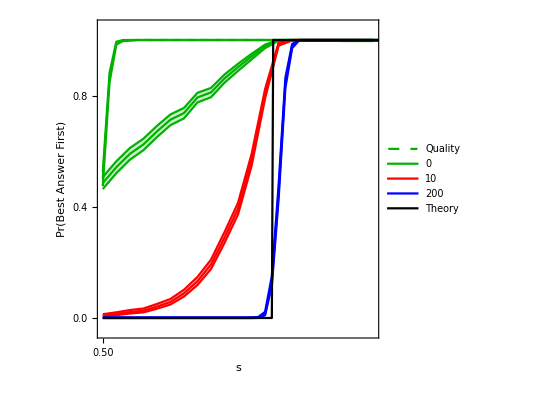

0.625758

0.625758

0.625758

```mathematica
p
```

| Estimate | Standard Error | z-Statistic | P-Value
1 | 8.32282 | 1.86022 | 4.47409 | 7.6736×10^-6
x | -17.0496 | 3.27393 | -5.20767 | 1.91222×10^-7

| Estimate | Standard Error | z-Statistic | P-Value
1 | 8.83276 | 1.58393 | 5.57648 | 2.4543×10^-8
x | -16.8642 | 2.7315 | -6.17397 | 6.65944×10^-10

-0.0769231

0.0250307

Part::partw: Part 2 of {{{0.4,{0.218197,0.615646}},{Mean[ComplexInfinity],Quantile[ComplexInfinity,{0.025,0.975}]}}} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2,1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of {{{{0.5,{0.297807,0.702193}},{Mean[ComplexInfinity],Quantile[ComplexInfinity,{0.025,0.975}]}}},{{{0.4,{0.218197,0.615646}},{Mean[ComplexInfinity],Quantile[ComplexInfinity,{0.025,0.975}]}}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

0.209213

0.0058864

{0.,-0.0769231}

{0.,0.138462}

| Estimate | Standard Error | z-Statistic | P-Value
1 | 8.32282 | 1.86022 | 4.47409 | 7.6736×10^-6
x | -17.0496 | 3.27393 | -5.20767 | 1.91222×10^-7

| Estimate | Standard Error | z-Statistic | P-Value
1 | 8.83276 | 1.58393 | 5.57648 | 2.4543×10^-8
x | -16.8642 | 2.7315 | -6.17397 | 6.65944×10^-10

-0.0769231

0.0250307

0.209213

0.0058864

{0.,-0.0769231}

{0.,0.138462}

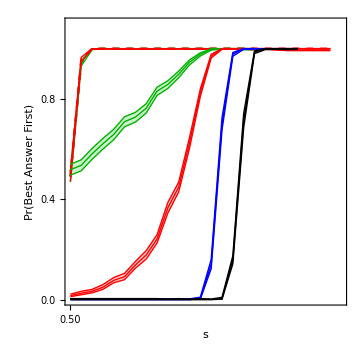

```mathematica
(*let the worse answer get 1 more vote than the better*)

(*can we prove that the p vs. s functions are statistically significantly different?*)
(*Naive: logistic*)
popdat=Flatten[Table[{0.5+(s-1) 0.02,Flatten[PopLineFit[[s,1,;;,1]],1][[j]]},{s,Length[PopLineFit]},{j,NumTrials}],1];
qualdat=Flatten[Table[{0.5+(s-1) 0.02,Flatten[QualityLineFit[[s,1,;;,1]],1][[j]]},{s,Length[QualityLineFit]},{j,NumTrials}],1];

LogitModelFit[popdat,x,x]["ParameterTable"]
LogitModelFit[qualdat,x,x]["ParameterTable"]
N[Mean[popdat[[;;,2]]]-Mean[qualdat[[;;,2]]]]
MannWhitneyTest[{popdat[[;;,2]],qualdat[[;;,2]]}]
MannWhitneyTest[{qualrankplotdata[[1,;;,1]],poprankplotdata[[1,;;,1]]}]
MannWhitneyTest[{qualrankplotdata[[1,;;,1]],poprankplotdata[[2,;;,1]]}]
Mean[qualrankplotdata[[1,;;,1]]-poprankplotdata[[1,;;,1]]]
Mean[qualrankplotdata[[1,;;,1]]-poprankplotdata[[2,;;,1]]]
```

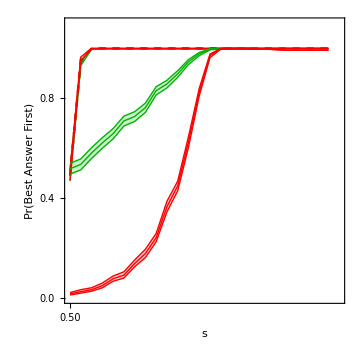

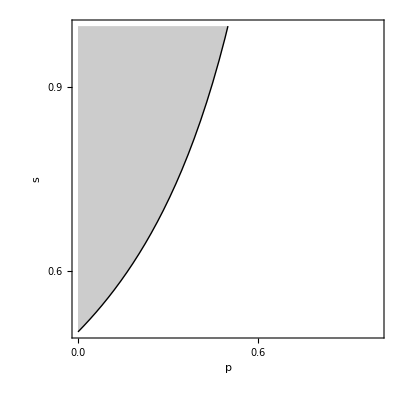

```mathematica
(*finding critical point:*)
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]

Needs["CustomTicks`"];
scrit[p_]:=s/.Solve[p+(1-p) s==(1-p) (1-s),s][[1,1]];
Plot[1-scrit[p],{p,0,1},
PlotRange->{{0,1},{0.5,1}},
Frame->True,
PlotStyle->{Black,Thick},
Filling->1,
Frame->True,
Axes->False,
FrameLabel->{
Style["p",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["s",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.1,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.1,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
},
AspectRatio->1
]
```

```mathematica
dir="~/Dropbox/ExpFiles/new_sim_data/";
quality=Table[
If[s≤0.535,
s=Round[s,0.005];
top=DeleteCases[Flatten[Table[
file=dir<>"quality_rank_vote_sim_guess_p=0.2true_p=0.2r=0.09s="<>ToString[s]<>"_num_recent_votes=all_bias=1.0_threshold=15_t=20000_init_votes=0_"<>ToString[trial]<>".csv";
If[FileExistsQ[file],
Import[file][[2;;,1]]
]
,{trial,20}]],Null];
n=Length[top];
nn=Total[top];
np=n-nn;
meanp=N[np/n];

pmax=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.975][[1,1]]//Normal;
pmin=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.025][[1,1]]//Normal;
{s,meanp,pmin,pmax},
{s,1,1,1}
]
,{s,0.5,0.7,0.005}];


popularity=Table[DeleteCases[Table[
s=Round[s,0.005];
top=DeleteCases[Flatten[
Table[
file=dir<>"popularity_rank_vote_sim_guess_p=0.2true_p=0.2r=0.09s="<>ToString[s]<>"_num_recent_votes=all_bias=1.0_threshold=15_t=20000_init_votes="<>ToString[numvotes]<>"_"<>ToString[trial]<>".csv";
If[FileExistsQ[file],
Import[file][[2;;,1]]
]
,{trial,20}]],Null];
n=Length[top];
If[n>0,
nn=Total[top];
np=n-nn;
meanp=N[np/n];

pmax=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.975][[1,1]]//Normal;
pmin=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.025][[1,1]]//Normal;
{s,meanp,pmin,pmax}
]
,{s,0.5,0.7,0.005}],Null]
,{numvotes,{0,10,200}}];
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

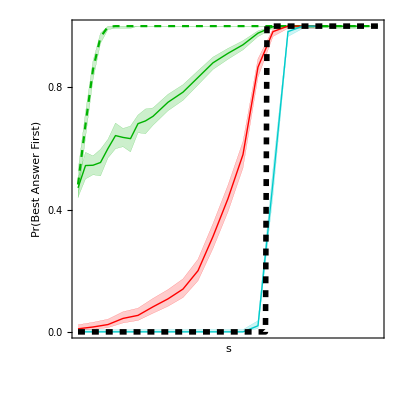

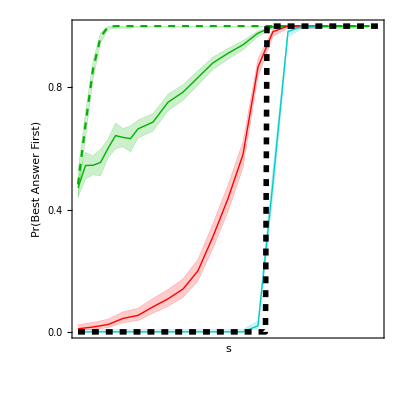

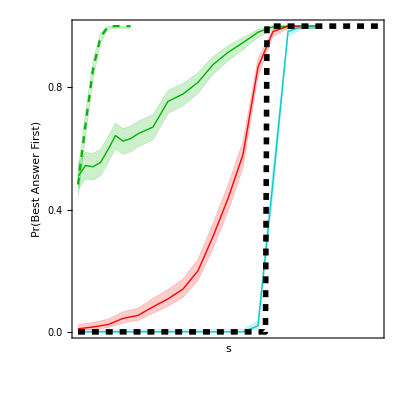

```mathematica
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
Needs["CustomTicks`"];

scrit[p_]:=s/.Solve[p+(1-p) s==(1-p) (1-s),s][[1,1]];
critpoint=scrit[0.200001];

ListLinePlot[Flatten[{Table[quality[[;;,{1,j}]],{j,2,4}],Flatten[Table[popularity[[i,;;,{1,j}]],{i,3},{j,2,4}],1],{Table[{x,1-HeavisideTheta[1-critpoint-x]},{x,0.5,1,0.001}]}},1],
PlotRange->{{0.5,0.70001},{0,1}},
PlotStyle->{{RGBColor[0,0.7,0],Dashed},{RGBColor[0,0.7,0],Thickness[0]},{RGBColor[0,0.7,0],Thickness[0]},{RGBColor[0,0.7,0],Thick},{RGBColor[0,0.7,0],Thickness[0]},{RGBColor[0,0.7,0],Thickness[0]},{RGBColor[1,0,0],Thick},{RGBColor[1,0,0],Thickness[0]},{RGBColor[1,0,0],Thickness[0]},
{RGBColor[0,0.8,0.8],Thick},{RGBColor[0,0.8,0.8],Thickness[0]},{RGBColor[0,0.8,0.8],Thickness[0]},{Black,Thickness[0.01],Dashed}},
Filling->{2->{3},5->{6},8->{9},11->{12}},
Frame->True,
Axes->False,
FrameLabel->{
Style["s",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Pr(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[0,2,0.05,5,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.05,5,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
},
AspectRatio->1
]
```

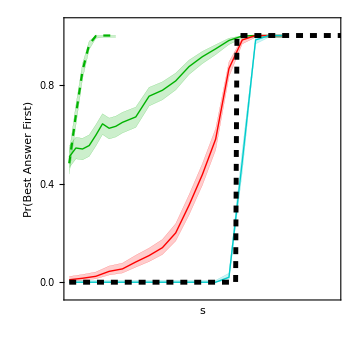

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

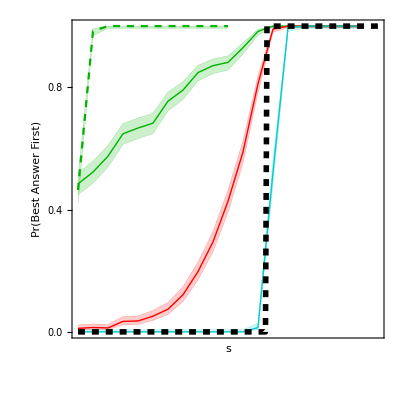

```mathematica
dir="~/Dropbox/ExpFiles/new_sim_data/";
quality=Table[

s=Round[s,0.005];
top=DeleteCases[Flatten[Table[
file=dir<>"quality_rank_vote_sim_guess_p=0.2true_p=0.2r=0.0s="<>ToString[s]<>"_num_recent_votes=all_bias=1.0_threshold=15_t=20000_init_votes=0_"<>ToString[trial]<>".csv";
If[FileExistsQ[file],
Import[file][[2;;,1]]
]
,{trial,20}]],Null];
n=Length[top];
nn=Total[top];
np=n-nn;
meanp=N[np/n];

pmax=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.975][[1,1]]//Normal;
pmin=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.025][[1,1]]//Normal;
{s,meanp,pmin,pmax}
,{s,0.5,0.6,0.01}];


popularity=Table[DeleteCases[Table[
s=Round[s,0.005];
top=DeleteCases[Flatten[
Table[
file=dir<>"popularity_rank_vote_sim_guess_p=0.2true_p=0.2r=0.0s="<>ToString[s]<>"_num_recent_votes=all_bias=1.0_threshold=15_t=20000_init_votes="<>ToString[numvotes]<>"_"<>ToString[trial]<>".csv";
If[FileExistsQ[file],
Import[file][[2;;,1]]
]
,{trial,20}]],Null];
n=Length[top];
If[n>0,
nn=Total[top];
np=n-nn;
meanp=N[np/n];

pmax=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.975][[1,1]]//Normal;
pmin=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.025][[1,1]]//Normal;
{s,meanp,pmin,pmax}
]
,{s,0.5,0.7,0.01}],Null]
,{numvotes,{0,10,200}}];


Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
Needs["CustomTicks`"];

scrit[p_]:=s/.Solve[p+(1-p) s==(1-p) (1-s),s][[1,1]];
critpoint=scrit[0.200001];

ListLinePlot[Flatten[{Table[quality[[;;,{1,j}]],{j,2,4}],Flatten[Table[popularity[[i,;;,{1,j}]],{i,3},{j,2,4}],1],{Table[{x,1-HeavisideTheta[1-critpoint-x]},{x,0.5,1,0.001}]}},1],
PlotRange->{{0.5,0.70001},{0,1}},
PlotStyle->{{RGBColor[0,0.7,0],Dashed},{RGBColor[0,0.7,0],Thickness[0]},{RGBColor[0,0.7,0],Thickness[0]},{RGBColor[0,0.7,0],Thick},{RGBColor[0,0.7,0],Thickness[0]},{RGBColor[0,0.7,0],Thickness[0]},{RGBColor[1,0,0],Thick},{RGBColor[1,0,0],Thickness[0]},{RGBColor[1,0,0],Thickness[0]},
{RGBColor[0,0.8,0.8],Thick},{RGBColor[0,0.8,0.8],Thickness[0]},{RGBColor[0,0.8,0.8],Thickness[0]},{Black,Thickness[0.01],Dashed}},
Filling->{2->{3},5->{6},8->{9},11->{12}},
Frame->True,
PlotStyle->{Black,Thick},
Filling->1,
Frame->True,
Axes->False,
FrameLabel->{
Style["s",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Pr(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[0,2,0.05,5,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.05,5,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
},
AspectRatio->1
]
```

```mathematica
dir="~/Dropbox/ExpFiles/new_sim_data/";
quality=Table[DeleteCases[Table[
s=Round[s,0.005];
top=DeleteCases[Flatten[Table[
file=dir<>"quality_rank_vote_sim_guess_p=0.2true_p="<>ToString[truep]<>"r=0.09s="<>ToString[s]<>"_num_recent_votes=all_bias=1.0_threshold=15_t=20000_init_votes=0_"<>ToString[trial]<>".csv";
If[FileExistsQ[file],
Import[file][[2;;,1]]
]
,{trial,40}]],Null];
Print[{truep,s,n}];
n=Length[top];
If[n>0,
nn=Total[top];
np=n-nn;
meanp=N[np/n];

pmax=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.975][[1,1]]//Normal;
pmin=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.025][[1,1]]//Normal;
{s,meanp,pmin,pmax}
]
,{s,0.5,0.65,0.01}],Null]
,{truep,{0.1,0.2,0.3}}];


popularity=Table[DeleteCases[Table[
s=Round[s,0.005];
top=DeleteCases[Flatten[
Table[
file=dir<>"popularity_rank_vote_sim_guess_p=0.2true_p="<>ToString[truep]<>"r=0.09s="<>ToString[s]<>"_num_recent_votes=all_bias=1.0_threshold=15_t=20000_init_votes="<>ToString[numvotes]<>"_"<>ToString[trial]<>".csv";
If[FileExistsQ[file],
Import[file][[2;;,1]]
]
,{trial,40}]],Null];
n=Length[top];
Print[{truep,numvotes,s,n}];
If[n>0,
nn=Total[top];
np=n-nn;
meanp=N[np/n];

pmax=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.975][[1,1]]//Normal;
pmin=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.025][[1,1]]//Normal;
{s,meanp,pmin,pmax}
]
,{s,0.5,0.80,0.01}],Null]
,{truep,{0.1,0.2,0.3}}
,{numvotes,{0,10,200}}];


Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
Needs["CustomTicks`"];

scrit[p_]:=s/.Solve[p+(1-p) s==(1-p) (1-s),s][[1,1]];
critpoint={scrit[0.100001],scrit[0.200001],scrit[0.300001]};

pltpnts=Flatten[{Flatten[Table[Table[quality[[p,;;,{1,j}]],{j,2,4}],{p,3}],1],Flatten[Table[Flatten[Table[popularity[[p,i,;;,{1,j}]],{i,3},{j,2,4}],1],{p,3}],1],Flatten[Table[{Table[{x,1-HeavisideTheta[1-critpoint[[p]]-x]},{x,0.5,1,0.001}]},{p,3}],1]},1];
colors=Flatten[{Table[{{c,Dashed},{c},{c}},{c,{RGBColor[0,1,0],RGBColor[0,0.7,0],RGBColor[0,0.5,0]}}],
Table[{{c,Thick},{c},{c}},{c,{RGBColor[0,1,0],RGBColor[1,0,0],RGBColor[0,0,1],RGBColor[0,0.7,0],RGBColor[0.8,0,0],RGBColor[0,0.8,0.8],RGBColor[0,0.5,0],RGBColor[.5,0,0],Black}}],{{{Lighter[Gray],Thickness[0.01],Dashed}},{{Gray,Thickness[0.01],Dashed}},{{Black,Thickness[0.01],Dashed}}}},2]

ListLinePlot[pltpnts,
PlotRange->{{0.5,0.750001},{0,1}},
PlotStyle->colors,
Filling->Table[i->{i+1},{i,2,35,3}],
Frame->True,
PlotStyle->{Black,Thick},
Filling->1,
Frame->True,
Axes->False,
FrameLabel->{
Style["s",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Pr(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[0,2,0.05,5,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.05,5,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
},
AspectRatio->1,
PlotLegends->Flatten[{Table[{s,"",""},{s,{"quality, p=0.1","quality, p=0.2","quality, p=0.3","0, p=0.1","0, p=0.2","0, p=0.3","-10, p=0.1","-10, p=0.2","-10, p=0.3","-200, p=0.1","-200, p=0.2","-200, p=0.3"}}],{"Theory, p=0.1","Theory, p=0.2","Theory, p=0.3"}}]
]
```

{0.3,200,0.61,1050}

{0.3,200,0.62,1050}

{0.3,200,0.63,1050}

{0.3,200,0.64,800}

{0.3,200,0.65,800}

{0.3,200,0.66,800}

{0.3,200,0.67,800}

{0.3,200,0.68,600}

{0.3,200,0.69,250}

{0.3,200,0.7,250}

{0.3,200,0.71,250}

{0.3,200,0.72,250}

{0.3,200,0.73,250}

{0.3,200,0.74,250}

{0.3,200,0.75,250}

{0.3,200,0.76,250}

{0.3,200,0.77,0}

{0.3,200,0.78,0}

{0.3,200,0.79,0}

{0.3,200,0.8,0}

{{RGBColor[0, 1, 0],Dashing[{Small,Small}]},{RGBColor[0, 1, 0]},{RGBColor[0, 1, 0]},{RGBColor[0, 0.7, 0],Dashing[{Small,Small}]},{RGBColor[0, 0.7, 0]},{RGBColor[0, 0.7, 0]},{RGBColor[0, 0.5, 0],Dashing[{Small,Small}]},{RGBColor[0, 0.5, 0]},{RGBColor[0, 0.5, 0]},{RGBColor[0, 1, 0],Thickness[Large]},{RGBColor[0, 1, 0]},{RGBColor[0, 1, 0]},{RGBColor[1, 0, 0],Thickness[Large]},{RGBColor[1, 0, 0]},{RGBColor[1, 0, 0]},{RGBColor[0, 0, 1],Thickness[Large]},{RGBColor[0, 0, 1]},{RGBColor[0, 0, 1]},{RGBColor[0, 0.7, 0],Thickness[Large]},{RGBColor[0, 0.7, 0]},{RGBColor[0, 0.7, 0]},{RGBColor[0.8, 0, 0],Thickness[Large]},{RGBColor[0.8, 0, 0]},{RGBColor[0.8, 0, 0]},{RGBColor[0, 0.8, 0.8],Thickness[Large]},{RGBColor[0, 0.8, 0.8]},{RGBColor[0, 0.8, 0.8]},{RGBColor[0, 0.5, 0],Thickness[Large]},{RGBColor[0, 0.5, 0]},{RGBColor[0, 0.5, 0]},{RGBColor[0.5, 0, 0],Thickness[Large]},{RGBColor[0.5, 0, 0]},{RGBColor[0.5, 0, 0]},{GrayLevel[0],Thickness[Large]},{GrayLevel[0]},{GrayLevel[0]},{RGBColor[0.6666666666666666, 0.6666666666666666, 0.6666666666666666],Thickness[0.01],Dashing[{Small,Small}]},{GrayLevel[0.5],Thickness[0.01],Dashing[{Small,Small}]},{GrayLevel[0],Thickness[0.01],Dashing[{Small,Small}]}}

-Graphics-

```mathematica
dir="~/Dropbox/ExpFiles/new_sim_data/";
quality=Table[
s=Round[s,0.005];
top=DeleteCases[Flatten[Table[
file=dir<>"quality_rank_vote_sim_guess_p=0.2true_p=0.2r=0.09s="<>ToString[s]<>"_num_recent_votes=all_bias=1.0_threshold=15_t=20_init_votes=0_"<>ToString[trial]<>".csv";
If[FileExistsQ[file],
Import[file][[2;;,1]]
]
,{trial,20}]],Null];
n=Length[top];
nn=Total[top];
np=n-nn;
meanp=N[np/n];

pmax=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.975][[1,1]]//Normal;
pmin=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.025][[1,1]]//Normal;
{s,meanp,pmin,pmax}
,{s,0.5,0.799,0.01}];

popularity=Table[DeleteCases[Table[
s=Round[s,0.005];
top=DeleteCases[Flatten[
Table[
file=dir<>"popularity_rank_vote_sim_guess_p=0.2true_p=0.2r=0.09s="<>ToString[s]<>"_num_recent_votes=all_bias=1.0_threshold=15_t=20_init_votes="<>ToString[numvotes]<>"_"<>ToString[trial]<>".csv";
If[FileExistsQ[file],
Import[file][[2;;,1]]
]
,{trial,20}]],Null];
n=Length[top];
If[n>0,
nn=Total[top];
np=n-nn;
meanp=N[np/n];

pmax=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.975][[1,1]]//Normal;
pmin=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.025][[1,1]]//Normal;
{s,meanp,pmin,pmax}
]
,{s,0.5,0.799,0.01}],Null]
,{numvotes,{0,10}}];



Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
Needs["CustomTicks`"];

scrit[p_]:=s/.Solve[p+(1-p) s==(1-p) (1-s),s][[1,1]];
critpoint=scrit[0.20000001];

ListLinePlot[Flatten[{Table[quality[[;;,{1,j}]],{j,2,4}],Flatten[Table[popularity[[i,;;,{1,j}]],{i,2},{j,2,4}],1],{Table[{x,1-HeavisideTheta[1-critpoint-x]},{x,0.5,1,0.001}]}},1],
PlotRange->{{0.5,0.80001},{0,1}},
PlotStyle->{{RGBColor[0,0.7,0],Dashed},{RGBColor[0,0.7,0],Thickness[0]},{RGBColor[0,0.7,0],Thickness[0]},{RGBColor[0,0.7,0],Thick},{RGBColor[0,0.7,0],Thickness[0]},{RGBColor[0,0.7,0],Thickness[0]},{RGBColor[1,0,0],Thick},{RGBColor[1,0,0],Thickness[0]},{RGBColor[1,0,0],Thickness[0]},
{Black,Thickness[0.01],Dashed}},
Filling->{2->{3},5->{6},8->{9},11->{12}},
Frame->True,
PlotStyle->{Black,Thick},
Filling->1,
Frame->True,
Axes->False,
FrameLabel->{
Style["s",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Pr(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[0,2,0.05,5,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.05,5,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
},
AspectRatio->1
]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

-Graphics-

```mathematica
BootstrapMean[data_]:=Module[
{ResampledList,ResampledMeanDist},
(*Non-resampled bootstrap*)
n=10^4;
ResampledList=ArrayReshape[RandomChoice[data,Length[data] n],{Length[data],n}];
ResampledMeanDist=Total[ResampledList]/Length[data];(*Table[Mean[ResampledList[[i]]],{i,Length[ResampledList]}];*)
Return[N[{Mean[ResampledMeanDist],Quantile[ResampledMeanDist,{0.025,0.975}(*{0.159,0.841}*)]}]];
];
BootstrapMean[quality[[;;,2]]-popularity[[1,;;,2]]]
SignedRankTest[quality[[;;,2]]-popularity[[1,;;,2]]]
```

{0.02345,{0.0197056,0.0269417}}

5.11086×10^-13

2.22901×10^-6

```mathematica
(*dir="~/Dropbox/ExpFiles/new_sim_data/";
quality2=Table[

s=Round[s,0.005];
top=DeleteCases[Flatten[Table[
file=dir<>"quality_rank_vote_sim_guess_p=0.2true_p=0.2r=0.0s="<>ToString[s]<>"_num_recent_votes=all_bias=1.0_threshold=15_t=20_init_votes=0_"<>ToString[trial]<>".csv";
If[FileExistsQ[file],
Import[file][[2;;,1]]
]
,{trial,20}]],Null];
n=Length[top];
nn=Total[top];
np=n-nn;
meanp=N[np/n];

pmax=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.975][[1,1]]//Normal;
pmin=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.025][[1,1]]//Normal;
{s,meanp,pmin,pmax}
,{s,0.5,0.799,0.01}]


popularity2=Table[DeleteCases[Table[
s=Round[s,0.005];
top=DeleteCases[Flatten[
Table[
file=dir<>"popularity_rank_vote_sim_guess_p=0.2true_p=0.2r=0.0s="<>ToString[s]<>"_num_recent_votes=all_bias=1.0_threshold=15_t=20_init_votes="<>ToString[numvotes]<>"_"<>ToString[trial]<>".csv";
If[FileExistsQ[file],
Import[file][[2;;,1]]
]
,{trial,20}]],Null];
n=Length[top];
If[n>0,
nn=Total[top];
np=n-nn;
meanp=N[np/n];

pmax=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.975][[1,1]]//Normal;
pmin=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.025][[1,1]]//Normal;
{s,meanp,pmin,pmax}
]
,{s,0.5,0.799,0.01}],Null]
,{numvotes,{0,10}}];

*)
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
Needs["CustomTicks`"];

scrit[p_]:=s/.Solve[p+(1-p) s==(1-p) (1-s),s][[1,1]];
critpoint=scrit[0.20001];

ListLinePlot[Flatten[{Table[quality2[[;;,{1,j}]],{j,2,4}],Flatten[Table[popularity2[[i,;;,{1,j}]],{i,2},{j,2,4}],1],{Table[{x,1-HeavisideTheta[1-critpoint-x]},{x,0.5,1,0.001}]}},1],
PlotRange->{{0.5,0.80001},{0,1}},
PlotStyle->{{RGBColor[0,0.7,0],Dashed},{RGBColor[0,0.7,0],Thickness[0]},{RGBColor[0,0.7,0],Thickness[0]},{RGBColor[0,0.7,0],Thick},{RGBColor[0,0.7,0],Thickness[0]},{RGBColor[0,0.7,0],Thickness[0]},{RGBColor[1,0,0],Thick},{RGBColor[1,0,0],Thickness[0]},{RGBColor[1,0,0],Thickness[0]},
{Black,Thickness[0.01],Dashed}},
Filling->{2->{3},5->{6},8->{9},11->{12}},
Frame->True,
PlotStyle->{Black,Thick},
Filling->1,
Frame->True,
Axes->False,
FrameLabel->{
Style["s",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Pr(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[0,2,0.05,5,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.05,5,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
},
AspectRatio->1
]
```

-Graphics-

```mathematica
BootstrapMean[data_]:=Module[
{ResampledList,ResampledMeanDist},
(*Non-resampled bootstrap*)
n=10^4;
ResampledList=ArrayReshape[RandomChoice[data,Length[data] n],{Length[data],n}];
ResampledMeanDist=Total[ResampledList]/Length[data];(*Table[Mean[ResampledList[[i]]],{i,Length[ResampledList]}];*)
Return[N[{Mean[ResampledMeanDist],Quantile[ResampledMeanDist,{0.025,0.975}(*{0.159,0.841}*)]}]];
];
BootstrapMean[quality2[[;;,2]]-popularity2[[1,;;,2]]]
SignedRankTest[quality2[[;;,2]]-popularity2[[1,;;,2]]]
```

{0.0246458,{0.0207583,0.0283667}}

2.47233×10^-6

```mathematica
(*dir="~/Dropbox/ExpFiles/new_sim_data/";
quality3=Table[
s=Round[s,0.005];
top=DeleteCases[Flatten[Table[
file=dir<>"quality_rank_vote_sim_guess_p=0.2true_p="<>ToString[truep]<>"r=0.09s="<>ToString[s]<>"_num_recent_votes=all_bias=1.0_threshold=15_t=20_init_votes=0_"<>ToString[trial]<>".csv";
If[FileExistsQ[file],
Import[file][[2;;,1]]
]
,{trial,20}]],Null];
n=Length[top];
nn=Total[top];
np=n-nn;
meanp=N[np/n];

pmax=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.975][[1,1]]//Normal;
pmin=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.025][[1,1]]//Normal;
{s,meanp,pmin,pmax}
,{truep,{0.1,0.2,0.3}}
,{s,0.5,0.799,0.01}];


popularity3=Table[DeleteCases[Table[
s=Round[s,0.005];
top=DeleteCases[Flatten[
Table[
file=dir<>"popularity_rank_vote_sim_guess_p=0.2true_p="<>ToString[truep]<>"r=0.09s="<>ToString[s]<>"_num_recent_votes=all_bias=1.0_threshold=15_t=20_init_votes="<>ToString[numvotes]<>"_"<>ToString[trial]<>".csv";
If[FileExistsQ[file],
Import[file][[2;;,1]]
]
,{trial,20}]],Null];
n=Length[top];
If[n>0,
nn=Total[top];
np=n-nn;
meanp=N[np/n];

pmax=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.975][[1,1]]//Normal;
pmin=p/.NSolve[CDF[BetaDistribution[1+np,1+nn],p]==0.025][[1,1]]//Normal;
{s,meanp,pmin,pmax}
]
,{s,0.5,0.799,0.01}],Null]
,{truep,{0.1,0.2,0.3}}
,{numvotes,{0,10}}];
*)

Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
Needs["CustomTicks`"];

scrit[p_]:=s/.Solve[p+(1-p) s==(1-p) (1-s),s][[1,1]];
critpoint=scrit[0.200001];

ListLinePlot[Flatten[{Flatten[Table[Table[quality3[[p,;;,{1,j}]],{j,2,4}],{p,3}],1],Flatten[Table[Flatten[Table[popularity3[[p,i,;;,{1,j}]],{i,2},{j,2,4}],1],{p,3}],1],{Table[{x,1-HeavisideTheta[1-critpoint-x]},{x,0.5,1,0.001}]}},1],
PlotRange->{{0.5,0.80001},{0,1}},
PlotStyle->Flatten[{Table[{{c,Dashed},{c,Thickness[0]},{c,Thickness[0]}},{c,{RGBColor[0,1,0],RGBColor[0,0.7,0],RGBColor[0,0.5,0]}}],
Table[{{c,Thick},{c,Thickness[0]},{c,Thickness[0]}},{c,{RGBColor[0,1,0],RGBColor[1,0,0],RGBColor[0,0.7,0],RGBColor[0.8,0,0],RGBColor[0,0.5,0],RGBColor[.5,0,0]}}],{{{Black,Thickness[0.01],Dashed}}}},2],
Filling->Table[i->{i+1},{i,2,40,3}],
Frame->True,
PlotStyle->{Black,Thick},
Filling->1,
Frame->True,
Axes->False,
FrameLabel->{
Style["s",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Pr(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[0,2,0.05,5,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.05,5,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
},
AspectRatio->1
]
```

-Graphics-

```mathematica
BootstrapMean[data_]:=Module[
{ResampledList,ResampledMeanDist},
(*Non-resampled bootstrap*)
n=10^4;
ResampledList=ArrayReshape[RandomChoice[data,Length[data] n],{Length[data],n}];
ResampledMeanDist=Total[ResampledList]/Length[data];(*Table[Mean[ResampledList[[i]]],{i,Length[ResampledList]}];*)
Return[N[{Mean[ResampledMeanDist],Quantile[ResampledMeanDist,{0.025,0.975}(*{0.159,0.841}*)]}]];
];
Table[
{BootstrapMean[quality3[[i,;;,2]]-popularity3[[i,1,;;,2]]],SignedRankTest[quality3[[i,;;,2]]-popularity3[[i,1,;;,2]]]}
,{i,3}]
```

{{{0.00306851,{-0.0000555556,0.00649167}},0.184552},{{0.023414,{0.0195917,0.0269444}},2.22901×10^-6},{{0.045356,{0.0399056,0.0502556}},1.81852×10^-6}}

```mathematica
dQ=Table[s,{s,0.5,0.75,0.02}];
n=NumTrials;
plotdata=Flatten[{Table[Table[
prob=1-PopRankStatistics[[;;,i,1]][[j,1,1]];
{dQ[[j]],prob},{j,Length[dQ]}],{i,3}],Table[Table[
prob=1-QualityRankStatistics[[;;,i,1]][[j,1,1]];
err=Sqrt[prob (1-prob)/n];
{dQ[[j]],prob},{j,Length[dQ]}],{i,3}],
Table[Table[
prob=1-PopRankStatistics[[;;,i,1]][[j,1,1]];
np=prob n;
nn=n-np;
pmin=p/.NSolve[CDF[BetaDistribution[np+1,nn+1],p]==0.025,p][[1]]//Normal;
(*err=Sqrt[prob (1-prob)/n];*)
{dQ[[j]],pmin},{j,Length[dQ]}],{i,3}],Table[Table[
prob=1-QualityRankStatistics[[;;,i,1]][[j,1,1]];
err=Sqrt[prob (1-prob)/n];
{dQ[[j]],prob-err},{j,Length[dQ]}],{i,3}],
Table[Table[
prob=1-PopRankStatistics[[;;,i,1]][[j,1,1]];
np=prob n;
nn=n-np;
pmax=p/.NSolve[CDF[BetaDistribution[np+1,nn+1],p]==0.975,p][[1]]//Normal;
(*err=Sqrt[prob (1-prob)/n];*)
{dQ[[j]],pmax},{j,Length[dQ]}],{i,3}],Table[Table[
prob=1-QualityRankStatistics[[;;,i,1]][[j,1,1]];
err=Sqrt[prob (1-prob)/n];
{dQ[[j]],prob+err},{j,Length[dQ]}],{i,3}]
},1];
Dimensions[plotdata]
ListPlot[plotdata,Joined->True,
PlotStyle->{{Blue,Thick},{RGBColor[0,0.7,0],Thick},{Red,Thick},{Blue,Thick,Dashed},{RGBColor[0,0.7,0],Thick,Dashed},{Red,Thick,Dashed},{Blue,Thin},{RGBColor[0,0.7,0],Thin},{Red,Thin},{Blue,Thin},{RGBColor[0,0.7,0],Thin},{Red,Thin},{Blue,Thin},{RGBColor[0,0.7,0],Thin},{Red,Thin},{Blue,Thin},{RGBColor[0,0.7,0],Thin},{Red,Thin}},
Filling->{7->{13},8->{14},9->{15},10->{16},11->{17},12->{18}},
Frame->True,
Axes->False,
Joined->True,
PlotRange->{{0.5,0.75001},{0,1}},
FrameLabel->{
Style["s",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Pr(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[0,20,0.05,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,20,0.05,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
}
,
PlotLegends->Flatten[{Table[Style[ToString[q],FontFamily->"Arial",FontSize->12],{q,{+9,0,-9}}],Table[Style[ToString[q],FontFamily->"Arial",FontSize->12],{q,{+9,0,-9}}]}]
](*
Do[
Print[
ListPlot[Flatten[{Table[Table[{dQ[[j]],PopRankStatistics[[;;,i,th]][[j,2,1]]},{j,Length[dQ]}],{i,3}],Table[Table[{dQ[[j]],QualityRankStatistics[[;;,i,th]][[j,2,1]]},{j,Length[dQ]}],{i,3}]},1],Joined->True,
PlotStyle->{{Blue,Thick},{RGBColor[0,0.7,0],Thick},{Red,Thick},{Blue,Thick,Dashed},{RGBColor[0,0.7,0],Thick,Dashed},{Red,Thick,Dashed}},
Frame->True,
Axes->False,
Joined->True,
PlotRange->{{0.5,0.70001},{0,100}},
FrameLabel->{
Style["s",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Time(ΔV > "<>ToString[{15,20,30}[[th]]]<>")",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,100,20,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,100,20,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[0,20,0.05,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,20,0.05,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
},
(*LegendFunction[LegendLabel->Style["Threshold",FontFamily->"Arial",FontSize->15]],*)
(*PlotLegends->{Style["15",FontFamily->"Arial",FontSize->12],Style["20",FontFamily->"Arial",FontSize->12],Style["30",FontFamily->"Arial",FontSize->12],Style["15",FontFamily->"Arial",FontSize->12],Style["20",FontFamily->"Arial",FontSize->12],Style["30",FontFamily->"Arial",FontSize->12]}*)
PlotLegends->Flatten[{Table[Style[ToString[q],FontFamily->"Arial",FontSize->12],{q,{+9,0,-9}}],Table[Style[ToString[q],FontFamily->"Arial",FontSize->12],{q,{+9,0,-9}}]}]
]];
,{th,3}]*)
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

{18,13,2}

```mathematica
(*1000 trials, 100 votes, 95% confidence intervals via Beta with uniform prior*)
```

```mathematica
(*3000 trials, 20 votes, 95% confidence intervals via beta distribution*)
```

```mathematica
-Graphics--Graphics-
```

{18,12,2}

0.

```mathematica
dQ=Table[s,{s,0.5,0.71,0.02}];
popdata=Flatten[Table[{0.5 +(j-1) 0.02,1-PopLineFit[[j,3,1]][[1,trial]]},{j,11},{trial,NumTrials}],1];

qualitydata=Flatten[Table[{0.5 +(j-1) 0.02,1-QualityLineFit[[j,3,1]][[1,trial]]},{j,11},{trial,NumTrials}],1];

k=2;
popglm=LogitModelFit[popdata,x,x]
qualityglm=LogitModelFit[qualitydata,x,x]
popglm[{"ParameterTable"}]
popglm["BIC"]
loglikelihood=Table[Log[popglm[popdata[[i,1]]]] popdata[[i,2]]+Log[(1-popglm[popdata[[i,1]]])] (1-popdata[[i,2]]),{i,Length[popdata]}];
Total[-2 loglikelihood]+Log[Length[popdata]] k

loglikelihood=Table[Log[qualityglm[popdata[[i,1]]]] popdata[[i,2]]+Log[(1-qualityglm[popdata[[i,1]]])] (1-popdata[[i,2]]),{i,Length[popdata]}];
poponqualBIC=Total[-2 loglikelihood]+Log[Length[popdata]] k

qualityglm[{"ParameterTable"}]
qualityglm["BIC"]

loglikelihood=Table[Log[qualityglm[qualitydata[[i,1]]]] qualitydata[[i,2]]+Log[(1-qualityglm[qualitydata[[i,1]]])] (1-qualitydata[[i,2]]),{i,Length[qualitydata]}];
Total[-2 loglikelihood]+Log[Length[qualitydata]] k

loglikelihood=Table[Log[popglm[qualitydata[[i,1]]]] qualitydata[[i,2]]+Log[(1-popglm[qualitydata[[i,1]]])] (1-qualitydata[[i,2]]),{i,Length[qualitydata]}];
poponqualBIC=Total[-2 loglikelihood]+Log[Length[qualitydata]] k

popp=Table[
votes=Select[popdata,#[[1]]==s&][[;;,2]];
n=Length[votes];
np=Total[votes];
nn=n-np;
(*95% confidence intervals via beta distribution*)
pmax=(p/.NSolve[CDF[BetaDistribution[np+1,nn+1],p]==0.975,p]//Normal)[[1]];
pmin=(p/.NSolve[CDF[BetaDistribution[np+1,nn+1],p]==0.025,p]//Normal)[[1]];
pav=np/n;
{s,pav,pmin,pmax}
,{s,0.5,0.70,0.02}];
qualp=Table[
votes=Select[qualitydata,#[[1]]==s&][[;;,2]];
n=Length[votes];
np=Total[votes];
nn=n-np;
(*95% confidence intervals via beta distribution*)
pmax=(p/.NSolve[CDF[BetaDistribution[np+1,nn+1],p]==0.975,p]//Normal)[[1]];
pmin=(p/.NSolve[CDF[BetaDistribution[np+1,nn+1],p]==0.025,p]//Normal)[[1]];
pav=np/n;
{s,pav,pmin,pmax}
,{s,0.5,0.70,0.02}]

Show[ListPlot[Flatten[{Table[popp[[;;,{1,j}]],{j,2,4}],Table[qualp[[;;,{1,j}]],{j,2,4}]},1](*Flatten[{Table[Table[{dQ[[j]],1-PopRankStatistics[[;;,i,1]][[j,1,1]]},{j,Length[dQ]}],{i,{3}}],
Table[Table[{dQ[[j]],1-PopRankStatistics[[;;,i,1]][[j,1,2,1]]},{j,Length[dQ]}],{i,{3}}],
Table[Table[{dQ[[j]],1-PopRankStatistics[[;;,i,1]][[j,1,2,2]]},{j,Length[dQ]}],{i,{3}}],Table[Table[{dQ[[j]],1-QualityRankStatistics[[;;,i,1]][[j,1,1]]},{j,Length[dQ]}],{i,{3}}],
Table[Table[{dQ[[j]],1-QualityRankStatistics[[;;,i,1]][[j,1,2,1]]},{j,Length[dQ]}],{i,{3}}],
Table[Table[{dQ[[j]],1-QualityRankStatistics[[;;,i,1]][[j,1,2,2]]},{j,Length[dQ]}],{i,{3}}]},1]*),Joined->True,
PlotStyle->Flatten[{{{{Red,Thick},{Red,Thin},{Red,Thin}}},{{(*{Blue,Thick,Dashed},{RGBColor[0,0.7,0],Thick,Dashed},*){Red,Thick,Dashed}}},Table[{(*{Blue,Thickness[0]},{RGBColor[0,0.7,0],Thickness[0]},*){Red,Thickness[0]}},{2}]},2],
(*Filling->{4->{7},5->{8},6->{9},11->{14},12->{15},13->{16}},*)
Filling->{2->{3},5->{6}},
Frame->True,
Axes->False,
Joined->True,
PlotRange->{{0.5,0.70001},{-0.1,1.1}},
FrameLabel->{
Style["s",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Pr(Best Answer First)",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,2,0.2,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[0,20,0.05,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,20,0.05,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
}
,
PlotLegends->Flatten[{Table[Style["Popularity Rank",FontFamily->"Arial",FontSize->15],{q,{+9,0,-9}}],Table[Style["Quality Rank",FontFamily->"Arial",FontSize->15],{q,{+9,0,-9}}]}]
](*,
(*ListPlot[{popdata,qualitydata},PlotMarkers->Automatic,PlotStyle->{{Red,Opacity[0.3]}}],*)
Plot[{popglm[s],qualityglm[s]},{s,0.5,0.7},PlotStyle->{{Black,Thick},{Black,Thick,Dashed}}]*)
]
(*
Do[
Print[
ListPlot[Flatten[{
Table[Table[{dQ[[j]],PopRankStatistics[[;;,i,th]][[j,2,1]]},{j,Length[dQ]}],{i,{3}}],
Table[Table[{dQ[[j]],PopRankStatistics[[;;,i,th]][[j,2,2,1]]},{j,Length[dQ]}],{i,{3}}],
Table[Table[{dQ[[j]],PopRankStatistics[[;;,i,th]][[j,2,2,2]]},{j,Length[dQ]}],{i,{3}}],Table[Table[{dQ[[j]],QualityRankStatistics[[;;,i,th]][[j,2,1]]},{j,Length[dQ]}],{i,{3}}],
Table[Table[{dQ[[j]],QualityRankStatistics[[;;,i,th]][[j,2,2,1]]},{j,Length[dQ]}],{i,{3}}],
Table[Table[{dQ[[j]],QualityRankStatistics[[;;,i,th]][[j,2,2,2]]},{j,Length[dQ]}],{i,{3}}]},1],Joined->True,
PlotStyle->Flatten[{Table[{(*{Blue,Thick},{RGBColor[0,0.7,0],Thick},*){Red,Thick}},{3}],{{(*{Blue,Thick,Dashed},{RGBColor[0,0.7,0],Thick,Dashed},*){Red,Thick,Dashed}}},Table[{(*{Blue,Thickness[0]},{RGBColor[0,0.7,0],Thickness[0]},*){Red,Thickness[0]}},{2}]},2],
(*Filling->{4->{7},5->{8},6->{9},11->{14},12->{15},13->{16}},*)
Filling->{2->{3},5->{6}},
Frame->True,

Axes->False,
Joined->True,
PlotRange->{{0.5,0.72001},{0,100}},
FrameLabel->{
Style["s",FontFamily->"Arial",FontSize->15,FontColor->Black],
Style["Time(ΔV > "<>ToString[{15,20,30}[[th]]]<>")",FontFamily->"Arial",FontSize->15,FontColor->Black]
},
FrameTicksStyle->Directive[15,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,100,20,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,100,20,2,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]},
{LinTicks[0,20,0.05,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0}],
LinTicks[0,20,0.05,1,MajorTickLength->{0.04,0},MinorTickLength->{0.02,0},ShowTickLabels->False]}
},
(*LegendFunction[LegendLabel->Style["Threshold",FontFamily->"Arial",FontSize->15]],*)
(*PlotLegends->{Style["15",FontFamily->"Arial",FontSize->12],Style["20",FontFamily->"Arial",FontSize->12],Style["30",FontFamily->"Arial",FontSize->12],Style["15",FontFamily->"Arial",FontSize->12],Style["20",FontFamily->"Arial",FontSize->12],Style["30",FontFamily->"Arial",FontSize->12]}*)
PlotLegends->Flatten[{Table[Style[ToString[q],FontFamily->"Arial",FontSize->12],{q,{+9,0,-9}}],Table[Style[ToString[q],FontFamily->"Arial",FontSize->12],{q,{+9,0,-9}}]}]
]];
,{th,3}]
*)
```

FittedModel[1/(1+ⅇ^(4.69135+«23» x))]

FittedModel[1/(1+ⅇ^(3.40108-«18» x))]

{ | Estimate | Standard Error | z-Statistic | P-Value
1 | -4.69135 | 9.58286 | -0.489556 | 0.624448
x | -7.39425×10^-16 | 15.8834 | -4.65532×10^-17 | 1.}

20.7928

20.7928

330.449

{ | Estimate | Standard Error | z-Statistic | P-Value
1 | -3.40108 | 2.17667 | -1.56252 | 0.118167
x | 7.63776 | 3.70145 | 2.06345 | 0.03907}

127.505

127.505

790.174

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

{{0.5,1/2,0.233794,0.766206},{0.52,9/10,0.58722,0.977169},{0.54,3/5,0.307905,0.832512},{0.56,7/10,0.390257,0.890737},{0.58,4/5,0.482244,0.939782},{0.6,4/5,0.482244,0.939782},{0.62,7/10,0.390257,0.890737},{0.64,1/2,0.233794,0.766206},{0.66,4/5,0.482244,0.939782},{0.68,1,0.715086,0.997701},{0.7,1,0.715086,0.997701}}

-Graphics-

```mathematica
(*15 trials*)
```

-Graphics-

```mathematica
(*10 trials per *)
```

-Graphics-

```mathematica
(*20 votes/session, 15 sessions per s (i.e., (popularity + quality) × 10 questions × 20 votes × 15 sessions = 600 Turkers*)
```

-Graphics-

-Graphics-

```mathematica
(15.8-11.5)/Sqrt[1.83^2+3.07^2]
(31.1-17.5)/Sqrt[2.9^2+5.7^2]
```

1.20312

2.12656

```mathematica
(*20 tials*)
```

FittedModel[1/(1+ⅇ^(11.4835-«19» x))]

FittedModel[1/(1+ⅇ^(15.8793-«19» x))]

{ | Estimate | Standard Error | z-Statistic | P-Value
1 | -11.4835 | 1.83155 | -6.26986 | 3.61379×10^-10
x | 17.5194 | 2.93059 | 5.97812 | 2.2573×10^-9}

240.325

240.325

756.512

{ | Estimate | Standard Error | z-Statistic | P-Value
1 | -15.8793 | 3.0689 | -5.17425 | 2.28822×10^-7
x | 31.1017 | 5.65102 | 5.50373 | 3.71831×10^-8}

143.484

143.484

484.021

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
13.3/Sqrt[3.6^2+6.8^2]
```

1.72859

```mathematica
(*15 trials*)
```

FittedModel[1/(1+ⅇ^(12.6475-«19» x))]

FittedModel[1/(1+ⅇ^(16.5584-«19» x))]

{ | Estimate | Standard Error | z-Statistic | P-Value
1 | -12.6475 | 2.26839 | -5.57554 | 2.46766×10^-8
x | 19.1812 | 3.60556 | 5.31989 | 1.03832×10^-7}

173.16

173.16

604.648

{ | Estimate | Standard Error | z-Statistic | P-Value
1 | -16.5584 | 3.69579 | -4.48035 | 7.45214×10^-6
x | 32.4167 | 6.82523 | 4.74954 | 2.03881×10^-6}

106.899

106.899

397.295

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*5 trials*)
```

{ | Estimate | Standard Error | z-Statistic | P-Value
1 | -11.7144 | 3.61771 | -3.23808 | 0.00120337
x | 18.141 | 5.81444 | 3.11999 | 0.00180857}

66.3187

66.3187

177.993

{ | Estimate | Standard Error | z-Statistic | P-Value
1 | -13.7699 | 5.71558 | -2.40918 | 0.0159884
x | 27.3892 | 10.4775 | 2.6141 | 0.00894615}

41.974

41.974

121.496

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*10 trials*)
```

FittedModel[1/(1+ⅇ^(12.602-«18» x))]

FittedModel[1/(1+ⅇ^(19.1626-«19» x))]

{ | Estimate | Standard Error | z-Statistic | P-Value
1 | -12.602 | 2.76414 | -4.55911 | 5.13715×10^-6
x | 19.1382 | 4.39649 | 4.35305 | 0.0000134254}

118.531

118.531

446.144

{ | Estimate | Standard Error | z-Statistic | P-Value
1 | -19.1626 | 5.21184 | -3.67675 | 0.000236228
x | 37.3845 | 9.70718 | 3.85122 | 0.000117533}

68.3771

68.3771

265.778

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*5 trials*)
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*20 trials = 2 session × 10 Q/session*)
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*1000 trials, 100 votes*)
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*500 trials*)
```

-Graphics-

-Graphics-

Part::partd: Part specification {{{0.013988,{0.004,0.026}},{53.3485,{51.2736,55.4576}}},{{0.0141034,{0.004,0.026}},{47.9134,{46.0133,49.7871}}},{{0.0079618,{0.002,0.016}},{46.2935,{44.5404,48.0979}}},«6»,{{0.,{0.,0.}},{25.2192,{24.4489,26.02}}},{Null,Null}}⟦11,2,1⟧ is longer than depth of object.

Part::partd: Part specification {{{0.486215,{0.442,0.53}},{66.65,{64.6979,68.563}}},{{0.42974,{0.386,0.474}},{66.0377,{64.1778,67.9365}}},{{0.349986,{0.308,0.392}},{66.1978,{64.2776,68.0737}}},«6»,{{0.0180138,{0.008,0.03}},{45.2139,{43.8595,46.6074}}},{Null,Null}}⟦11,2,1⟧ is longer than depth of object.

Part::partd: Part specification {{{0.986007,{0.974,0.996}},{50.8663,{48.8305,52.9403}}},{{0.964126,{0.948,0.98}},{55.3734,{53.201,57.5427}}},{{0.935922,{0.914,0.956}},{55.7813,{53.483,58.0795}}},«6»,{{0.307984,{0.268,0.348}},{69.4419,{67.6015,71.262}}},{Null,Null}}⟦11,2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*analyze results from datafile*)
```

```mathematica
codepos=Position[data[[1]],"survey_code"][[1,1]];
Length[DeleteDuplicates[data[[2;;,codepos]]]]
```

305

```mathematica
dir="~/Dropbox/ExpFiles/";
data=Table[Import[dir<>file],{file,{"MTurkQData_11-15-2018.csv","MTurkQData_02-05-2019.csv","MTurkQData_02-14-2019.csv","MTurkNullQData_03-13-2019_cleaned.csv"}}];


codepos=Table[Position[data[[i,1]],"survey_code"][[1,1]],{i,Length[data]}]


datacodes=DeleteDuplicates[Flatten[Table[data[[i,2;;,codepos[[i]]]],{i,4}]]];

Length[datacodes]
batches=Table[Import[dir<>file],{file,{"Batch_3438695_batch_results.csv","Batch_3522925_batch_results.csv","Batch_3532861_batch_results.csv","Batch_3566482_batch_results.csv"}}];
codepos=Position[batches[[1,1]],"Answer.surveycode"][[1,1]];
workeridpos=Position[batches[[1,1]],"WorkerId"][[1,1]];
batchcodes=DeleteDuplicates[Flatten[batches[[;;,2;;,codepos]]]];
Length[batchcodes]
Length[DeleteDuplicates[Flatten[batches[[;;,2;;,workeridpos]]]]]
Length[Intersection[datacodes,batchcodes]]
```

{15,15,14,14}

619

600

587

598

```mathematica
Clear[nt,Nt,nb,Nb]
pA1top=r/2+(1-r)(p+(1-p) s);
pA1topA2=r/2+(1-r)((1-p) (1-s));
pA2top=r/2+(1-r)((1-p) s);
pA2topA2=r/2+(1-r)(p+(1-p) (1-s));
logℒ=nt Log[pA1top]+(Nt-nt) Log[pA1topA2]+nb Log[pA2top]+(Nb-nb) Log[pA2topA2];
(*find s if we know p*)
Assuming[{{nb,Nb,nt,Nt,p,s,r}∈Reals,nt≥0,Nt≥0,nb≥0,Nb≥0,p>0,p<1,s>0,s<1},Simplify[Solve[FullSimplify[D[logℒ,s]]==0,s]]]
(*find p if we know s*)
Assuming[{{nb,Nb,nt,Nt,p,s,r}∈Reals,nb≥0,Nb≥0,nt≥0,Nt≥0,p>0,p<1,s>0,s<1},Simplify[Solve[FullSimplify[D[logℒ,p]]==0,p]]]
```

{{s→1/(6 (Nb+Nt))(-(2 (nb+Nb+nt+Nt-2 Nb p-Nt p))/(-1+p)+(2 2^(1/3) (nb^2+nt^2-nt Nt+Nt^2-2 nt Nt p+Nt^2 p+Nt^2 p^2-Nb nt (1+4 p)+Nb Nt (2+p^2)+Nb^2 (1-p+p^2)+nb (2 nt-Nt+4 Nt p+Nb (-1+2 p))))/(2 Nb^3-3 Nb^2 nt-3 Nb nt^2+2 nt^3+6 Nb^2 Nt-6 Nb nt Nt-3 nt^2 Nt+6 Nb Nt^2-3 nt Nt^2+2 Nt^3-2 nb^3 (-1+p)^3-9 Nb^3 p+12 Nb^2 nt p-3 Nb nt^2 p-6 nt^3 p-21 Nb^2 Nt p+27 Nb nt Nt p+3 nt^2 Nt p-15 Nb Nt^2 p+15 nt Nt^2 p-3 Nt^3 p+12 Nb^3 p^2-3 Nb^2 nt p^2+27 Nb nt^2 p^2+6 nt^3 p^2+12 Nb^2 Nt p^2-30 Nb nt Nt p^2+9 nt^2 Nt p^2-6 Nb Nt^2 p^2-21 nt Nt^2 p^2-6 Nt^3 p^2-33 Nb^2 nt p^3-33 Nb nt^2 p^3-2 nt^3 p^3+33 Nb^2 Nt p^3-12 Nb nt Nt p^3-15 nt^2 Nt p^3+45 Nb Nt^2 p^3+3 nt Nt^2 p^3+14 Nt^3 p^3-12 Nb^3 p^4+42 Nb^2 nt p^4+12 Nb nt^2 p^4-51 Nb^2 Nt p^4+36 Nb nt Nt p^4+6 nt^2 Nt p^4-39 Nb Nt^2 p^4+12 nt Nt^2 p^4-6 Nt^3 p^4+9 Nb^3 p^5-15 Nb^2 nt p^5+24 Nb^2 Nt p^5-15 Nb nt Nt p^5+6 Nb Nt^2 p^5-6 nt Nt^2 p^5-3 Nt^3 p^5-2 Nb^3 p^6-3 Nb^2 Nt p^6+3 Nb Nt^2 p^6+2 Nt^3 p^6-3 nb^2 (-1+p)^3 (2 nt+Nb (-1+2 p)+Nt (-1+4 p))-3 nb (-1+p)^3 (2 nt^2+2 nt Nt (-1+p)+Nb^2 (-1-2 p+2 p^2)+Nt^2 (-1-p+5 p^2)-Nb (2 nt (1+p)+Nt (2+3 p-5 p^2)))+3 √3 √(-(Nb+Nt)^2 (-1+p)^6 (nb^4-2 nb^3 (Nb-2 Nb p+2 nt (-1+p^2)-Nt (-1+3 p+p^2))+(nt-p (Nb+Nt-Nb p))^2 (Nb^2+(nt-Nt (1+p))^2-2 Nb (nt+2 nt p-Nt (1+p)))+nb^2 (nt^2 (6-8 p^2)+Nb^2 (1-6 p+6 p^2)+2 nt Nt (-3+4 p+4 p^2-10 p^3)+Nt^2 (1-4 p+5 p^2+10 p^3+p^4)+2 Nb (nt (-3+p+3 p^2-6 p^3)+Nt (1-5 p+5 p^2+3 p^3)))+2 nb (-2 nt^3 (-1+p^2)+Nb^3 p (1-3 p+2 p^2)+nt^2 Nt (-3-p+3 p^2+6 p^3)+nt Nt^2 (1+p-p^2-6 p^3-6 p^4)+Nt^3 p (1+3 p^3+2 p^4)+Nb (nt^2 (-3-4 p+4 p^2+10 p^3)+nt Nt (2-3 p^2-11 p^4)+Nt^2 p (3-3 p-p^2+5 p^3+p^4))+Nb^2 (Nt p (3-6 p+p^2+3 p^3)-nt (-1+p+p^2-6 p^3+6 p^4))))))^(1/3)+1/(-1+p)^2 2^(2/3) (2 Nb^3-3 Nb^2 nt-3 Nb nt^2+2 nt^3+6 Nb^2 Nt-6 Nb nt Nt-3 nt^2 Nt+6 Nb Nt^2-3 nt Nt^2+2 Nt^3-2 nb^3 (-1+p)^3-9 Nb^3 p+12 Nb^2 nt p-3 Nb nt^2 p-6 nt^3 p-21 Nb^2 Nt p+27 Nb nt Nt p+3 nt^2 Nt p-15 Nb Nt^2 p+15 nt Nt^2 p-3 Nt^3 p+12 Nb^3 p^2-3 Nb^2 nt p^2+27 Nb nt^2 p^2+6 nt^3 p^2+12 Nb^2 Nt p^2-30 Nb nt Nt p^2+9 nt^2 Nt p^2-6 Nb Nt^2 p^2-21 nt Nt^2 p^2-6 Nt^3 p^2-33 Nb^2 nt p^3-33 Nb nt^2 p^3-2 nt^3 p^3+33 Nb^2 Nt p^3-12 Nb nt Nt p^3-15 nt^2 Nt p^3+45 Nb Nt^2 p^3+3 nt Nt^2 p^3+14 Nt^3 p^3-12 Nb^3 p^4+42 Nb^2 nt p^4+12 Nb nt^2 p^4-51 Nb^2 Nt p^4+36 Nb nt Nt p^4+6 nt^2 Nt p^4-39 Nb Nt^2 p^4+12 nt Nt^2 p^4-6 Nt^3 p^4+9 Nb^3 p^5-15 Nb^2 nt p^5+24 Nb^2 Nt p^5-15 Nb nt Nt p^5+6 Nb Nt^2 p^5-6 nt Nt^2 p^5-3 Nt^3 p^5-2 Nb^3 p^6-3 Nb^2 Nt p^6+3 Nb Nt^2 p^6+2 Nt^3 p^6-3 nb^2 (-1+p)^3 (2 nt+Nb (-1+2 p)+Nt (-1+4 p))-3 nb (-1+p)^3 (2 nt^2+2 nt Nt (-1+p)+Nb^2 (-1-2 p+2 p^2)+Nt^2 (-1-p+5 p^2)-Nb (2 nt (1+p)+Nt (2+3 p-5 p^2)))+3 √3 √(-(Nb+Nt)^2 (-1+p)^6 (nb^4-2 nb^3 (Nb-2 Nb p+2 nt (-1+p^2)-Nt (-1+3 p+p^2))+(nt-p (Nb+Nt-Nb p))^2 (Nb^2+(nt-Nt (1+p))^2-2 Nb (nt+2 nt p-Nt (1+p)))+nb^2 (nt^2 (6-8 p^2)+Nb^2 (1-6 p+6 p^2)+2 nt Nt (-3+4 p+4 p^2-10 p^3)+Nt^2 (1-4 p+5 p^2+10 p^3+p^4)+2 Nb (nt (-3+p+3 p^2-6 p^3)+Nt (1-5 p+5 p^2+3 p^3)))+2 nb (-2 nt^3 (-1+p^2)+Nb^3 p (1-3 p+2 p^2)+nt^2 Nt (-3-p+3 p^2+6 p^3)+nt Nt^2 (1+p-p^2-6 p^3-6 p^4)+Nt^3 p (1+3 p^3+2 p^4)+Nb (nt^2 (-3-4 p+4 p^2+10 p^3)+nt Nt (2-3 p^2-11 p^4)+Nt^2 p (3-3 p-p^2+5 p^3+p^4))+Nb^2 (Nt p (3-6 p+p^2+3 p^3)-nt (-1+p+p^2-6 p^3+6 p^4))))))^(1/3))},{s→1/(12 (Nb+Nt))(-(4 (nb+Nb+nt+Nt-2 Nb p-Nt p))/(-1+p)-(2 ⅈ 2^(1/3) (-ⅈ+√3) (nb^2+nt^2-nt Nt+Nt^2-2 nt Nt p+Nt^2 p+Nt^2 p^2-Nb nt (1+4 p)+Nb Nt (2+p^2)+Nb^2 (1-p+p^2)+nb (2 nt-Nt+4 Nt p+Nb (-1+2 p))))/(2 Nb^3-3 Nb^2 nt-3 Nb nt^2+2 nt^3+6 Nb^2 Nt-6 Nb nt Nt-3 nt^2 Nt+6 Nb Nt^2-3 nt Nt^2+2 Nt^3-2 nb^3 (-1+p)^3-9 Nb^3 p+12 Nb^2 nt p-3 Nb nt^2 p-6 nt^3 p-21 Nb^2 Nt p+27 Nb nt Nt p+3 nt^2 Nt p-15 Nb Nt^2 p+15 nt Nt^2 p-3 Nt^3 p+12 Nb^3 p^2-3 Nb^2 nt p^2+27 Nb nt^2 p^2+6 nt^3 p^2+12 Nb^2 Nt p^2-30 Nb nt Nt p^2+9 nt^2 Nt p^2-6 Nb Nt^2 p^2-21 nt Nt^2 p^2-6 Nt^3 p^2-33 Nb^2 nt p^3-33 Nb nt^2 p^3-2 nt^3 p^3+33 Nb^2 Nt p^3-12 Nb nt Nt p^3-15 nt^2 Nt p^3+45 Nb Nt^2 p^3+3 nt Nt^2 p^3+14 Nt^3 p^3-12 Nb^3 p^4+42 Nb^2 nt p^4+12 Nb nt^2 p^4-51 Nb^2 Nt p^4+36 Nb nt Nt p^4+6 nt^2 Nt p^4-39 Nb Nt^2 p^4+12 nt Nt^2 p^4-6 Nt^3 p^4+9 Nb^3 p^5-15 Nb^2 nt p^5+24 Nb^2 Nt p^5-15 Nb nt Nt p^5+6 Nb Nt^2 p^5-6 nt Nt^2 p^5-3 Nt^3 p^5-2 Nb^3 p^6-3 Nb^2 Nt p^6+3 Nb Nt^2 p^6+2 Nt^3 p^6-3 nb^2 (-1+p)^3 (2 nt+Nb (-1+2 p)+Nt (-1+4 p))-3 nb (-1+p)^3 (2 nt^2+2 nt Nt (-1+p)+Nb^2 (-1-2 p+2 p^2)+Nt^2 (-1-p+5 p^2)-Nb (2 nt (1+p)+Nt (2+3 p-5 p^2)))+3 √3 √(-(Nb+Nt)^2 (-1+p)^6 (nb^4-2 nb^3 (Nb-2 Nb p+2 nt (-1+p^2)-Nt (-1+3 p+p^2))+(nt-p (Nb+Nt-Nb p))^2 (Nb^2+(nt-Nt (1+p))^2-2 Nb (nt+2 nt p-Nt (1+p)))+nb^2 (nt^2 (6-8 p^2)+Nb^2 (1-6 p+6 p^2)+2 nt Nt (-3+4 p+4 p^2-10 p^3)+Nt^2 (1-4 p+5 p^2+10 p^3+p^4)+2 Nb (nt (-3+p+3 p^2-6 p^3)+Nt (1-5 p+5 p^2+3 p^3)))+2 nb (-2 nt^3 (-1+p^2)+Nb^3 p (1-3 p+2 p^2)+nt^2 Nt (-3-p+3 p^2+6 p^3)+nt Nt^2 (1+p-p^2-6 p^3-6 p^4)+Nt^3 p (1+3 p^3+2 p^4)+Nb (nt^2 (-3-4 p+4 p^2+10 p^3)+nt Nt (2-3 p^2-11 p^4)+Nt^2 p (3-3 p-p^2+5 p^3+p^4))+Nb^2 (Nt p (3-6 p+p^2+3 p^3)-nt (-1+p+p^2-6 p^3+6 p^4))))))^(1/3)+1/(-1+p)^2 ⅈ 2^(2/3) (ⅈ+√3) (2 Nb^3-3 Nb^2 nt-3 Nb nt^2+2 nt^3+6 Nb^2 Nt-6 Nb nt Nt-3 nt^2 Nt+6 Nb Nt^2-3 nt Nt^2+2 Nt^3-2 nb^3 (-1+p)^3-9 Nb^3 p+12 Nb^2 nt p-3 Nb nt^2 p-6 nt^3 p-21 Nb^2 Nt p+27 Nb nt Nt p+3 nt^2 Nt p-15 Nb Nt^2 p+15 nt Nt^2 p-3 Nt^3 p+12 Nb^3 p^2-3 Nb^2 nt p^2+27 Nb nt^2 p^2+6 nt^3 p^2+12 Nb^2 Nt p^2-30 Nb nt Nt p^2+9 nt^2 Nt p^2-6 Nb Nt^2 p^2-21 nt Nt^2 p^2-6 Nt^3 p^2-33 Nb^2 nt p^3-33 Nb nt^2 p^3-2 nt^3 p^3+33 Nb^2 Nt p^3-12 Nb nt Nt p^3-15 nt^2 Nt p^3+45 Nb Nt^2 p^3+3 nt Nt^2 p^3+14 Nt^3 p^3-12 Nb^3 p^4+42 Nb^2 nt p^4+12 Nb nt^2 p^4-51 Nb^2 Nt p^4+36 Nb nt Nt p^4+6 nt^2 Nt p^4-39 Nb Nt^2 p^4+12 nt Nt^2 p^4-6 Nt^3 p^4+9 Nb^3 p^5-15 Nb^2 nt p^5+24 Nb^2 Nt p^5-15 Nb nt Nt p^5+6 Nb Nt^2 p^5-6 nt Nt^2 p^5-3 Nt^3 p^5-2 Nb^3 p^6-3 Nb^2 Nt p^6+3 Nb Nt^2 p^6+2 Nt^3 p^6-3 nb^2 (-1+p)^3 (2 nt+Nb (-1+2 p)+Nt (-1+4 p))-3 nb (-1+p)^3 (2 nt^2+2 nt Nt (-1+p)+Nb^2 (-1-2 p+2 p^2)+Nt^2 (-1-p+5 p^2)-Nb (2 nt (1+p)+Nt (2+3 p-5 p^2)))+3 √3 √(-(Nb+Nt)^2 (-1+p)^6 (nb^4-2 nb^3 (Nb-2 Nb p+2 nt (-1+p^2)-Nt (-1+3 p+p^2))+(nt-p (Nb+Nt-Nb p))^2 (Nb^2+(nt-Nt (1+p))^2-2 Nb (nt+2 nt p-Nt (1+p)))+nb^2 (nt^2 (6-8 p^2)+Nb^2 (1-6 p+6 p^2)+2 nt Nt (-3+4 p+4 p^2-10 p^3)+Nt^2 (1-4 p+5 p^2+10 p^3+p^4)+2 Nb (nt (-3+p+3 p^2-6 p^3)+Nt (1-5 p+5 p^2+3 p^3)))+2 nb (-2 nt^3 (-1+p^2)+Nb^3 p (1-3 p+2 p^2)+nt^2 Nt (-3-p+3 p^2+6 p^3)+nt Nt^2 (1+p-p^2-6 p^3-6 p^4)+Nt^3 p (1+3 p^3+2 p^4)+Nb (nt^2 (-3-4 p+4 p^2+10 p^3)+nt Nt (2-3 p^2-11 p^4)+Nt^2 p (3-3 p-p^2+5 p^3+p^4))+Nb^2 (Nt p (3-6 p+p^2+3 p^3)-nt (-1+p+p^2-6 p^3+6 p^4))))))^(1/3))},{s→1/(12 (Nb+Nt))(-(4 (nb+Nb+nt+Nt-2 Nb p-Nt p))/(-1+p)+(2 ⅈ 2^(1/3) (ⅈ+√3) (nb^2+nt^2-nt Nt+Nt^2-2 nt Nt p+Nt^2 p+Nt^2 p^2-Nb nt (1+4 p)+Nb Nt (2+p^2)+Nb^2 (1-p+p^2)+nb (2 nt-Nt+4 Nt p+Nb (-1+2 p))))/(2 Nb^3-3 Nb^2 nt-3 Nb nt^2+2 nt^3+6 Nb^2 Nt-6 Nb nt Nt-3 nt^2 Nt+6 Nb Nt^2-3 nt Nt^2+2 Nt^3-2 nb^3 (-1+p)^3-9 Nb^3 p+12 Nb^2 nt p-3 Nb nt^2 p-6 nt^3 p-21 Nb^2 Nt p+27 Nb nt Nt p+3 nt^2 Nt p-15 Nb Nt^2 p+15 nt Nt^2 p-3 Nt^3 p+12 Nb^3 p^2-3 Nb^2 nt p^2+27 Nb nt^2 p^2+6 nt^3 p^2+12 Nb^2 Nt p^2-30 Nb nt Nt p^2+9 nt^2 Nt p^2-6 Nb Nt^2 p^2-21 nt Nt^2 p^2-6 Nt^3 p^2-33 Nb^2 nt p^3-33 Nb nt^2 p^3-2 nt^3 p^3+33 Nb^2 Nt p^3-12 Nb nt Nt p^3-15 nt^2 Nt p^3+45 Nb Nt^2 p^3+3 nt Nt^2 p^3+14 Nt^3 p^3-12 Nb^3 p^4+42 Nb^2 nt p^4+12 Nb nt^2 p^4-51 Nb^2 Nt p^4+36 Nb nt Nt p^4+6 nt^2 Nt p^4-39 Nb Nt^2 p^4+12 nt Nt^2 p^4-6 Nt^3 p^4+9 Nb^3 p^5-15 Nb^2 nt p^5+24 Nb^2 Nt p^5-15 Nb nt Nt p^5+6 Nb Nt^2 p^5-6 nt Nt^2 p^5-3 Nt^3 p^5-2 Nb^3 p^6-3 Nb^2 Nt p^6+3 Nb Nt^2 p^6+2 Nt^3 p^6-3 nb^2 (-1+p)^3 (2 nt+Nb (-1+2 p)+Nt (-1+4 p))-3 nb (-1+p)^3 (2 nt^2+2 nt Nt (-1+p)+Nb^2 (-1-2 p+2 p^2)+Nt^2 (-1-p+5 p^2)-Nb (2 nt (1+p)+Nt (2+3 p-5 p^2)))+3 √3 √(-(Nb+Nt)^2 (-1+p)^6 (nb^4-2 nb^3 (Nb-2 Nb p+2 nt (-1+p^2)-Nt (-1+3 p+p^2))+(nt-p (Nb+Nt-Nb p))^2 (Nb^2+(nt-Nt (1+p))^2-2 Nb (nt+2 nt p-Nt (1+p)))+nb^2 (nt^2 (6-8 p^2)+Nb^2 (1-6 p+6 p^2)+2 nt Nt (-3+4 p+4 p^2-10 p^3)+Nt^2 (1-4 p+5 p^2+10 p^3+p^4)+2 Nb (nt (-3+p+3 p^2-6 p^3)+Nt (1-5 p+5 p^2+3 p^3)))+2 nb (-2 nt^3 (-1+p^2)+Nb^3 p (1-3 p+2 p^2)+nt^2 Nt (-3-p+3 p^2+6 p^3)+nt Nt^2 (1+p-p^2-6 p^3-6 p^4)+Nt^3 p (1+3 p^3+2 p^4)+Nb (nt^2 (-3-4 p+4 p^2+10 p^3)+nt Nt (2-3 p^2-11 p^4)+Nt^2 p (3-3 p-p^2+5 p^3+p^4))+Nb^2 (Nt p (3-6 p+p^2+3 p^3)-nt (-1+p+p^2-6 p^3+6 p^4))))))^(1/3)-1/(-1+p)^2 ⅈ 2^(2/3) (-ⅈ+√3) (2 Nb^3-3 Nb^2 nt-3 Nb nt^2+2 nt^3+6 Nb^2 Nt-6 Nb nt Nt-3 nt^2 Nt+6 Nb Nt^2-3 nt Nt^2+2 Nt^3-2 nb^3 (-1+p)^3-9 Nb^3 p+12 Nb^2 nt p-3 Nb nt^2 p-6 nt^3 p-21 Nb^2 Nt p+27 Nb nt Nt p+3 nt^2 Nt p-15 Nb Nt^2 p+15 nt Nt^2 p-3 Nt^3 p+12 Nb^3 p^2-3 Nb^2 nt p^2+27 Nb nt^2 p^2+6 nt^3 p^2+12 Nb^2 Nt p^2-30 Nb nt Nt p^2+9 nt^2 Nt p^2-6 Nb Nt^2 p^2-21 nt Nt^2 p^2-6 Nt^3 p^2-33 Nb^2 nt p^3-33 Nb nt^2 p^3-2 nt^3 p^3+33 Nb^2 Nt p^3-12 Nb nt Nt p^3-15 nt^2 Nt p^3+45 Nb Nt^2 p^3+3 nt Nt^2 p^3+14 Nt^3 p^3-12 Nb^3 p^4+42 Nb^2 nt p^4+12 Nb nt^2 p^4-51 Nb^2 Nt p^4+36 Nb nt Nt p^4+6 nt^2 Nt p^4-39 Nb Nt^2 p^4+12 nt Nt^2 p^4-6 Nt^3 p^4+9 Nb^3 p^5-15 Nb^2 nt p^5+24 Nb^2 Nt p^5-15 Nb nt Nt p^5+6 Nb Nt^2 p^5-6 nt Nt^2 p^5-3 Nt^3 p^5-2 Nb^3 p^6-3 Nb^2 Nt p^6+3 Nb Nt^2 p^6+2 Nt^3 p^6-3 nb^2 (-1+p)^3 (2 nt+Nb (-1+2 p)+Nt (-1+4 p))-3 nb (-1+p)^3 (2 nt^2+2 nt Nt (-1+p)+Nb^2 (-1-2 p+2 p^2)+Nt^2 (-1-p+5 p^2)-Nb (2 nt (1+p)+Nt (2+3 p-5 p^2)))+3 √3 √(-(Nb+Nt)^2 (-1+p)^6 (nb^4-2 nb^3 (Nb-2 Nb p+2 nt (-1+p^2)-Nt (-1+3 p+p^2))+(nt-p (Nb+Nt-Nb p))^2 (Nb^2+(nt-Nt (1+p))^2-2 Nb (nt+2 nt p-Nt (1+p)))+nb^2 (nt^2 (6-8 p^2)+Nb^2 (1-6 p+6 p^2)+2 nt Nt (-3+4 p+4 p^2-10 p^3)+Nt^2 (1-4 p+5 p^2+10 p^3+p^4)+2 Nb (nt (-3+p+3 p^2-6 p^3)+Nt (1-5 p+5 p^2+3 p^3)))+2 nb (-2 nt^3 (-1+p^2)+Nb^3 p (1-3 p+2 p^2)+nt^2 Nt (-3-p+3 p^2+6 p^3)+nt Nt^2 (1+p-p^2-6 p^3-6 p^4)+Nt^3 p (1+3 p^3+2 p^4)+Nb (nt^2 (-3-4 p+4 p^2+10 p^3)+nt Nt (2-3 p^2-11 p^4)+Nt^2 p (3-3 p-p^2+5 p^3+p^4))+Nb^2 (Nt p (3-6 p+p^2+3 p^3)-nt (-1+p+p^2-6 p^3+6 p^4))))))^(1/3))}}

{{p→-1/(2 (Nb+Nt) (-1+s) s)(-nb-Nt+nb s+Nb s+nt s+2 Nt s-2 Nb s^2-2 Nt s^2+√(-4 (Nb+Nt) (-1+s) s (nt-nt s+s (-nb+Nt (-1+s)+Nb s))+(nb (-1+s)+s (Nb+nt-2 Nb s)+Nt (-1+2 s-2 s^2))^2))},{p→1/(2 (Nb+Nt) (-1+s) s)(nb+Nt-nb s-Nb s-nt s-2 Nt s+2 Nb s^2+2 Nt s^2+√(-4 (Nb+Nt) (-1+s) s (nt-nt s+s (-nb+Nt (-1+s)+Nb s))+(nb (-1+s)+s (Nb+nt-2 Nb s)+Nt (-1+2 s-2 s^2))^2))}}

```mathematica
Assuming[{{nx,Nx,ny,Ny,p,s}∈Reals,nx≥0,Nx≥0,ny≥0,Ny≥0,p>0,p<1,s>0,s<1},Simplify[Solve[FullSimplify[D[logℒ,p]]==0,p]]]
```

```mathematica
bestp[s_]:=-1/(2 (Nx+Ny) (-1+s) s)(-Nx-ny+nx s+2 Nx s+ny s+Ny s-2 Nx s^2-2 Ny s^2+√(4 (Nx+Ny) (-1+s) s (nx (-1+s)+s (Nx+ny-Nx s-Ny s))+(ny-ny s+s (-nx-Ny+2 Ny s)+Nx (1-2 s+2 s^2))^2));
```

```mathematica
ny=16;
Ny=200;
nx=10;
Nx=102;

nb=16;
Nb=200;
nt=10;
Nt=102;


bests[p_]:=1/(12 (Nx+Ny))(-(4 (nx+Nx+ny+Ny-Nx p-2 Ny p))/(-1+p)+(2 ⅈ 2^(1/3) (ⅈ+√3) (nx^2+ny^2-ny Ny+Ny^2+2 ny Ny p-Ny^2 p+Ny^2 p^2+Nx ny (-1+4 p)-nx (Nx-2 ny+Ny+2 Nx p+4 Ny p)+Nx Ny (2+p^2)+Nx^2 (1+p+p^2)))/(2 Nx^3-3 Nx^2 ny-3 Nx ny^2+2 ny^3+6 Nx^2 Ny-6 Nx ny Ny-3 ny^2 Ny+6 Nx Ny^2-3 ny Ny^2+2 Ny^3-2 nx^3 (-1+p)^3-3 Nx^3 p+6 Nx^2 ny p+21 Nx ny^2 p-6 ny^3 p-15 Nx^2 Ny p+9 Nx ny Ny p+15 ny^2 Ny p-21 Nx Ny^2 p+3 ny Ny^2 p-9 Ny^3 p-6 Nx^3 p^2+15 Nx^2 ny p^2-45 Nx ny^2 p^2+6 ny^3 p^2-6 Nx^2 Ny p^2+24 Nx ny Ny p^2-27 ny^2 Ny p^2+12 Nx Ny^2 p^2+15 ny Ny^2 p^2+12 Ny^3 p^2+14 Nx^3 p^3-51 Nx^2 ny p^3+39 Nx ny^2 p^3-2 ny^3 p^3+45 Nx^2 Ny p^3-66 Nx ny Ny p^3+21 ny^2 Ny p^3+33 Nx Ny^2 p^3-33 ny Ny^2 p^3-6 Nx^3 p^4+48 Nx^2 ny p^4-12 Nx ny^2 p^4-39 Nx^2 Ny p^4+54 Nx ny Ny p^4-6 ny^2 Ny p^4-51 Nx Ny^2 p^4+24 ny Ny^2 p^4-12 Ny^3 p^4-3 Nx^3 p^5-15 Nx^2 ny p^5+6 Nx^2 Ny p^5-15 Nx ny Ny p^5+24 Nx Ny^2 p^5-6 ny Ny^2 p^5+9 Ny^3 p^5+2 Nx^3 p^6+3 Nx^2 Ny p^6-3 Nx Ny^2 p^6-2 Ny^3 p^6+3 nx^2 (-1+p)^3 (Nx-2 ny+Ny+2 Nx p+4 Ny p)-3 nx (-1+p)^3 (2 ny^2+2 Nx ny (-1+p)-2 ny Ny (1+p)+Nx^2 (-1+2 p+2 p^2)+Ny^2 (-1+p+5 p^2)+Nx Ny (-2+3 p+5 p^2))+3 √3 √(-(Nx+Ny)^2 (-1+p)^6 (nx^4+(ny+p (Nx+Ny+Nx p))^2 (Nx^2+(ny+Ny (-1+p))^2-2 Nx (ny+Ny (-1+p)-2 ny p))-2 nx^3 (Nx+Ny+2 Nx p+3 Ny p-Ny p^2+2 ny (-1+p^2))+nx^2 (ny^2 (6-8 p^2)+Nx^2 (1+6 p+6 p^2)+2 ny Ny (-3-4 p+4 p^2+10 p^3)+Ny^2 (1+4 p+5 p^2-10 p^3+p^4)+2 Nx (Ny (1+5 p+5 p^2-3 p^3)+ny (-3-p+3 p^2+6 p^3)))-2 nx (2 ny^3 (-1+p^2)+Nx^3 p (1+3 p+2 p^2)+ny^2 Ny (3-p-3 p^2+6 p^3)+Ny^3 p (1-3 p^3+2 p^4)+ny Ny^2 (-1+p+p^2-6 p^3+6 p^4)+Nx^2 (Ny p (3+6 p+p^2-3 p^3)+ny (-1-p+p^2+6 p^3+6 p^4))+Nx (ny^2 (3-4 p-4 p^2+10 p^3)+Ny^2 p (3+3 p-p^2-5 p^3+p^4)+ny Ny (-2+3 p^2+11 p^4))))))^(1/3)-1/(-1+p)^2 ⅈ 2^(2/3) (-ⅈ+√3) (2 Nx^3-3 Nx^2 ny-3 Nx ny^2+2 ny^3+6 Nx^2 Ny-6 Nx ny Ny-3 ny^2 Ny+6 Nx Ny^2-3 ny Ny^2+2 Ny^3-2 nx^3 (-1+p)^3-3 Nx^3 p+6 Nx^2 ny p+21 Nx ny^2 p-6 ny^3 p-15 Nx^2 Ny p+9 Nx ny Ny p+15 ny^2 Ny p-21 Nx Ny^2 p+3 ny Ny^2 p-9 Ny^3 p-6 Nx^3 p^2+15 Nx^2 ny p^2-45 Nx ny^2 p^2+6 ny^3 p^2-6 Nx^2 Ny p^2+24 Nx ny Ny p^2-27 ny^2 Ny p^2+12 Nx Ny^2 p^2+15 ny Ny^2 p^2+12 Ny^3 p^2+14 Nx^3 p^3-51 Nx^2 ny p^3+39 Nx ny^2 p^3-2 ny^3 p^3+45 Nx^2 Ny p^3-66 Nx ny Ny p^3+21 ny^2 Ny p^3+33 Nx Ny^2 p^3-33 ny Ny^2 p^3-6 Nx^3 p^4+48 Nx^2 ny p^4-12 Nx ny^2 p^4-39 Nx^2 Ny p^4+54 Nx ny Ny p^4-6 ny^2 Ny p^4-51 Nx Ny^2 p^4+24 ny Ny^2 p^4-12 Ny^3 p^4-3 Nx^3 p^5-15 Nx^2 ny p^5+6 Nx^2 Ny p^5-15 Nx ny Ny p^5+24 Nx Ny^2 p^5-6 ny Ny^2 p^5+9 Ny^3 p^5+2 Nx^3 p^6+3 Nx^2 Ny p^6-3 Nx Ny^2 p^6-2 Ny^3 p^6+3 nx^2 (-1+p)^3 (Nx-2 ny+Ny+2 Nx p+4 Ny p)-3 nx (-1+p)^3 (2 ny^2+2 Nx ny (-1+p)-2 ny Ny (1+p)+Nx^2 (-1+2 p+2 p^2)+Ny^2 (-1+p+5 p^2)+Nx Ny (-2+3 p+5 p^2))+3 √3 √(-(Nx+Ny)^2 (-1+p)^6 (nx^4+(ny+p (Nx+Ny+Nx p))^2 (Nx^2+(ny+Ny (-1+p))^2-2 Nx (ny+Ny (-1+p)-2 ny p))-2 nx^3 (Nx+Ny+2 Nx p+3 Ny p-Ny p^2+2 ny (-1+p^2))+nx^2 (ny^2 (6-8 p^2)+Nx^2 (1+6 p+6 p^2)+2 ny Ny (-3-4 p+4 p^2+10 p^3)+Ny^2 (1+4 p+5 p^2-10 p^3+p^4)+2 Nx (Ny (1+5 p+5 p^2-3 p^3)+ny (-3-p+3 p^2+6 p^3)))-2 nx (2 ny^3 (-1+p^2)+Nx^3 p (1+3 p+2 p^2)+ny^2 Ny (3-p-3 p^2+6 p^3)+Ny^3 p (1-3 p^3+2 p^4)+ny Ny^2 (-1+p+p^2-6 p^3+6 p^4)+Nx^2 (Ny p (3+6 p+p^2-3 p^3)+ny (-1-p+p^2+6 p^3+6 p^4))+Nx (ny^2 (3-4 p-4 p^2+10 p^3)+Ny^2 p (3+3 p-p^2-5 p^3+p^4)+ny Ny (-2+3 p^2+11 p^4))))))^(1/3));
bestsreal[Nx_,nx_,Ny_,ny_,p_]:=1/(12 (Nx+Ny))(-(4 (nx+Nx+ny+Ny-Nx p-2 Ny p))/(-1+p)+(2 ⅈ 2^(1/3) (ⅈ+√3) (nx^2+ny^2-ny Ny+Ny^2+2 ny Ny p-Ny^2 p+Ny^2 p^2+Nx ny (-1+4 p)-nx (Nx-2 ny+Ny+2 Nx p+4 Ny p)+Nx Ny (2+p^2)+Nx^2 (1+p+p^2)))/(2 Nx^3-3 Nx^2 ny-3 Nx ny^2+2 ny^3+6 Nx^2 Ny-6 Nx ny Ny-3 ny^2 Ny+6 Nx Ny^2-3 ny Ny^2+2 Ny^3-2 nx^3 (-1+p)^3-3 Nx^3 p+6 Nx^2 ny p+21 Nx ny^2 p-6 ny^3 p-15 Nx^2 Ny p+9 Nx ny Ny p+15 ny^2 Ny p-21 Nx Ny^2 p+3 ny Ny^2 p-9 Ny^3 p-6 Nx^3 p^2+15 Nx^2 ny p^2-45 Nx ny^2 p^2+6 ny^3 p^2-6 Nx^2 Ny p^2+24 Nx ny Ny p^2-27 ny^2 Ny p^2+12 Nx Ny^2 p^2+15 ny Ny^2 p^2+12 Ny^3 p^2+14 Nx^3 p^3-51 Nx^2 ny p^3+39 Nx ny^2 p^3-2 ny^3 p^3+45 Nx^2 Ny p^3-66 Nx ny Ny p^3+21 ny^2 Ny p^3+33 Nx Ny^2 p^3-33 ny Ny^2 p^3-6 Nx^3 p^4+48 Nx^2 ny p^4-12 Nx ny^2 p^4-39 Nx^2 Ny p^4+54 Nx ny Ny p^4-6 ny^2 Ny p^4-51 Nx Ny^2 p^4+24 ny Ny^2 p^4-12 Ny^3 p^4-3 Nx^3 p^5-15 Nx^2 ny p^5+6 Nx^2 Ny p^5-15 Nx ny Ny p^5+24 Nx Ny^2 p^5-6 ny Ny^2 p^5+9 Ny^3 p^5+2 Nx^3 p^6+3 Nx^2 Ny p^6-3 Nx Ny^2 p^6-2 Ny^3 p^6+3 nx^2 (-1+p)^3 (Nx-2 ny+Ny+2 Nx p+4 Ny p)-3 nx (-1+p)^3 (2 ny^2+2 Nx ny (-1+p)-2 ny Ny (1+p)+Nx^2 (-1+2 p+2 p^2)+Ny^2 (-1+p+5 p^2)+Nx Ny (-2+3 p+5 p^2))+3 √3 √(-(Nx+Ny)^2 (-1+p)^6 (nx^4+(ny+p (Nx+Ny+Nx p))^2 (Nx^2+(ny+Ny (-1+p))^2-2 Nx (ny+Ny (-1+p)-2 ny p))-2 nx^3 (Nx+Ny+2 Nx p+3 Ny p-Ny p^2+2 ny (-1+p^2))+nx^2 (ny^2 (6-8 p^2)+Nx^2 (1+6 p+6 p^2)+2 ny Ny (-3-4 p+4 p^2+10 p^3)+Ny^2 (1+4 p+5 p^2-10 p^3+p^4)+2 Nx (Ny (1+5 p+5 p^2-3 p^3)+ny (-3-p+3 p^2+6 p^3)))-2 nx (2 ny^3 (-1+p^2)+Nx^3 p (1+3 p+2 p^2)+ny^2 Ny (3-p-3 p^2+6 p^3)+Ny^3 p (1-3 p^3+2 p^4)+ny Ny^2 (-1+p+p^2-6 p^3+6 p^4)+Nx^2 (Ny p (3+6 p+p^2-3 p^3)+ny (-1-p+p^2+6 p^3+6 p^4))+Nx (ny^2 (3-4 p-4 p^2+10 p^3)+Ny^2 p (3+3 p-p^2-5 p^3+p^4)+ny Ny (-2+3 p^2+11 p^4))))))^(1/3)-1/(-1+p)^2 ⅈ 2^(2/3) (-ⅈ+√3) (2 Nx^3-3 Nx^2 ny-3 Nx ny^2+2 ny^3+6 Nx^2 Ny-6 Nx ny Ny-3 ny^2 Ny+6 Nx Ny^2-3 ny Ny^2+2 Ny^3-2 nx^3 (-1+p)^3-3 Nx^3 p+6 Nx^2 ny p+21 Nx ny^2 p-6 ny^3 p-15 Nx^2 Ny p+9 Nx ny Ny p+15 ny^2 Ny p-21 Nx Ny^2 p+3 ny Ny^2 p-9 Ny^3 p-6 Nx^3 p^2+15 Nx^2 ny p^2-45 Nx ny^2 p^2+6 ny^3 p^2-6 Nx^2 Ny p^2+24 Nx ny Ny p^2-27 ny^2 Ny p^2+12 Nx Ny^2 p^2+15 ny Ny^2 p^2+12 Ny^3 p^2+14 Nx^3 p^3-51 Nx^2 ny p^3+39 Nx ny^2 p^3-2 ny^3 p^3+45 Nx^2 Ny p^3-66 Nx ny Ny p^3+21 ny^2 Ny p^3+33 Nx Ny^2 p^3-33 ny Ny^2 p^3-6 Nx^3 p^4+48 Nx^2 ny p^4-12 Nx ny^2 p^4-39 Nx^2 Ny p^4+54 Nx ny Ny p^4-6 ny^2 Ny p^4-51 Nx Ny^2 p^4+24 ny Ny^2 p^4-12 Ny^3 p^4-3 Nx^3 p^5-15 Nx^2 ny p^5+6 Nx^2 Ny p^5-15 Nx ny Ny p^5+24 Nx Ny^2 p^5-6 ny Ny^2 p^5+9 Ny^3 p^5+2 Nx^3 p^6+3 Nx^2 Ny p^6-3 Nx Ny^2 p^6-2 Ny^3 p^6+3 nx^2 (-1+p)^3 (Nx-2 ny+Ny+2 Nx p+4 Ny p)-3 nx (-1+p)^3 (2 ny^2+2 Nx ny (-1+p)-2 ny Ny (1+p)+Nx^2 (-1+2 p+2 p^2)+Ny^2 (-1+p+5 p^2)+Nx Ny (-2+3 p+5 p^2))+3 √3 √(-(Nx+Ny)^2 (-1+p)^6 (nx^4+(ny+p (Nx+Ny+Nx p))^2 (Nx^2+(ny+Ny (-1+p))^2-2 Nx (ny+Ny (-1+p)-2 ny p))-2 nx^3 (Nx+Ny+2 Nx p+3 Ny p-Ny p^2+2 ny (-1+p^2))+nx^2 (ny^2 (6-8 p^2)+Nx^2 (1+6 p+6 p^2)+2 ny Ny (-3-4 p+4 p^2+10 p^3)+Ny^2 (1+4 p+5 p^2-10 p^3+p^4)+2 Nx (Ny (1+5 p+5 p^2-3 p^3)+ny (-3-p+3 p^2+6 p^3)))-2 nx (2 ny^3 (-1+p^2)+Nx^3 p (1+3 p+2 p^2)+ny^2 Ny (3-p-3 p^2+6 p^3)+Ny^3 p (1-3 p^3+2 p^4)+ny Ny^2 (-1+p+p^2-6 p^3+6 p^4)+Nx^2 (Ny p (3+6 p+p^2-3 p^3)+ny (-1-p+p^2+6 p^3+6 p^4))+Nx (ny^2 (3-4 p-4 p^2+10 p^3)+Ny^2 p (3+3 p-p^2-5 p^3+p^4)+ny Ny (-2+3 p^2+11 p^4))))))^(1/3));
bestsreal[0.5]
Plot[{Re[bests[p]],Re[bestsreal[Nx,nx,Ny,ny,p]]},{p,0,0.9},PlotRange->All]
Clear[ny,Ny,nx,Nx];
p=0.2;
Nx=0;
Ny=1000;
nx=Nx;
Plot[p+(1-p) s,{s,0,1}]
ListLinePlot[
prob=(1-p) s;

ny=Total[RandomVariate[BernoulliDistribution[prob],Ny]];
Table[{s,Re[bestsreal[Nx,nx,Ny,ny,p]]},{s,0,0.99,0.01}],PlotRange->All,AspectRatio->1,Frame->True]
Clear[ny,Ny,nx,Nx,p,s]
```

0.0853462+1.25482×10^-16 ⅈ

-Graphics-

-Graphics-

BernoulliDistribution::probprm: Parameter 0.8 s at position 1 in BernoulliDistribution[0.8 s] is expected to be between 0 and 1 inclusive.

-Graphics-

$Aborted

```mathematica
s=1/(12*(Nt+Nb))*(-((4*(nt+Nt+nb+Nb-Nt*p-2*Nb*p))/(-1+p))+(2*1j*2^(1/3)*(1j+Sqrt[3])*(nt^2+nb^2-nb*Nb+Nb^2+2*nb*Nb*p-Nb^2*p+Nb^2*p^2+Nt*nb*(-1+4*p)-nt*(Nt-2*nb+Nb+2*Nt*p+4*Nb*p)+Nt*Nb*(2+p^2)+Nt^2*(1+p+p^2)))/(2*Nt^3-3*Nt^2*nb-3*Nt*nb^2+2*nb^3+6*Nt^2*Nb-6*Nt*nb*Nb-3*nb^2*Nb+6*Nt*Nb^2-3*nb*Nb^2+2*Nb^3-2*nt^3*(-1+p)^3-3*Nt^3*p+6*Nt^2*nb*p+21*Nt*nb^2*p-6*nb^3*p-15*Nt^2*Nb*p+9*Nt*nb*Nb*p+15*nb^2*Nb*p-21*Nt*Nb^2*p+3*nb*Nb^2*p-9*Nb^3*p-6*Nt^3*p^2+15*Nt^2*nb*p^2-45*Nt*nb^2*p^2+6*nb^3*p^2-6*Nt^2*Nb*p^2+24*Nt*nb*Nb*p^2-27*nb^2*Nb*p^2+12*Nt*Nb^2*p^2+15*nb*Nb^2*p^2+12*Nb^3*p^2+14*Nt^3*p^3-51*Nt^2*nb*p^3+39*Nt*nb^2*p^3-2*nb^3*p^3+45*Nt^2*Nb*p^3-66*Nt*nb*Nb*p^3+21*nb^2*Nb*p^3+33*Nt*Nb^2*p^3-33*nb*Nb^2*p^3-6*Nt^3*p^4+48*Nt^2*nb*p^4-12*Nt*nb^2*p^4-39*Nt^2*Nb*p^4+54*Nt*nb*Nb*p^4-6*nb^2*Nb*p^4-51*Nt*Nb^2*p^4+24*nb*Nb^2*p^4-12*Nb^3*p^4-3*Nt^3*p^5-15*Nt^2*nb*p^5+6*Nt^2*Nb*p^5-15*Nt*nb*Nb*p^5+24*Nt*Nb^2*p^5-6*nb*Nb^2*p^5+9*Nb^3*p^5+2*Nt^3*p^6+3*Nt^2*Nb*p^6-3*Nt*Nb^2*p^6-2*Nb^3*p^6+3*nt^2*(-1+p)^3*(Nt-2*nb+Nb+2*Nt*p+4*Nb*p)-3*nt*(-1+p)^3*(2*nb^2+2*Nt*nb*(-1+p)-2*nb*Nb*(1+p)+Nt^2*(-1+2*p+2*p^2)+Nb^2*(-1+p+5*p^2)+Nt*Nb*(-2+3*p+5*p^2))+3*Sqrt[3]*Sqrt[-(Nt+Nb)^2*(-1+p)^6*(nt^4+(nb+p*(Nt+Nb+Nt*p))^2*(Nt^2+(nb+Nb*(-1+p))^2-2*Nt*(nb+Nb*(-1+p)-2*nb*p))-2*nt^3*(Nt+Nb+2*Nt*p+3*Nb*p-Nb*p^2+2*nb*(-1+p^2))+nt^2*(nb^2*(6-8*p^2)+Nt^2*(1+6*p+6*p^2)+2*nb*Nb*(-3-4*p+4*p^2+10*p^3)+Nb^2*(1+4*p+5*p^2-10*p^3+p^4)+2*Nt*(Nb*(1+5*p+5*p^2-3*p^3)+nb*(-3-p+3*p^2+6*p^3)))-2*nt*(2*nb^3*(-1+p^2)+Nt^3*p*(1+3*p+2*p^2)+nb^2*Nb*(3-p-3*p^2+6*p^3)+Nb^3*p*(1-3*p^3+2*p^4)+nb*Nb^2*(-1+p+p^2-6*p^3+6*p^4)+Nt^2*(Nb*p*(3+6*p+p^2-3*p^3)+nb*(-1-p+p^2+6*p^3+6*p^4))+Nt*(nb^2*(3-4*p-4*p^2+10*p^3)+Nb^2*p*(3+3*p-p^2-5*p^3+p^4)+nb*Nb*(-2+3*p^2+11*p^4))))])^(1/3)-1/(-1+p)^2*1j*2^(2/3)*(-1j+Sqrt[3])*(2*Nt^3-3*Nt^2*nb-3*Nt*nb^2+2*nb^3+6*Nt^2*Nb-6*Nt*nb*Nb-3*nb^2*Nb+6*Nt*Nb^2-3*nb*Nb^2+2*Nb^3-2*nt^3*(-1+p)^3-3*Nt^3*p+6*Nt^2*nb*p+21*Nt*nb^2*p-6*nb^3*p-15*Nt^2*Nb*p+9*Nt*nb*Nb*p+15*nb^2*Nb*p-21*Nt*Nb^2*p+3*nb*Nb^2*p-9*Nb^3*p-6*Nt^3*p^2+15*Nt^2*nb*p^2-45*Nt*nb^2*p^2+6*nb^3*p^2-6*Nt^2*Nb*p^2+24*Nt*nb*Nb*p^2-27*nb^2*Nb*p^2+12*Nt*Nb^2*p^2+15*nb*Nb^2*p^2+12*Nb^3*p^2+14*Nt^3*p^3-51*Nt^2*nb*p^3+39*Nt*nb^2*p^3-2*nb^3*p^3+45*Nt^2*Nb*p^3-66*Nt*nb*Nb*p^3+21*nb^2*Nb*p^3+33*Nt*Nb^2*p^3-33*nb*Nb^2*p^3-6*Nt^3*p^4+48*Nt^2*nb*p^4-12*Nt*nb^2*p^4-39*Nt^2*Nb*p^4+54*Nt*nb*Nb*p^4-6*nb^2*Nb*p^4-51*Nt*Nb^2*p^4+24*nb*Nb^2*p^4-12*Nb^3*p^4-3*Nt^3*p^5-15*Nt^2*nb*p^5+6*Nt^2*Nb*p^5-15*Nt*nb*Nb*p^5+24*Nt*Nb^2*p^5-6*nb*Nb^2*p^5+9*Nb^3*p^5+2*Nt^3*p^6+3*Nt^2*Nb*p^6-3*Nt*Nb^2*p^6-2*Nb^3*p^6+3*nt^2*(-1+p)^3*(Nt-2*nb+Nb+2*Nt*p+4*Nb*p)-3*nt*(-1+p)^3*(2*nb^2+2*Nt*nb*(-1+p)-2*nb*Nb*(1+p)+Nt^2*(-1+2*p+2*p^2)+Nb^2*(-1+p+5*p^2)+Nt*Nb*(-2+3*p+5*p^2))+3*Sqrt[3]*Sqrt[-(Nt+Nb)^2*(-1+p)^6*(nt^4+(nb+p*(Nt+Nb+Nt*p))^2*(Nt^2+(nb+Nb*(-1+p))^2-2*Nt*(nb+Nb*(-1+p)-2*nb*p))-2*nt^3*(Nt+Nb+2*Nt*p+3*Nb*p-Nb*p^2+2*nb*(-1+p^2))+nt^2*(nb^2*(6-8*p^2)+Nt^2*(1+6*p+6*p^2)+2*nb*Nb*(-3-4*p+4*p^2+10*p^3)+Nb^2*(1+4*p+5*p^2-10*p^3+p^4)+2*Nt*(Nb*(1+5*p+5*p^2-3*p^3)+nb*(-3-p+3*p^2+6*p^3)))-2*nt*(2*nb^3*(-1+p^2)+Nt^3*p*(1+3*p+2*p^2)+nb^2*Nb*(3-p-3*p^2+6*p^3)+Nb^3*p*(1-3*p^3+2*p^4)+nb*Nb^2*(-1+p+p^2-6*p^3+6*p^4)+Nt^2*(Nb*p*(3+6*p+p^2-3*p^3)+nb*(-1-p+p^2+6*p^3+6*p^4))+Nt*(nb^2*(3-4*p-4*p^2+10*p^3)+Nb^2*p*(3+3*p-p^2-5*p^3+p^4)+nb*Nb*(-2+3*p^2+11*p^4))))])^(1/3));
```

```mathematica
Binomial[4,2]
```

6